# Numerical simulations in levels

“Unilateral Tax Policy in the Open Economy”
by Miriam Kohl & Philipp M. Richter
Spring, 2023

```mathematica
Clear[σ,k,ti,tj,τi,τj,Ni,Nj,ϕii,ϕij,ϕjj,ϕji,wi,wj]
```

```mathematica
(*
Description: provides simulation results in levels

Legend scenario names: -> 5 digits: unilateral vs. symmetric; value of tau; value of k; value of sigma; value of tj; 
s11111 (base case): k=4; τi=τj=1.27; σ=3.8; tj=0.1;
s11211 (high k=8): k=8; τi=τj=1.27; σ=3.8; tj=0.1;
s11311 (very high k=40): k=40; τi=τj=1.27; σ=3.8; tj=0.1;
s11121 (low σ=2): k=4; τi=τj=1.27; σ=2; tj=0.1;
s11131 (modestly lower σ=3): k=4; τi=τj=1.27; σ=3; tj=0.1;
s11112 (high tj=0.5): k=4; τi=τj=1.27; σ=3.8; tj=0.5;
s11113 (low tj=0): k=4; τi=τj=1.27; σ=3.8; tj=0;
s12111 (autarky): k=4; τi=τj=40; σ=3.8; (tj=0.1);
s12211 (autarky-high k=8): k=8; τi=τj=40; σ=3.8; (tj=0.1);
s12121 (autarky-low σ=2): k=4; τi=τj=40; σ=2; (tj=0.1);
s13111 (τ calib. USA): k=4; τi=τj=1.61; σ=3.8; tj=0.1;
s21111 (symmetric tax policy): k=4; τi=τj=1.27; σ=3.8; tj=ti;
s21211 (symmetric tax policy-high k=8): k=8; τi=τj=1.27; σ=3.8;  tj=ti;
s21121 (symmetric tax policy-low σ=2): k=4; τi=τj=1.27; σ=2; tj=ti;
*)
```

## Definitions

### General definitions

```mathematica
g[ϕ_,k_]:=PDF[ParetoDistribution[1,k],ϕ];
ζ[σ_,k_]:=k/(k-(σ-1));
λi[σ_,k_,ti_]:=Simplify[(ζ[σ,k](σ-1))/(ζ[σ,k](σ-1)+1-ti)];
λj[σ_,k_,tj_]:=Simplify[(ζ[σ,k](σ-1))/(ζ[σ,k](σ-1)+1-tj)];
```

```mathematica
empty={};
Do[
ti=tiloop;
AppendTo[empty,{tiloop,{}}];
,{tiloop,0.,0.99,0.005}]
```

### Variables

#### Country i

```mathematica
χi[ϕii_,ϕij_,k_]:=(ϕii/ϕij)^k
massLi[ti_,Ni_,σ_,k_]:=λi[σ,k,ti] Ni
massMi[ϕii_,Ni_,k_]:=ϕii^(-k) Ni
massMij[ϕij_,Ni_,k_]:=ϕij^(-k) Ni
avgϕi[ϕii_,ϕij_,σ_,k_] :=(k-(σ-1))/(k-σ)(ϕii^(1-k)+ϕij^(1-k))/(ϕii^(-k)+ϕij^(-k))
aggrRi[wi_,ti_,Ni_,σ_,k_]:=σ/(σ-1)massLi[ti,Ni,σ,k] wi
indexPi[ϕii_,ϕij_,wi_,Ni_,σ_,k_]:=(ζ[σ,k]Ni wi^(1-σ)(σ/(σ-1))^(1-σ)ϕii^(σ-1-k)(1+χi[ϕii,ϕij,k]))^(1/(1-σ))
indexPji[ϕii_,ϕij_,wi_,Ni_,σ_,k_]:=(ζ[σ,k]Ni wi^(1-σ)(σ/(σ-1))^(1-σ)ϕii^(σ-1-k)χi[ϕii,ϕij,k])^(1/(1-σ))
toti[ϕii_,ϕij_,wi_,Ni_,ϕjj_,ϕji_,wj_,Nj_,σ_,k_]:=indexPij[ϕjj,ϕji,wj,Nj,σ,k]/indexPji[ϕii,ϕij,wi,Ni,σ,k]
aggrRreali[ϕii_,ϕij_,wi_,Ni_,ti_,σ_,k_]:=aggrRi[wi,ti,Ni,σ,k]/indexPi[ϕii,ϕij,wi,Ni,σ,k]
bi[wi_,ti_,σ_,k_]:=ti 1/(σ-1)λi[σ,k,ti]wi
minInci[wi_,ti_,σ_,k_]:=wi+bi[wi,ti,σ,k]
minIncreali[ϕii_,ϕij_,wi_,Ni_,ti_,σ_,k_]:=minInci[wi,ti,σ,k]/indexPi[ϕii,ϕij,wi,Ni,σ,k]
Ξauti[σ_,k_,ti_]:=(ζ[σ,k] (ζ[σ,k](σ-1)+1))/(ζ[σ,k](σ-1)+1+(ζ[σ,k]-1)ti)
Ξi[ϕii_,ϕij_,σ_,k_,ti_]:=Ξauti[σ,k,ti](1+1/λi[σ,k,ti]((ζ[σ,k]-1)(σ-1))/(ζ[σ,k](σ-1)+1)χi[ϕii,ϕij,k])
exporti[ϕij_,wi_,ti_,Ni_,σ_,k_]:=Ni (ϕij)^(-k)ζ[σ,k] σ wi (1-ti)^(-1);
Ωi[ϕij_,wi_,ti_,Ni_,σ_,k_]:=2*exporti[ϕij,wi,ti,Ni,σ,k]/aggrRi[wi,ti,Ni,σ,k]
Ωalti[ϕij_,ϕji_,wi_,wj_,ti_,tj_,Ni_,Nj_,σ_,k_]:=(exporti[ϕij,wi,ti,Ni,σ,k]+exportj[ϕji,wj,tj,Nj,σ,k])/aggrRi[wi,ti,Ni,σ,k];
ΩiErr[ϕij_,wi_,ti_,Ni_,σ_,k_,targetθi_]:=(Ωi[ϕij,wi,ti,Ni,σ,k]-targetθi)^2
```

```mathematica
(* Atkinson [income groups, general SWF for θ≠1 & specific SWF for θ=1]*)
incgr1i[ϕ_,ϕii_,ϕij_,wi_,Ni_,ti_,σ_,k_]:=minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k];
incgr2i[ϕ_,ϕii_,ϕij_,wi_,ti_,Ni_,σ_,k_]:=
(1/σ(1-ti)aggrRi[wi,ti,Ni,σ,k]indexPi[ϕii,ϕij,wi,Ni,σ,k]^(σ-1)(σ/(σ-1)wi)^(1-σ)ϕ^(σ-1)+bi[wi,ti,σ,k])/indexPi[ϕii,ϕij,wi,Ni,σ,k];
incgr3i[ϕ_,ϕii_,ϕij_,ϕjj_,ϕji_,wi_,ti_,Ni_,wj_,tj_,Nj_,σ_,k_,τi_]:=(1/σ(1-ti)aggrRi[wi,ti,Ni,σ,k]indexPi[ϕii,ϕij,wi,Ni,σ,k]^(σ-1)(σ/(σ-1)wi)^(1-σ)ϕ^(σ-1)+1/σ(1-ti)(τi)^(1-σ)aggrRj[wj,tj,Nj,σ,k]indexPj[ϕjj,ϕji,wj,Nj,σ,k]^(σ-1)(σ/(σ-1)wi)^(1-σ)ϕ^(σ-1)-wi+bi[wi,ti,σ,k])/indexPi[ϕii,ϕij,wi,Ni,σ,k];
indexAi[ϕii_,ϕij_,ϕjj_,ϕji_,wi_,ti_,Ni_,wj_,tj_,Nj_,σ_,k_,τi_,θ_]:=1-(Integrate[(incgr1i[ϕ,ϕii,ϕij,wi,Ni,ti,σ,k])^(1-θ)g[ϕ,k],{ϕ,1,ϕii},Assumptions->ϕii>1] + Integrate[(incgr2i[ϕ,ϕii,ϕij,wi,ti,Ni,σ,k])^(1-θ)g[ϕ,k],{ϕ,ϕii, ϕij},Assumptions->{ϕii>1,ϕij>1}]+ Integrate[(incgr3i[ϕ,ϕii,ϕij,ϕjj,ϕji,wi,ti,Ni,wj,tj,Nj,σ,k,τi])^(1-θ)g[ϕ,k],{ϕ,ϕij,∞},Assumptions->ϕij>1])^(1/(1-θ))/(aggrRreali[ϕii,ϕij,wi,Ni,ti,σ,k]/Ni)
welAθi[ϕii_,ϕij_,ϕjj_,ϕji_,wi_,ti_,Ni_,wj_,tj_,Nj_,σ_,k_,τi_,θ_]:=aggrRreali[ϕii,ϕij,wi,Ni,ti,σ,k]/Ni (1-indexAi[ϕii,ϕij,ϕjj,ϕji,wi,ti,Ni,wj,tj,Nj,σ,k,τi,θ])
indexAlnθ10i[ϕii_,ϕij_,ϕjj_,ϕji_,wi_,ti_,Ni_,wj_,tj_,Nj_,σ_,k_,τi_]:=1-(Integrate[Log[incgr1i[ϕ,ϕii,ϕij,wi,Ni,ti,σ,k]]g[ϕ,k],{ϕ,1,ϕii},Assumptions->ϕii>1] + Integrate[Log[incgr2i[ϕ,ϕii,ϕij,wi,ti,Ni,σ,k]]g[ϕ,k],{ϕ,ϕii, ϕij},Assumptions->{ϕii>1,ϕij>1}]+ Integrate[Log[incgr3i[ϕ,ϕii,ϕij,ϕjj,ϕji,wi,ti,Ni,wj,tj,Nj,σ,k,τi]]g[ϕ,k],{ϕ,ϕij,∞},Assumptions->ϕij>1])/(aggrRreali[ϕii,ϕij,wi,Ni,ti,σ,k]/Ni )
welAlnθ10i[ϕii_,ϕij_,ϕjj_,ϕji_,wi_,ti_,Ni_,wj_,tj_,Nj_,σ_,k_,τi_]:=aggrRreali[ϕii,ϕij,wi,Ni,ti,σ,k]/Ni (1-indexAlnθ10i[ϕii,ϕij,ϕjj,ϕji,wi,ti,Ni,wj,tj,Nj,σ,k,τi])
```

```mathematica
(*SEN - Lorenz curve, GINI & SWF *)
α1i[ϕii_,ϕij_,σ_, k_, ti_]:=(λi[σ,k,ti] + χi[ϕii,ϕij,k])/(1+χi[ϕii,ϕij,k]);
α2i[ϕii_,ϕij_,σ_, k_, ti_]:=1-((1-λi[σ,k,ti]) χi[ϕii,ϕij,k])/(1+χi[ϕii,ϕij,k]);
seg1Li[α_,σ_,k_,ti_]:=((σ-1)+ti λi[σ,k,ti])/(σ λi[σ,k,ti])α;
seg2Li[α_,ϕii_,ϕij_,σ_, k_, ti_]:=seg1Li[α1i[ϕii,ϕij,σ, k, ti],σ,k,ti] +1/(1+χi[ϕii,ϕij,k])(1-ti)/σ(1-  (1-α)^(1/ζ[σ,k])((1+χi[ϕii,ϕij,k])/(1-λi[σ,k,ti]))^(1/ζ[σ,k])) +ti/σ((1-λi[σ,k,ti])/(1+χi[ϕii,ϕij,k])  -(1-α));
seg3Li[α_,ϕii_,ϕij_,σ_, k_, ti_]:=seg2Li[α2i[ϕii,ϕij,σ, k, ti],ϕii,ϕij,σ, k, ti] + (1-ti)/σ 1/(1+χi[ϕii,ϕij,k])(1+χi[ϕii,ϕij,k]^((σ-1)/k))(χi[ϕii,ϕij,k]^(1/ζ[σ,k]) - ((1+χi[ϕii,ϕij,k])/(1-λi[σ,k,ti]))^(1/ζ[σ,k])(1-α)^(1/ζ[σ,k])) +(σ-1)/σ 1/λi[σ,k,ti](1-α)-(1-ti)/σ χi[ϕii,ϕij,k]/(1+χi[ϕii,ϕij,k])1/ζ[σ,k] +ti/σ( χi[ϕii,ϕij,k]/(1+χi[ϕii,ϕij,k])(1-λi[σ,k,ti])- (1-α));
indexGi[ϕii_,ϕij_,σ_,k_,ti_]:=1-2(
Integrate[(seg1Li[α,σ,k,ti]),{α,0,α1i[ϕii,ϕij,σ, k, ti]},Assumptions->α1i[ϕii,ϕij,σ, k, ti]>0] +
Integrate[(seg2Li[α,ϕii,ϕij,σ, k, ti]),{α,α1i[ϕii,ϕij,σ, k, ti],α2i[ϕii,ϕij,σ, k, ti]},Assumptions->α2i[ϕii,ϕij,σ, k, ti]>0] +
Integrate[(seg3Li[α,ϕii,ϕij,σ, k, ti]),{α,α2i[ϕii,ϕij,σ, k, ti],1},Assumptions->α2i[ϕii,ϕij,σ, k, ti]>0]
);
welGi[ϕii_,ϕij_,wi_,ti_,Ni_,σ_,k_]:=aggrRreali[ϕii,ϕij,wi,Ni,ti,σ,k]/Ni (1-indexGi[ϕii,ϕij,σ,k,ti]);
```

#### Country j

```mathematica
χj[ϕjj_,ϕji_,k_]:=(ϕjj/ϕji)^k
massLj[tj_,Nj_,σ_,k_]:=λj[σ,k,tj] Nj
massMj[ϕjj_,Nj_,k_]:=ϕjj^(-k) Nj
massMji[ϕji_,Nj_,k_]:=ϕji^(-k) Nj
avgϕj[ϕjj_,ϕji_,σ_,k_] :=(k-(σ-1))/(k-σ)(ϕjj^(1-k)+ϕji^(1-k))/(ϕjj^(-k)+ϕji^(-k))
aggrRj[wj_,tj_,Nj_,σ_,k_]:=σ/(σ-1)massLj[tj,Nj,σ,k] wj
indexPj[ϕjj_,ϕji_,wj_,Nj_,σ_,k_]:=(ζ[σ,k]Nj wj^(1-σ)(σ/(σ-1))^(1-σ)ϕjj^(σ-1-k)(1+χj[ϕjj,ϕji,k]))^(1/(1-σ))
indexPij[ϕjj_,ϕji_,wj_,Nj_,σ_,k_]:=(ζ[σ,k]Nj wj^(1-σ)(σ/(σ-1))^(1-σ)ϕjj^(σ-1-k)χj[ϕjj,ϕji,k])^(1/(1-σ))
aggrRrealj[ϕjj_,ϕji_,wj_,Nj_,tj_,σ_,k_]:=aggrRj[wj,tj,Nj,σ,k]/indexPj[ϕjj,ϕji,wj,Nj,σ,k]
bj[wj_,tj_,σ_,k_]:=tj 1/(σ-1)λj[σ,k,tj]wj
minIncj[wj_,tj_,σ_,k_]:=wj+bj[wj,tj,σ,k]
minIncrealj[ϕjj_,ϕji_,wj_,Nj_,tj_,σ_,k_]:=minIncj[wj,tj,σ,k]/indexPj[ϕjj,ϕji,wj,Nj,σ,k]
Ξautj[σ_,k_,tj_]:=(ζ[σ,k] (ζ[σ,k](σ-1)+1))/(ζ[σ,k](σ-1)+1+(ζ[σ,k]-1)tj)
Ξj[ϕjj_,ϕji_,σ_,k_,tj_]:=Ξautj[σ,k,tj](1+1/λj[σ,k,tj]((ζ[σ,k]-1)(σ-1))/(ζ[σ,k](σ-1)+1)χj[ϕjj,ϕji,k])
exportj[ϕji_,wj_,tj_,Nj_,σ_,k_]:=Nj (ϕji)^(-k)ζ[σ,k] σ wj (1-tj)^(-1);
Ωj[ϕji_,wj_,tj_,Nj_,σ_,k_]:=2*exportj[ϕji,wj,tj,Nj,σ,k]/aggrRj[wj,tj,Nj,σ,k];
Ωaltj[ϕij_,ϕji_,wi_,wj_,ti_,tj_,Ni_,Nj_,σ_,k_]:=(exporti[ϕij,wi,ti,Ni,σ,k]+exportj[ϕji,wj,tj,Nj,σ,k])/aggrRj[wj,tj,Nj,σ,k];
```

```mathematica
(* Atkinson [income groups, general SWF for θ≠1 & specific SWF for θ=1]*)
incgr1j[ϕ_,ϕjj_,ϕji_,wj_,Nj_,tj_,σ_,k_]:=minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k];
incgr2j[ϕ_,ϕjj_,ϕji_,wj_,tj_,Nj_,σ_,k_]:=
(1/σ(1-tj)aggrRj[wj,tj,Nj,σ,k]indexPj[ϕjj,ϕji,wj,Nj,σ,k]^(σ-1)(σ/(σ-1)wj)^(1-σ)ϕ^(σ-1)+bj[wj,tj,σ,k])/indexPj[ϕjj,ϕji,wj,Nj,σ,k];
incgr3j[ϕ_,ϕjj_,ϕji_,ϕii_,ϕij_,wj_,tj_,Nj_,wi_,ti_,Ni_,σ_,k_,τj_]:=(1/σ(1-tj)aggrRj[wj,tj,Nj,σ,k]indexPj[ϕjj,ϕji,wj,Nj,σ,k]^(σ-1)(σ/(σ-1)wj)^(1-σ)ϕ^(σ-1)+1/σ(1-tj)(τj)^(1-σ)aggrRi[wi,ti,Ni,σ,k]indexPi[ϕii,ϕij,wi,Ni,σ,k]^(σ-1)(σ/(σ-1)wj)^(1-σ)ϕ^(σ-1)-wj+bj[wj,tj,σ,k])/indexPj[ϕjj,ϕji,wj,Nj,σ,k];
indexAj[ϕjj_,ϕji_,ϕii_,ϕij_,wj_,tj_,Nj_,wi_,ti_,Ni_,σ_,k_,τj_,θ_]:=1-(Integrate[(incgr1j[ϕ,ϕjj,ϕji,wj,Nj,tj,σ,k])^(1-θ)g[ϕ,k],{ϕ,1,ϕjj},Assumptions->ϕjj>1] + Integrate[(incgr2j[ϕ,ϕjj,ϕji,wj,tj,Nj,σ,k])^(1-θ)g[ϕ,k],{ϕ,ϕjj, ϕji},Assumptions->{ϕjj>1,ϕji>1}]+ Integrate[(incgr3j[ϕ,ϕjj,ϕji,ϕii,ϕij,wj,tj,Nj,wi,ti,Ni,σ,k,τj])^(1-θ)g[ϕ,k],{ϕ,ϕji,∞},Assumptions->ϕji>1])^(1/(1-θ))/(aggrRrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/Nj)
welAθj[ϕjj_,ϕji_,ϕii_,ϕij_,wj_,tj_,Nj_,wi_,ti_,Ni_,σ_,k_,τj_,θ_]:=aggrRrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/Nj (1-indexAj[ϕjj,ϕji,ϕii,ϕij,wj,tj,Nj,wi,ti,Ni,σ,k,τj,θ])
indexAlnθ10j[ϕjj_,ϕji_,ϕii_,ϕij_,wj_,tj_,Nj_,wi_,ti_,Ni_,σ_,k_,τj_]:=1-(Integrate[Log[incgr1j[ϕ,ϕjj,ϕji,wj,Nj,tj,σ,k]]g[ϕ,k],{ϕ,1,ϕjj},Assumptions->ϕjj>1] + Integrate[Log[incgr2j[ϕ,ϕjj,ϕji,wj,tj,Nj,σ,k]]g[ϕ,k],{ϕ,ϕjj, ϕji},Assumptions->{ϕjj>1,ϕji>1}]+ Integrate[Log[incgr3j[ϕ,ϕjj,ϕji,ϕii,ϕij,wj,tj,Nj,wi,ti,Ni,σ,k,τj]]g[ϕ,k],{ϕ,ϕji,∞},Assumptions->ϕji>1])/(aggrRrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/Nj )
welAlnθ10j[ϕjj_,ϕji_,ϕii_,ϕij_,wj_,tj_,Nj_,wi_,ti_,Ni_,σ_,k_,τj_]:=aggrRrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/Nj (1-indexAlnθ10j[ϕjj,ϕji,ϕii,ϕij,wj,tj,Nj,wi,ti,Ni,σ,k,τj]);
```

```mathematica
(*SEN - Lorenz curve, GINI & SWF *)
α1j[ϕjj_,ϕji_,σ_, k_, tj_]:=(λj[σ,k,tj] + χj[ϕjj,ϕji,k])/(1+χj[ϕjj,ϕji,k]);
α2j[ϕjj_,ϕji_,σ_, k_, tj_]:=1-((1-λj[σ,k,tj]) χj[ϕjj,ϕji,k])/(1+χj[ϕjj,ϕji,k]);
seg1Lj[α_,σ_,k_,tj_]:=((σ-1)+tj λj[σ,k,tj])/(σ λj[σ,k,tj])α;
seg2Lj[α_,ϕjj_,ϕji_,σ_, k_, tj_]:=seg1Lj[α1j[ϕjj,ϕji,σ, k, tj],σ,k,tj] +1/(1+χj[ϕjj,ϕji,k])(1-tj)/σ(1-  (1-α)^(1/ζ[σ,k])((1+χj[ϕjj,ϕji,k])/(1-λj[σ,k,tj]))^(1/ζ[σ,k])) +tj/σ((1-λj[σ,k,tj])/(1+χj[ϕjj,ϕji,k])  -(1-α));
seg3Lj[α_,ϕjj_,ϕji_,σ_, k_, tj_]:=seg2Lj[α2j[ϕjj,ϕji,σ, k, tj],ϕjj,ϕji,σ, k, tj] + (1-tj)/σ 1/(1+χj[ϕjj,ϕji,k])(1+χj[ϕjj,ϕji,k]^((σ-1)/k))(χj[ϕjj,ϕji,k]^(1/ζ[σ,k]) - ((1+χj[ϕjj,ϕji,k])/(1-λj[σ,k,tj]))^(1/ζ[σ,k])(1-α)^(1/ζ[σ,k])) +(σ-1)/σ 1/λj[σ,k,tj](1-α)-(1-tj)/σ χj[ϕjj,ϕji,k]/(1+χj[ϕjj,ϕji,k])1/ζ[σ,k] +tj/σ( χj[ϕjj,ϕji,k]/(1+χj[ϕjj,ϕji,k])(1-λj[σ,k,tj])- (1-α));
indexGj[ϕjj_,ϕji_,σ_,k_,tj_]:=1-2(
Integrate[(seg1Lj[α,σ,k,tj]),{α,0,α1j[ϕjj,ϕji,σ, k, tj]},Assumptions->α1j[ϕjj,ϕji,σ, k, tj]>0] +
Integrate[(seg2Lj[α,ϕjj,ϕji,σ, k, tj]),{α,α1j[ϕjj,ϕji,σ, k, tj],α2j[ϕjj,ϕji,σ, k, tj]},Assumptions->α2j[ϕjj,ϕji,σ, k, tj]>0] +
Integrate[(seg3Lj[α,ϕjj,ϕji,σ, k, tj]),{α,α2j[ϕjj,ϕji,σ, k, tj],1},Assumptions->α1j[ϕjj,ϕji,σ, k, tj]>0]
);
welGj[ϕjj_,ϕji_,wj_,tj_,Nj_,σ_,k_]:=aggrRrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/Nj (1-indexGi[ϕjj,ϕji,σ,k,tj]);
```

#### World

```mathematica
ΩWorld[ϕij_,wi_,wj_,ti_,tj_,Ni_,Nj_,σ_,k_]:=4*exporti[ϕij,wi,ti,Ni,σ,k]/(aggrRi[wi,ti,Ni,σ,k]+aggrRj[wj,tj,Nj,σ,k]);
ΩaltWorld[ϕij_,ϕji_,wi_,wj_,ti_,tj_,Ni_,Nj_,σ_,k_]:=2*(exporti[ϕij,wi,ti,Ni,σ,k]+exportj[ϕji,wj,tj,Nj,σ,k])/(aggrRi[wi,ti,Ni,σ,k]+aggrRj[wj,tj,Nj,σ,k]);
ΩWErr[ϕij_,wi_,wj_,ti_,tj_,Ni_,Nj_,σ_,k_,targetθW_]:=(ΩWorld[ϕij,wi,wj,ti,tj,Ni,Nj,σ,k]-targetθW)^2;
```

### Equilibrium conditions (LHS = RHS)

```mathematica
lhs1[ϕii_,ϕji_,σ_]:=(ϕii/ϕji)^(σ-1)
rhs1[wi_,wj_,ti_,tj_,τj_,σ_]:=(wi/wj)^σ(1-tj)/(1-ti)(τj)^(1-σ)
lhs2[ϕjj_,ϕij_,σ_]:=(ϕjj/ϕij)^(σ-1)
rhs2[wi_,wj_,ti_,tj_,τi_,σ_]:=(wj/wi)^σ(1-ti)/(1-tj)(τi)^(1-σ)
lhs3[ϕii_,ϕij_,k_]:=(ϕii)^(-k)+(ϕij)^(-k)
rhs3[ti_,σ_,k_]:=1-λi[σ,k,ti]
lhs4[ϕjj_,ϕji_,k_]:=(ϕjj)^(-k)+(ϕji)^(-k)
rhs4[tj_,σ_,k_]:=1-λj[σ,k,tj]
lhs5[ϕij_]:=ϕij
rhs5[ϕji_,wi_,wj_,ti_,tj_,Ni_,Nj_,k_]:=(Ni/Nj(1-tj)/(1-ti)wi/wj)^(1/k)  ϕji
```

```mathematica
(*Trade imbalances*)
```

```mathematica
lhs5TIB[ϕij_,k_]:=ϕij^k
rhs5TIB[ϕij_,ϕji_,wi_,wj_,ti_,tj_,Ni_,Nj_,k_,σ_,imb_]:=(Ni/Nj(1-tj)/(1-ti)wi/wj)  ϕji^k-imb (1-tj)/(Nj wj ζ[σ,k] σ) (ϕij ϕji)^k
```

### File definition

```mathematica
s11111file = FileNameJoin[{$HomeDirectory,"Desktop","Mathematica","s11111.wl"}];
s11211file = FileNameJoin[{$HomeDirectory,"Desktop","Mathematica","s11211.wl"}];
s11311file = FileNameJoin[{$HomeDirectory,"Desktop","Mathematica","s11311.wl"}];
s11121file = FileNameJoin[{$HomeDirectory,"Desktop","Mathematica","s11121.wl"}];
s11131file = FileNameJoin[{$HomeDirectory,"Desktop","Mathematica","s11131.wl"}];
s11112file = FileNameJoin[{$HomeDirectory,"Desktop","Mathematica","s11112.wl"}];
s11113file = FileNameJoin[{$HomeDirectory,"Desktop","Mathematica","s11113.wl"}];
s12111file = FileNameJoin[{$HomeDirectory,"Desktop","Mathematica","s12111.wl"}];
s12211file = FileNameJoin[{$HomeDirectory,"Desktop","Mathematica","s12211.wl"}];
s12121file = FileNameJoin[{$HomeDirectory,"Desktop","Mathematica","s12121.wl"}];
s13111file = FileNameJoin[{$HomeDirectory,"Desktop","Mathematica","s13111.wl"}];
s21111file = FileNameJoin[{$HomeDirectory,"Desktop","Mathematica","s21111.wl"}];
s21211file=FileNameJoin[{$HomeDirectory,"Desktop","Mathematica","s21211.wl"}];
s21121file = FileNameJoin[{$HomeDirectory,"Desktop","Mathematica","s21121.wl"}];
s11111TIBpfile= FileNameJoin[{$HomeDirectory,"Desktop","Mathematica","s11111TIBp.wl"}];
s11111TIBnfile= FileNameJoin[{$HomeDirectory,"Desktop","Mathematica","s11111TIBn.wl"}];
```

## Calibration

### Parameter: τi=τj; moment: trade openness

```mathematica
Clear[σ,k,Ni,Nj,τi,τj,tj,ti,wj,targetθW]
Clear[calibτexporti, calibτexportj, calibτΩi ,calibτΩj, calibτΩW,calibτΩWErr,calibτΩiErr] 
 calibτexporti={}; calibτexportj={}; calibτΩi={};  calibτΩj={};  calibτΩW={}; calibτΩWErr={}; calibτΩiErr={};
(* Loop *)
wj=1; σ=3.8;
k=4;Ni=Nj=100;  ti=tj=0.1; targetθW=0.560;targetθi=0.26;
AbsoluteTiming[Do[
τi=τj=τloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},{{ϕii,2.5},{ϕij,3.5},{wi,0.4},{ϕjj,2},{ϕji,2.4}}];
AppendTo[calibτΩi,{τloop,Ωi[ϕij,wi,ti,Ni,σ,k]/.sol}];
AppendTo[calibτΩW,{τloop,ΩWorld[ϕij,wi,wj,ti,tj,Ni,Nj,σ,k]/.sol}];
AppendTo[calibτΩWErr,{τloop,ΩWErr[ϕij,wi,wj,ti,tj,Ni,Nj,σ,k,targetθW]/.sol}];
AppendTo[calibτΩiErr,{τloop,ΩiErr[ϕij,wi,ti,Ni,σ,k,targetθi]/.sol}];
,{τloop,1.0,1.7,0.01}]]
 (*last run:*)
sol
Print["τ_W=",calibτchoiceτW=Part[calibτΩWErr,{Position[calibτΩWErr,Min[calibτΩWErr]][[1,1]]}][[1,1]]]
Print["Calib_W=",calibτΩWorld=Part[calibτΩW,Position[calibτΩWErr,Min[calibτΩWErr]][[1,1]]]]
Print["τ_USA=",calibτchoiceτi=Part[calibτΩiErr,{Position[calibτΩiErr,Min[calibτΩiErr]][[1,1]]}][[1,1]]]
Print["Calib_USA=",calibτΩi=Part[calibτΩi,Position[calibτΩiErr,Min[calibτΩiErr]][[1,1]]]]
```

{0.127987,Null}

{ϕii→1.88896,ϕij→3.21123,wi→1.,ϕjj→1.88896,ϕji→3.21123}

τ_W=1.27

Calib_W={1.27,0.555332}

τ_USA=1.61

Calib_USA={1.61,0.259102}

### Figure S.1-data generation:Sensitivity w.r.t. k

```mathematica
Clear[σ,k,Ni,Nj,τi,τj,tj,ti,wj,targetθW]
Clear[calibτkexporti, calibτkexportj, calibτkΩi ,calibτkΩj, calibτkΩW,calibτkΩWErr,calibτkΩiErr] 
 calibτkexporti={}; calibτkexportj={}; calibτkΩi={};  calibτkΩj={};  calibτkΩW={}; calibτkΩWErr={}; calibτkΩiErr={};
wj=1; σ=3.8;
Ni=Nj=100;  ti=tj=0.1; targetθW=0.56;
Do[τi=τj=τloop;
Do[k=kloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
{{ϕii,2.},{ϕij,3},{wi,1},{ϕjj,2},{ϕji,3}}];
(*{{ϕii,2.5},{ϕij,3.5},{wi,0.4},{ϕjj,2},{ϕji,2.4}}];*)
AppendTo[calibτkΩW,{τloop,kloop,ΩWorld[ϕij,wi,wj,ti,tj,Ni,Nj,σ,k]/.sol}];
AppendTo[calibτkΩWErr,{τloop,kloop,ΩWErr[ϕij,wi,wj,ti,tj,Ni,Nj,σ,k,targetθW]/.sol}];
,{kloop,3.5,5.0,0.05}
]
,{τloop,1.1,1.5,0.01}] 
sol
```

{ϕii→1.55642,ϕij→2.33463,wi→1.,ϕjj→1.55642,ϕji→2.33463}

```mathematica
countk=31; 
countτ=41; 
tabletest2={};
Do[AppendTo[tabletest2,N[Round[10000*Take[Part[Transpose[calibτkΩW],3],{(τloopc) * countk+1,(τloopc+1)*countk}]]/100]],{τloopc,0,countτ-1,1}];
MatrixForm[tabletest2]
Export["UnilateralTax_test.pdf",MatrixForm[tabletest2]];
```

(83.47 | 83.24 | 83.01 | 82.78 | 82.55 | 82.32 | 82.09 | 81.86 | 81.63 | 81.4 | 81.17 | 80.94 | 80.71 | 80.48 | 80.25 | 80.02 | 79.79 | 79.56 | 79.33 | 79.11 | 78.88 | 78.65 | 78.42 | 78.2 | 77.97 | 77.74 | 77.52 | 77.29 | 77.06 | 76.84 | 76.61
81.94 | 81.69 | 81.43 | 81.18 | 80.93 | 80.68 | 80.43 | 80.18 | 79.93 | 79.68 | 79.43 | 79.18 | 78.93 | 78.68 | 78.43 | 78.18 | 77.93 | 77.68 | 77.44 | 77.19 | 76.94 | 76.69 | 76.45 | 76.2 | 75.96 | 75.71 | 75.46 | 75.22 | 74.97 | 74.73 | 74.49
80.42 | 80.15 | 79.88 | 79.61 | 79.34 | 79.07 | 78.79 | 78.52 | 78.25 | 77.98 | 77.71 | 77.45 | 77.18 | 76.91 | 76.64 | 76.37 | 76.11 | 75.84 | 75.57 | 75.31 | 75.04 | 74.77 | 74.51 | 74.24 | 73.98 | 73.72 | 73.45 | 73.19 | 72.93 | 72.66 | 72.4
78.93 | 78.64 | 78.35 | 78.06 | 77.77 | 77.48 | 77.19 | 76.9 | 76.61 | 76.32 | 76.03 | 75.74 | 75.46 | 75.17 | 74.88 | 74.6 | 74.31 | 74.03 | 73.74 | 73.46 | 73.17 | 72.89 | 72.61 | 72.33 | 72.04 | 71.76 | 71.48 | 71.2 | 70.92 | 70.64 | 70.36
77.46 | 77.15 | 76.84 | 76.53 | 76.22 | 75.91 | 75.61 | 75.3 | 74.99 | 74.68 | 74.38 | 74.07 | 73.77 | 73.46 | 73.16 | 72.85 | 72.55 | 72.25 | 71.95 | 71.65 | 71.34 | 71.04 | 70.74 | 70.44 | 70.15 | 69.85 | 69.55 | 69.25 | 68.96 | 68.66 | 68.37
76.02 | 75.69 | 75.36 | 75.03 | 74.71 | 74.38 | 74.05 | 73.73 | 73.4 | 73.08 | 72.75 | 72.43 | 72.11 | 71.79 | 71.46 | 71.14 | 70.82 | 70.5 | 70.19 | 69.87 | 69.55 | 69.23 | 68.92 | 68.6 | 68.29 | 67.97 | 67.66 | 67.35 | 67.04 | 66.73 | 66.42
74.6 | 74.25 | 73.9 | 73.56 | 73.21 | 72.87 | 72.52 | 72.18 | 71.84 | 71.5 | 71.16 | 70.82 | 70.48 | 70.14 | 69.8 | 69.47 | 69.13 | 68.8 | 68.46 | 68.13 | 67.79 | 67.46 | 67.13 | 66.8 | 66.47 | 66.14 | 65.81 | 65.49 | 65.16 | 64.83 | 64.51
73.2 | 72.83 | 72.47 | 72.11 | 71.74 | 71.38 | 71.02 | 70.66 | 70.31 | 69.95 | 69.59 | 69.24 | 68.88 | 68.53 | 68.17 | 67.82 | 67.47 | 67.12 | 66.77 | 66.42 | 66.07 | 65.73 | 65.38 | 65.04 | 64.69 | 64.35 | 64.01 | 63.67 | 63.33 | 62.99 | 62.65
71.82 | 71.44 | 71.06 | 70.68 | 70.3 | 69.93 | 69.55 | 69.17 | 68.8 | 68.43 | 68.06 | 67.68 | 67.31 | 66.95 | 66.58 | 66.21 | 65.84 | 65.48 | 65.12 | 64.75 | 64.39 | 64.03 | 63.67 | 63.31 | 62.95 | 62.6 | 62.24 | 61.89 | 61.53 | 61.18 | 60.83
70.46 | 70.07 | 69.67 | 69.28 | 68.89 | 68.49 | 68.1 | 67.71 | 67.32 | 66.94 | 66.55 | 66.16 | 65.78 | 65.39 | 65.01 | 64.63 | 64.25 | 63.87 | 63.5 | 63.12 | 62.74 | 62.37 | 62. | 61.63 | 61.26 | 60.89 | 60.52 | 60.15 | 59.79 | 59.42 | 59.06
69.13 | 68.72 | 68.31 | 67.9 | 67.49 | 67.09 | 66.68 | 66.28 | 65.87 | 65.47 | 65.07 | 64.67 | 64.27 | 63.88 | 63.48 | 63.09 | 62.69 | 62.3 | 61.91 | 61.52 | 61.13 | 60.75 | 60.36 | 59.98 | 59.6 | 59.22 | 58.84 | 58.46 | 58.08 | 57.71 | 57.33
67.83 | 67.4 | 66.97 | 66.55 | 66.13 | 65.71 | 65.29 | 64.87 | 64.45 | 64.04 | 63.62 | 63.21 | 62.8 | 62.39 | 61.98 | 61.57 | 61.17 | 60.76 | 60.36 | 59.96 | 59.56 | 59.16 | 58.77 | 58.37 | 57.98 | 57.59 | 57.2 | 56.81 | 56.42 | 56.04 | 55.65
66.54 | 66.1 | 65.66 | 65.22 | 64.79 | 64.35 | 63.92 | 63.49 | 63.06 | 62.63 | 62.2 | 61.78 | 61.35 | 60.93 | 60.51 | 60.09 | 59.67 | 59.26 | 58.85 | 58.43 | 58.02 | 57.61 | 57.21 | 56.8 | 56.4 | 56. | 55.6 | 55.2 | 54.8 | 54.41 | 54.01
65.28 | 64.82 | 64.37 | 63.92 | 63.47 | 63.02 | 62.58 | 62.13 | 61.69 | 61.25 | 60.81 | 60.37 | 59.94 | 59.51 | 59.07 | 58.64 | 58.22 | 57.79 | 57.36 | 56.94 | 56.52 | 56.1 | 55.69 | 55.27 | 54.86 | 54.45 | 54.04 | 53.63 | 53.23 | 52.82 | 52.42
64.04 | 63.57 | 63.11 | 62.64 | 62.18 | 61.72 | 61.26 | 60.81 | 60.35 | 59.9 | 59.45 | 59. | 58.55 | 58.11 | 57.67 | 57.23 | 56.79 | 56.35 | 55.92 | 55.49 | 55.06 | 54.63 | 54.2 | 53.78 | 53.36 | 52.94 | 52.52 | 52.1 | 51.69 | 51.28 | 50.87
62.82 | 62.34 | 61.86 | 61.39 | 60.91 | 60.44 | 59.97 | 59.51 | 59.04 | 58.58 | 58.12 | 57.66 | 57.2 | 56.75 | 56.29 | 55.84 | 55.39 | 54.95 | 54.51 | 54.06 | 53.63 | 53.19 | 52.75 | 52.32 | 51.89 | 51.46 | 51.04 | 50.62 | 50.2 | 49.78 | 49.36
61.63 | 61.13 | 60.64 | 60.16 | 59.67 | 59.19 | 58.71 | 58.23 | 57.76 | 57.28 | 56.81 | 56.34 | 55.88 | 55.41 | 54.95 | 54.49 | 54.03 | 53.58 | 53.13 | 52.68 | 52.23 | 51.79 | 51.34 | 50.9 | 50.47 | 50.03 | 49.6 | 49.17 | 48.74 | 48.32 | 47.9
60.45 | 59.95 | 59.45 | 58.95 | 58.45 | 57.96 | 57.47 | 56.98 | 56.5 | 56.01 | 55.53 | 55.06 | 54.58 | 54.11 | 53.64 | 53.17 | 52.7 | 52.24 | 51.78 | 51.32 | 50.87 | 50.42 | 49.97 | 49.52 | 49.08 | 48.64 | 48.2 | 47.76 | 47.33 | 46.9 | 46.47
59.3 | 58.79 | 58.28 | 57.77 | 57.26 | 56.76 | 56.26 | 55.76 | 55.27 | 54.77 | 54.28 | 53.8 | 53.31 | 52.83 | 52.35 | 51.88 | 51.4 | 50.93 | 50.47 | 50. | 49.54 | 49.08 | 48.63 | 48.17 | 47.72 | 47.28 | 46.83 | 46.39 | 45.95 | 45.52 | 45.09
58.17 | 57.65 | 57.13 | 56.61 | 56.09 | 55.58 | 55.07 | 54.56 | 54.06 | 53.56 | 53.06 | 52.57 | 52.07 | 51.59 | 51.1 | 50.62 | 50.14 | 49.66 | 49.19 | 48.72 | 48.25 | 47.78 | 47.32 | 46.86 | 46.41 | 45.96 | 45.51 | 45.06 | 44.62 | 44.18 | 43.74
57.06 | 56.53 | 56. | 55.47 | 54.95 | 54.43 | 53.91 | 53.39 | 52.88 | 52.37 | 51.87 | 51.36 | 50.86 | 50.37 | 49.88 | 49.39 | 48.9 | 48.42 | 47.94 | 47.46 | 46.99 | 46.52 | 46.05 | 45.59 | 45.13 | 44.67 | 44.22 | 43.77 | 43.32 | 42.88 | 42.44
55.97 | 55.43 | 54.89 | 54.36 | 53.82 | 53.29 | 52.77 | 52.25 | 51.73 | 51.21 | 50.7 | 50.19 | 49.68 | 49.18 | 48.68 | 48.18 | 47.69 | 47.2 | 46.72 | 46.24 | 45.76 | 45.28 | 44.81 | 44.35 | 43.88 | 43.42 | 42.96 | 42.51 | 42.06 | 41.61 | 41.17
54.91 | 54.36 | 53.81 | 53.26 | 52.72 | 52.19 | 51.65 | 51.12 | 50.6 | 50.07 | 49.55 | 49.04 | 48.53 | 48.02 | 47.51 | 47.01 | 46.52 | 46.02 | 45.53 | 45.05 | 44.56 | 44.08 | 43.61 | 43.14 | 42.67 | 42.21 | 41.74 | 41.29 | 40.84 | 40.39 | 39.94
53.86 | 53.3 | 52.75 | 52.2 | 51.65 | 51.1 | 50.56 | 50.03 | 49.49 | 48.96 | 48.44 | 47.92 | 47.4 | 46.88 | 46.38 | 45.87 | 45.37 | 44.87 | 44.37 | 43.88 | 43.4 | 42.92 | 42.44 | 41.96 | 41.49 | 41.02 | 40.56 | 40.1 | 39.65 | 39.2 | 38.75
52.84 | 52.27 | 51.71 | 51.15 | 50.59 | 50.04 | 49.49 | 48.95 | 48.41 | 47.88 | 47.35 | 46.82 | 46.3 | 45.78 | 45.26 | 44.75 | 44.25 | 43.74 | 43.25 | 42.75 | 42.26 | 41.78 | 41.3 | 40.82 | 40.35 | 39.88 | 39.41 | 38.95 | 38.49 | 38.04 | 37.59
51.83 | 51.26 | 50.69 | 50.12 | 49.56 | 49. | 48.45 | 47.9 | 47.36 | 46.82 | 46.28 | 45.75 | 45.22 | 44.7 | 44.18 | 43.67 | 43.16 | 42.65 | 42.15 | 41.65 | 41.16 | 40.67 | 40.19 | 39.71 | 39.23 | 38.76 | 38.29 | 37.83 | 37.37 | 36.92 | 36.47
50.85 | 50.26 | 49.69 | 49.12 | 48.55 | 47.99 | 47.43 | 46.87 | 46.32 | 45.78 | 45.24 | 44.7 | 44.17 | 43.64 | 43.12 | 42.6 | 42.09 | 41.58 | 41.08 | 40.58 | 40.08 | 39.59 | 39.11 | 38.63 | 38.15 | 37.68 | 37.21 | 36.75 | 36.29 | 35.83 | 35.38
49.88 | 49.29 | 48.71 | 48.13 | 47.56 | 46.99 | 46.43 | 45.87 | 45.31 | 44.77 | 44.22 | 43.68 | 43.15 | 42.62 | 42.09 | 41.57 | 41.05 | 40.54 | 40.04 | 39.53 | 39.04 | 38.55 | 38.06 | 37.58 | 37.1 | 36.62 | 36.16 | 35.69 | 35.23 | 34.78 | 34.33
48.93 | 48.34 | 47.75 | 47.17 | 46.59 | 46.02 | 45.45 | 44.89 | 44.33 | 43.78 | 43.23 | 42.68 | 42.15 | 41.61 | 41.08 | 40.56 | 40.04 | 39.53 | 39.02 | 38.52 | 38.02 | 37.53 | 37.04 | 36.55 | 36.08 | 35.6 | 35.13 | 34.67 | 34.21 | 33.76 | 33.31
48. | 47.41 | 46.81 | 46.23 | 45.64 | 45.07 | 44.49 | 43.93 | 43.36 | 42.81 | 42.26 | 41.71 | 41.17 | 40.63 | 40.1 | 39.58 | 39.06 | 38.54 | 38.03 | 37.53 | 37.03 | 36.53 | 36.05 | 35.56 | 35.08 | 34.61 | 34.14 | 33.68 | 33.22 | 32.76 | 32.32
47.09 | 46.49 | 45.89 | 45.3 | 44.72 | 44.13 | 43.56 | 42.99 | 42.42 | 41.86 | 41.31 | 40.76 | 40.22 | 39.68 | 39.15 | 38.62 | 38.1 | 37.58 | 37.07 | 36.57 | 36.07 | 35.57 | 35.08 | 34.6 | 34.12 | 33.65 | 33.18 | 32.71 | 32.26 | 31.8 | 31.36
46.2 | 45.6 | 44.99 | 44.4 | 43.81 | 43.22 | 42.64 | 42.07 | 41.5 | 40.94 | 40.38 | 39.83 | 39.29 | 38.75 | 38.21 | 37.69 | 37.16 | 36.65 | 36.13 | 35.63 | 35.13 | 34.63 | 34.14 | 33.66 | 33.18 | 32.71 | 32.24 | 31.78 | 31.32 | 30.87 | 30.43
45.33 | 44.72 | 44.11 | 43.51 | 42.92 | 42.33 | 41.75 | 41.17 | 40.6 | 40.04 | 39.48 | 38.93 | 38.38 | 37.84 | 37.3 | 36.78 | 36.25 | 35.73 | 35.22 | 34.72 | 34.22 | 33.72 | 33.23 | 32.75 | 32.27 | 31.8 | 31.34 | 30.88 | 30.42 | 29.97 | 29.53
44.48 | 43.86 | 43.25 | 42.65 | 42.05 | 41.46 | 40.88 | 40.3 | 39.72 | 39.16 | 38.6 | 38.04 | 37.5 | 36.95 | 36.42 | 35.89 | 35.37 | 34.85 | 34.34 | 33.83 | 33.33 | 32.84 | 32.35 | 31.87 | 31.39 | 30.92 | 30.46 | 30. | 29.54 | 29.1 | 28.65
43.64 | 43.02 | 42.41 | 41.8 | 41.2 | 40.61 | 40.02 | 39.44 | 38.87 | 38.3 | 37.74 | 37.18 | 36.63 | 36.09 | 35.55 | 35.02 | 34.5 | 33.98 | 33.47 | 32.97 | 32.47 | 31.98 | 31.49 | 31.01 | 30.53 | 30.06 | 29.6 | 29.15 | 28.69 | 28.25 | 27.81
42.82 | 42.2 | 41.58 | 40.97 | 40.37 | 39.77 | 39.19 | 38.6 | 38.03 | 37.46 | 36.9 | 36.34 | 35.79 | 35.25 | 34.71 | 34.18 | 33.66 | 33.14 | 32.63 | 32.13 | 31.63 | 31.14 | 30.65 | 30.17 | 29.7 | 29.23 | 28.77 | 28.32 | 27.87 | 27.43 | 26.99
42.01 | 41.39 | 40.77 | 40.16 | 39.56 | 38.96 | 38.37 | 37.79 | 37.21 | 36.64 | 36.08 | 35.52 | 34.97 | 34.43 | 33.89 | 33.36 | 32.84 | 32.32 | 31.82 | 31.31 | 30.82 | 30.33 | 29.84 | 29.36 | 28.89 | 28.43 | 27.97 | 27.52 | 27.07 | 26.63 | 26.2
41.23 | 40.6 | 39.98 | 39.37 | 38.76 | 38.16 | 37.57 | 36.99 | 36.41 | 35.84 | 35.28 | 34.72 | 34.17 | 33.63 | 33.09 | 32.56 | 32.04 | 31.53 | 31.02 | 30.52 | 30.02 | 29.54 | 29.05 | 28.58 | 28.11 | 27.65 | 27.19 | 26.74 | 26.3 | 25.86 | 25.43
40.45 | 39.83 | 39.2 | 38.59 | 37.98 | 37.38 | 36.79 | 36.21 | 35.63 | 35.06 | 34.5 | 33.94 | 33.39 | 32.85 | 32.31 | 31.79 | 31.27 | 30.75 | 30.25 | 29.75 | 29.25 | 28.77 | 28.29 | 27.81 | 27.35 | 26.89 | 26.44 | 25.99 | 25.55 | 25.12 | 24.69
39.7 | 39.07 | 38.45 | 37.83 | 37.22 | 36.62 | 36.03 | 35.44 | 34.87 | 34.3 | 33.73 | 33.18 | 32.63 | 32.09 | 31.56 | 31.03 | 30.51 | 30. | 29.49 | 29. | 28.5 | 28.02 | 27.54 | 27.07 | 26.61 | 26.15 | 25.7 | 25.26 | 24.82 | 24.39 | 23.97
38.96 | 38.33 | 37.7 | 37.09 | 36.48 | 35.88 | 35.28 | 34.7 | 34.12 | 33.55 | 32.99 | 32.43 | 31.89 | 31.35 | 30.82 | 30.29 | 29.77 | 29.26 | 28.76 | 28.27 | 27.78 | 27.3 | 26.82 | 26.35 | 25.89 | 25.44 | 24.99 | 24.55 | 24.12 | 23.69 | 23.27)

## Alternative 1: Scenario calculations and data storing (long running time!)

### Scenario s11111 (base case)

#### Testing (one equilibrium)

```mathematica
Clear[σ,k,Ni,Nj,τi,τj,tj,ti,wj]
wj=1; σ=3.8; k=4; τi=τj=1.27; Ni=Nj=100; tj=0.1;ti=0.5; 
solstep1=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},{{ϕii,2.5},{ϕij,3.5},{wi,0.4},{ϕjj,2},{ϕji,2.4}}]
```

{ϕii→2.2859,ϕij→2.89571,wi→0.94688,ϕjj→1.99046,ϕji→2.53433}

1.00255

```mathematica
Print["Country i - results"]
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τi,0.]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τi,0.01]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τi,0.25]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τi,0.5]/.solstep1
welAlnθ10i[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τi]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τi,1.5]/.solstep1
welAθi[ϕii/.solstep1,ϕij/.solstep1,ϕjj/.solstep1,ϕji/.solstep1,wi/.solstep1,ti,Ni,wj,tj,Nj,σ,k,τi,2.0]/.solstep1
minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.solstep1
indexGi[ϕii/.solstep1,ϕij/.solstep1,σ,k,ti]/.solstep1
welGi[ϕii/.solstep1,ϕij/.solstep1,wi/.solstep1,ti,Ni,σ,k]/.solstep1
Print["Country j - results"]
welAθj[ϕjj/.solstep1,ϕji/.solstep1,ϕii/.solstep1,ϕij/.solstep1,wj,tj,Nj,wi/.solstep1,ti,Ni,σ,k,τj,0.]/.solstep1
welAθj[ϕjj/.solstep1,ϕji/.solstep1,ϕii/.solstep1,ϕij/.solstep1,wj,tj,Nj,wi/.solstep1,ti,Ni,σ,k,τj,0.25]/.solstep1
minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.solstep1
indexGj[ϕjj/.solstep1,ϕji/.solstep1,σ,k,tj]/.solstep1
welGj[ϕjj/.solstep1,ϕji/.solstep1,wj/.solstep1,tj,Nj,σ,k]/.solstep1
```

6.1784

6.14848+0. ⅈ

5.70249+0. ⅈ

5.49426+0. ⅈ

1.66986+0. ⅈ

5.23154+0. ⅈ

5.18777+0. ⅈ

5.04027

5.05453

6.17547

5.74947+0. ⅈ

5.15164

5.1633

#### Calculations - Loop

```mathematica
Clear[s11111sol,s11111wi, s11111ϕii, s11111ϕij, s11111ϕjj, s11111ϕji,s11111χi, s11111massLi, s11111massMi,s11111massMij, s11111avgϕi,  s11111indexPi,s11111toti, s11111exporti, s11111Ωi, s11111bi, s11111Ξauti, s11111Ξi, s11111welAθ00i, s11111welAθ001i, s11111welAθ025i, s11111welAθ05i, s11111welAθ10i,   s11111welAθ15i, s11111welAθ20i, s11111minIncreali,  s11111indexGi, s11111welGi, s11111χj, s11111massLj, s11111massMj, s11111massMji, s11111avgϕj, s11111indexPj, s11111exportj, s11111Ωj,  s11111bj, s11111Ξj, s11111welAθ00j,  s11111welAθ025j, s11111minIncrealj, s11111indexGj,   s11111welGj, s11111ΩWorld] 
(* Define empty lists *)
s11111sol={}; s11111wi={}; s11111ϕii={}; s11111ϕij={}; s11111ϕjj={}; s11111ϕji={}; s11111χi={}; s11111massLi={}; s11111massMi={}; s11111massMij={}; s11111avgϕi ={};  s11111indexPi={}; s11111toti={};  s11111exporti={}; s11111Ωi={};   s11111bi={}; s11111Ξauti={}; s11111Ξi={}; s11111welAθ00i={}; s11111welAθ001i={}; s11111welAθ025i={}; s11111welAθ05i={}; s11111welAθ10i={};   s11111welAθ15i={}; s11111welAθ20i={}; s11111minIncreali={};  s11111indexGi={}; s11111welGi={}; s11111χj={}; s11111massLj={}; s11111massMj={}; s11111massMji={}; s11111avgϕj ={}; s11111indexPj={}; s11111exportj={}; s11111Ωj={};  s11111bj={}; s11111Ξj={}; s11111welAθ00j={};  s11111welAθ025j={}; s11111minIncrealj={}; s11111indexGj={};   s11111welGj={}; s11111ΩWorld={};
(* Loop *)
wj=1; σ=3.8; k=4;Ni=Nj=100; τi=τj=1.27;  tj=0.1;
AbsoluteTiming[Do[
ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},{{ϕii,2.5},{ϕij,3.5},{wi,0.4},{ϕjj,2},{ϕji,2.4}}];
AppendTo[s11111sol,{tiloop,sol}];
AppendTo[s11111wi,{tiloop,wi/.sol}];
AppendTo[s11111ϕii,{tiloop,ϕii/.sol}];
AppendTo[s11111ϕij,{tiloop,ϕij/.sol}];
AppendTo[s11111ϕjj,{tiloop,ϕjj/.sol}];
AppendTo[s11111ϕji,{tiloop,ϕji/.sol}];
AppendTo[s11111χi,{tiloop,χi[ϕii,ϕij,k]/.sol}];
AppendTo[s11111massLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];
AppendTo[s11111massMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s11111massMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s11111avgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
AppendTo[s11111indexPi,{tiloop,indexPi[ϕii,ϕij,wi,Ni,σ,k]/.sol}];
AppendTo[s11111toti,{tiloop,toti[ϕii,ϕij,wi,Ni,ϕjj,ϕji,wj,Nj,σ,k]/.sol}];
AppendTo[s11111exporti,{tiloop,exporti[ϕij,wi,ti,Ni,σ,k]/.sol}];
AppendTo[s11111Ωi,{tiloop,Ωi[ϕij,wi,ti,Ni,σ,k]/.sol}];
AppendTo[s11111bi,{tiloop,bi[wi,ti,σ,k]/.sol}];
AppendTo[s11111minIncreali,{tiloop,minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.sol}];
AppendTo[s11111Ξauti,{tiloop,Ξauti[σ,k,ti]/.sol}];
AppendTo[s11111Ξi,{tiloop,Ξi[ϕii,ϕij,σ,k,ti]/.sol}];
AppendTo[s11111χj,{tiloop,χj[ϕjj,ϕji,k]/.sol}];
AppendTo[s11111massLj,{tiloop,massLj[tj,Ni,σ,k]/.sol}];
AppendTo[s11111massMj,{tiloop,massMj[ϕjj,Nj,k]/.sol}];
AppendTo[s11111massMji,{tiloop,massMji[ϕji,Nj,k]/.sol}];
AppendTo[s11111avgϕj,{tiloop,avgϕj[ϕjj,ϕji,σ,k]/.sol}];
AppendTo[s11111indexPj,{tiloop,indexPj[ϕjj,ϕji,wj,Ni,σ,k]/.sol}];
AppendTo[s11111exportj,{tiloop,exportj[ϕji,wj,tj,Nj,σ,k]/.sol}];
AppendTo[s11111Ωj,{tiloop,Ωj[ϕji,wj,tj,Nj,σ,k]/.sol}];
AppendTo[s11111bj,{tiloop,bj[wj,tj,σ,k]/.sol}];
AppendTo[s11111Ξj,{tiloop,Ξj[ϕjj,ϕji,σ,k,tj]/.sol}];
AppendTo[s11111minIncrealj,{tiloop,minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.sol}];
AppendTo[s11111ΩWorld,{tiloop,ΩWorld[ϕij,wi,wj,ti,tj,Ni,Nj,σ,k]/.sol}];
(* SWF *)
AppendTo[s11111welAθ00i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.]/.sol}];
AppendTo[s11111welAθ001i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.01]/.sol}];
AppendTo[s11111welAθ025i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.25]/.sol}];
AppendTo[s11111welAθ05i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.5]/.sol}];
AppendTo[s11111welAθ10i,{tiloop,welAlnθ10i[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi]/.sol}];
AppendTo[s11111welAθ15i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,1.5]/.sol}];
AppendTo[s11111welAθ20i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,2.0]/.sol}];
AppendTo[s11111indexGi,{tiloop,indexGi[ϕii/.sol,ϕij/.sol,σ,k,ti]/.sol}];
AppendTo[s11111welGi,{tiloop,welGi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k]/.sol}];
AppendTo[s11111welAθ00j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τj,0.]/.sol}];
AppendTo[s11111welAθ025j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τj,0.25]/.sol}];
AppendTo[s11111indexGj,{tiloop,indexGj[ϕjj/.sol,ϕji/.sol,σ,k,tj]/.sol}];
AppendTo[s11111welGj,{tiloop,welGj[ϕjj/.sol,ϕji/.sol,wj/.sol,tj,Nj,σ,k]/.sol}];
,{tiloop,0.0,0.99,0.005}]]
 (*last run:*) sol
```

{94940.5,Null}

{ϕii→6.09032,ϕij→7.34577,wi→0.677826,ϕjj→1.96556,ϕji→2.62843}

```mathematica
(*Data storing*)
Save[s11111file,{s11111sol,s11111wi, s11111ϕii, s11111ϕij, s11111ϕjj, s11111ϕji,s11111χi, s11111massLi, s11111massMi,s11111massMij, s11111avgϕi,  s11111indexPi,s11111toti, s11111exporti, s11111Ωi, s11111bi, s11111Ξauti, s11111Ξi, s11111welAθ00i, s11111welAθ001i, s11111welAθ025i, s11111welAθ05i, s11111welAθ10i,   s11111welAθ15i, s11111welAθ20i, s11111minIncreali,  s11111indexGi, s11111welGi, s11111χj, s11111massLj, s11111massMj, s11111massMji, s11111avgϕj, s11111indexPj, s11111exportj, s11111Ωj,  s11111bj, s11111Ξj, s11111welAθ00j,  s11111welAθ025j, s11111minIncrealj, s11111indexGj,   s11111welGj, s11111ΩWorld}]
```

```mathematica
(*quick check: s11111sol*)
```

```mathematica
s11111sol
```

{{0.,{ϕii→1.94476,ϕij→2.47003,wi→1.01018,ϕjj→1.9919,ϕji→2.52954}},{0.005,{ϕii→1.94697,ϕij→2.47282,wi→1.00969,ϕjj→1.9919,ϕji→2.52954}},{0.01,{ϕii→1.94919,ϕij→2.47564,wi→1.0092,ϕjj→1.9919,ϕji→2.52954}},{0.015,{ϕii→1.95142,ϕij→2.47847,wi→1.00871,ϕjj→1.9919,ϕji→2.52954}},{0.02,{ϕii→1.95367,ϕij→2.48133,wi→1.00821,ϕjj→1.9919,ϕji→2.52954}},{0.025,{ϕii→1.95593,ϕij→2.4842,wi→1.00772,ϕjj→1.9919,ϕji→2.52954}},{0.03,{ϕii→1.95821,ϕij→2.48709,wi→1.00722,ϕjj→1.9919,ϕji→2.52955}},{0.035,{ϕii→1.9605,ϕij→2.49,wi→1.00671,ϕjj→1.9919,ϕji→2.52955}},{0.04,{ϕii→1.96282,ϕij→2.49292,wi→1.00621,ϕjj→1.99189,ϕji→2.52956}},{0.045,{ϕii→1.96514,ϕij→2.49587,wi→1.00571,ϕjj→1.99189,ϕji→2.52956}},{0.05,{ϕii→1.96749,ϕij→2.49884,wi→1.0052,ϕjj→1.99189,ϕji→2.52957}},{0.055,{ϕii→1.96985,ϕij→2.50183,wi→1.00469,ϕjj→1.99189,ϕji→2.52957}},{0.06,{ϕii→1.97222,ϕij→2.50484,wi→1.00418,ϕjj→1.99189,ϕji→2.52958}},{0.065,{ϕii→1.97462,ϕij→2.50787,wi→1.00366,ϕjj→1.99188,ϕji→2.52959}},{0.07,{ϕii→1.97703,ϕij→2.51092,wi→1.00314,ϕjj→1.99188,ϕji→2.5296}},{0.075,{ϕii→1.97945,ϕij→2.51399,wi→1.00263,ϕjj→1.99188,ϕji→2.52961}},{0.08,{ϕii→1.9819,ϕij→2.51708,wi→1.00211,ϕjj→1.99188,ϕji→2.52962}},{0.085,{ϕii→1.98436,ϕij→2.52019,wi→1.00158,ϕjj→1.99187,ϕji→2.52963}},{0.09,{ϕii→1.98684,ϕij→2.52333,wi→1.00106,ϕjj→1.99187,ϕji→2.52964}},{0.095,{ϕii→1.98934,ϕij→2.52648,wi→1.00053,ϕjj→1.99187,ϕji→2.52965}},{0.1,{ϕii→1.99186,ϕij→2.52966,wi→1.,ϕjj→1.99186,ϕji→2.52966}},{0.105,{ϕii→1.9944,ϕij→2.53287,wi→0.999468,ϕjj→1.99186,ϕji→2.52968}},{0.11,{ϕii→1.99695,ϕij→2.53609,wi→0.998933,ϕjj→1.99185,ϕji→2.52969}},{0.115,{ϕii→1.99953,ϕij→2.53934,wi→0.998396,ϕjj→1.99185,ϕji→2.52971}},{0.12,{ϕii→2.00212,ϕij→2.54261,wi→0.997857,ϕjj→1.99184,ϕji→2.52972}},{0.125,{ϕii→2.00474,ϕij→2.54591,wi→0.997315,ϕjj→1.99184,ϕji→2.52974}},{0.13,{ϕii→2.00737,ϕij→2.54923,wi→0.996771,ϕjj→1.99183,ϕji→2.52976}},{0.135,{ϕii→2.01002,ϕij→2.55257,wi→0.996224,ϕjj→1.99183,ϕji→2.52978}},{0.14,{ϕii→2.0127,ϕij→2.55594,wi→0.995675,ϕjj→1.99182,ϕji→2.5298}},{0.145,{ϕii→2.01539,ϕij→2.55934,wi→0.995123,ϕjj→1.99182,ϕji→2.52982}},{0.15,{ϕii→2.01811,ϕij→2.56276,wi→0.994569,ϕjj→1.99181,ϕji→2.52984}},{0.155,{ϕii→2.02085,ϕij→2.5662,wi→0.994012,ϕjj→1.9918,ϕji→2.52986}},{0.16,{ϕii→2.02361,ϕij→2.56967,wi→0.993452,ϕjj→1.9918,ϕji→2.52988}},{0.165,{ϕii→2.02639,ϕij→2.57317,wi→0.99289,ϕjj→1.99179,ϕji→2.52991}},{0.17,{ϕii→2.02919,ϕij→2.5767,wi→0.992325,ϕjj→1.99178,ϕji→2.52993}},{0.175,{ϕii→2.03201,ϕij→2.58025,wi→0.991758,ϕjj→1.99177,ϕji→2.52996}},{0.18,{ϕii→2.03486,ϕij→2.58383,wi→0.991187,ϕjj→1.99177,ϕji→2.52998}},{0.185,{ϕii→2.03773,ϕij→2.58743,wi→0.990614,ϕjj→1.99176,ϕji→2.53001}},{0.19,{ϕii→2.04063,ϕij→2.59107,wi→0.990038,ϕjj→1.99175,ϕji→2.53004}},{0.195,{ϕii→2.04355,ϕij→2.59473,wi→0.989459,ϕjj→1.99174,ϕji→2.53007}},{0.2,{ϕii→2.04649,ϕij→2.59843,wi→0.988877,ϕjj→1.99173,ϕji→2.5301}},{0.205,{ϕii→2.04946,ϕij→2.60215,wi→0.988293,ϕjj→1.99172,ϕji→2.53013}},{0.21,{ϕii→2.05245,ϕij→2.6059,wi→0.987705,ϕjj→1.99171,ϕji→2.53016}},{0.215,{ϕii→2.05547,ϕij→2.60969,wi→0.987114,ϕjj→1.9917,ϕji→2.53019}},{0.22,{ϕii→2.05851,ϕij→2.6135,wi→0.986521,ϕjj→1.99169,ϕji→2.53023}},{0.225,{ϕii→2.06158,ϕij→2.61735,wi→0.985924,ϕjj→1.99168,ϕji→2.53026}},{0.23,{ϕii→2.06467,ϕij→2.62122,wi→0.985324,ϕjj→1.99167,ϕji→2.5303}},{0.235,{ϕii→2.06779,ϕij→2.62513,wi→0.984721,ϕjj→1.99166,ϕji→2.53033}},{0.24,{ϕii→2.07094,ϕij→2.62908,wi→0.984115,ϕjj→1.99165,ϕji→2.53037}},{0.245,{ϕii→2.07412,ϕij→2.63305,wi→0.983506,ϕjj→1.99164,ϕji→2.53041}},{0.25,{ϕii→2.07732,ϕij→2.63706,wi→0.982893,ϕjj→1.99162,ϕji→2.53045}},{0.255,{ϕii→2.08055,ϕij→2.6411,wi→0.982277,ϕjj→1.99161,ϕji→2.53049}},{0.26,{ϕii→2.08381,ϕij→2.64518,wi→0.981658,ϕjj→1.9916,ϕji→2.53054}},{0.265,{ϕii→2.0871,ϕij→2.64929,wi→0.981035,ϕjj→1.99159,ϕji→2.53058}},{0.27,{ϕii→2.09042,ϕij→2.65344,wi→0.980409,ϕjj→1.99157,ϕji→2.53062}},{0.275,{ϕii→2.09377,ϕij→2.65763,wi→0.979779,ϕjj→1.99156,ϕji→2.53067}},{0.28,{ϕii→2.09715,ϕij→2.66185,wi→0.979146,ϕjj→1.99154,ϕji→2.53072}},{0.285,{ϕii→2.10056,ϕij→2.66611,wi→0.978509,ϕjj→1.99153,ϕji→2.53077}},{0.29,{ϕii→2.104,ϕij→2.6704,wi→0.977869,ϕjj→1.99151,ϕji→2.53082}},{0.295,{ϕii→2.10748,ϕij→2.67474,wi→0.977225,ϕjj→1.9915,ϕji→2.53087}},{0.3,{ϕii→2.11098,ϕij→2.67911,wi→0.976577,ϕjj→1.99148,ϕji→2.53092}},{0.305,{ϕii→2.11453,ϕij→2.68353,wi→0.975926,ϕjj→1.99147,ϕji→2.53097}},{0.31,{ϕii→2.1181,ϕij→2.68798,wi→0.975271,ϕjj→1.99145,ϕji→2.53103}},{0.315,{ϕii→2.12171,ϕij→2.69248,wi→0.974611,ϕjj→1.99143,ϕji→2.53108}},{0.32,{ϕii→2.12535,ϕij→2.69702,wi→0.973948,ϕjj→1.99142,ϕji→2.53114}},{0.325,{ϕii→2.12903,ϕij→2.7016,wi→0.973281,ϕjj→1.9914,ϕji→2.5312}},{0.33,{ϕii→2.13274,ϕij→2.70622,wi→0.97261,ϕjj→1.99138,ϕji→2.53126}},{0.335,{ϕii→2.13649,ϕij→2.71089,wi→0.971935,ϕjj→1.99136,ϕji→2.53132}},{0.34,{ϕii→2.14028,ϕij→2.7156,wi→0.971256,ϕjj→1.99134,ϕji→2.53138}},{0.345,{ϕii→2.14411,ϕij→2.72036,wi→0.970572,ϕjj→1.99132,ϕji→2.53145}},{0.35,{ϕii→2.14797,ϕij→2.72516,wi→0.969884,ϕjj→1.9913,ϕji→2.53151}},{0.355,{ϕii→2.15187,ϕij→2.73002,wi→0.969192,ϕjj→1.99128,ϕji→2.53158}},{0.36,{ϕii→2.15582,ϕij→2.73491,wi→0.968495,ϕjj→1.99126,ϕji→2.53165}},{0.365,{ϕii→2.1598,ϕij→2.73986,wi→0.967794,ϕjj→1.99124,ϕji→2.53172}},{0.37,{ϕii→2.16383,ϕij→2.74486,wi→0.967088,ϕjj→1.99122,ϕji→2.53179}},{0.375,{ϕii→2.16789,ϕij→2.74991,wi→0.966378,ϕjj→1.9912,ϕji→2.53187}},{0.38,{ϕii→2.172,ϕij→2.75501,wi→0.965663,ϕjj→1.99117,ϕji→2.53194}},{0.385,{ϕii→2.17616,ϕij→2.76016,wi→0.964943,ϕjj→1.99115,ϕji→2.53202}},{0.39,{ϕii→2.18035,ϕij→2.76537,wi→0.964219,ϕjj→1.99113,ϕji→2.5321}},{0.395,{ϕii→2.1846,ϕij→2.77063,wi→0.963489,ϕjj→1.9911,ϕji→2.53218}},{0.4,{ϕii→2.18889,ϕij→2.77594,wi→0.962755,ϕjj→1.99108,ϕji→2.53226}},{0.405,{ϕii→2.19322,ϕij→2.78131,wi→0.962015,ϕjj→1.99105,ϕji→2.53235}},{0.41,{ϕii→2.19761,ϕij→2.78674,wi→0.961271,ϕjj→1.99103,ϕji→2.53243}},{0.415,{ϕii→2.20204,ϕij→2.79223,wi→0.960521,ϕjj→1.991,ϕji→2.53252}},{0.42,{ϕii→2.20652,ϕij→2.79778,wi→0.959766,ϕjj→1.99097,ϕji→2.53261}},{0.425,{ϕii→2.21105,ϕij→2.80338,wi→0.959005,ϕjj→1.99095,ϕji→2.5327}},{0.43,{ϕii→2.21564,ϕij→2.80905,wi→0.958239,ϕjj→1.99092,ϕji→2.53279}},{0.435,{ϕii→2.22028,ϕij→2.81479,wi→0.957467,ϕjj→1.99089,ϕji→2.53289}},{0.44,{ϕii→2.22497,ϕij→2.82058,wi→0.95669,ϕjj→1.99086,ϕji→2.53299}},{0.445,{ϕii→2.22971,ϕij→2.82645,wi→0.955907,ϕjj→1.99083,ϕji→2.53309}},{0.45,{ϕii→2.23452,ϕij→2.83238,wi→0.955118,ϕjj→1.9908,ϕji→2.53319}},{0.455,{ϕii→2.23938,ϕij→2.83838,wi→0.954323,ϕjj→1.99077,ϕji→2.53329}},{0.46,{ϕii→2.24429,ϕij→2.84445,wi→0.953521,ϕjj→1.99074,ϕji→2.5334}},{0.465,{ϕii→2.24927,ϕij→2.85059,wi→0.952714,ϕjj→1.99071,ϕji→2.5335}},{0.47,{ϕii→2.25431,ϕij→2.8568,wi→0.9519,ϕjj→1.99067,ϕji→2.53361}},{0.475,{ϕii→2.25941,ϕij→2.86309,wi→0.95108,ϕjj→1.99064,ϕji→2.53373}},{0.48,{ϕii→2.26457,ϕij→2.86945,wi→0.950254,ϕjj→1.9906,ϕji→2.53384}},{0.485,{ϕii→2.2698,ϕij→2.8759,wi→0.949421,ϕjj→1.99057,ϕji→2.53396}},{0.49,{ϕii→2.2751,ϕij→2.88242,wi→0.948581,ϕjj→1.99053,ϕji→2.53408}},{0.495,{ϕii→2.28046,ϕij→2.88902,wi→0.947734,ϕjj→1.9905,ϕji→2.5342}},{0.5,{ϕii→2.2859,ϕij→2.89571,wi→0.94688,ϕjj→1.99046,ϕji→2.53433}},{0.505,{ϕii→2.2914,ϕij→2.90248,wi→0.946019,ϕjj→1.99042,ϕji→2.53445}},{0.51,{ϕii→2.29698,ϕij→2.90933,wi→0.94515,ϕjj→1.99038,ϕji→2.53458}},{0.515,{ϕii→2.30263,ϕij→2.91628,wi→0.944274,ϕjj→1.99034,ϕji→2.53472}},{0.52,{ϕii→2.30835,ϕij→2.92332,wi→0.943391,ϕjj→1.9903,ϕji→2.53485}},{0.525,{ϕii→2.31416,ϕij→2.93045,wi→0.942499,ϕjj→1.99026,ϕji→2.53499}},{0.53,{ϕii→2.32004,ϕij→2.93767,wi→0.9416,ϕjj→1.99022,ϕji→2.53513}},{0.535,{ϕii→2.32601,ϕij→2.945,wi→0.940693,ϕjj→1.99018,ϕji→2.53528}},{0.54,{ϕii→2.33206,ϕij→2.95242,wi→0.939777,ϕjj→1.99013,ϕji→2.53542}},{0.545,{ϕii→2.33819,ϕij→2.95994,wi→0.938853,ϕjj→1.99009,ϕji→2.53557}},{0.55,{ϕii→2.34442,ϕij→2.96758,wi→0.93792,ϕjj→1.99004,ϕji→2.53573}},{0.555,{ϕii→2.35073,ϕij→2.97531,wi→0.936979,ϕjj→1.98999,ϕji→2.53589}},{0.56,{ϕii→2.35714,ϕij→2.98316,wi→0.936029,ϕjj→1.98995,ϕji→2.53605}},{0.565,{ϕii→2.36364,ϕij→2.99112,wi→0.935069,ϕjj→1.9899,ϕji→2.53621}},{0.57,{ϕii→2.37024,ϕij→2.9992,wi→0.9341,ϕjj→1.98985,ϕji→2.53638}},{0.575,{ϕii→2.37694,ϕij→3.0074,wi→0.933122,ϕjj→1.9898,ϕji→2.53655}},{0.58,{ϕii→2.38374,ϕij→3.01572,wi→0.932133,ϕjj→1.98975,ϕji→2.53672}},{0.585,{ϕii→2.39064,ϕij→3.02416,wi→0.931135,ϕjj→1.98969,ϕji→2.5369}},{0.59,{ϕii→2.39766,ϕij→3.03273,wi→0.930126,ϕjj→1.98964,ϕji→2.53708}},{0.595,{ϕii→2.40478,ϕij→3.04144,wi→0.929107,ϕjj→1.98958,ϕji→2.53727}},{0.6,{ϕii→2.41202,ϕij→3.05028,wi→0.928077,ϕjj→1.98953,ϕji→2.53746}},{0.605,{ϕii→2.41938,ϕij→3.05927,wi→0.927036,ϕjj→1.98947,ϕji→2.53765}},{0.61,{ϕii→2.42686,ϕij→3.06839,wi→0.925984,ϕjj→1.98941,ϕji→2.53785}},{0.615,{ϕii→2.43446,ϕij→3.07767,wi→0.92492,ϕjj→1.98935,ϕji→2.53805}},{0.62,{ϕii→2.44219,ϕij→3.0871,wi→0.923845,ϕjj→1.98929,ϕji→2.53826}},{0.625,{ϕii→2.45006,ϕij→3.09668,wi→0.922757,ϕjj→1.98923,ϕji→2.53847}},{0.63,{ϕii→2.45806,ϕij→3.10643,wi→0.921657,ϕjj→1.98916,ϕji→2.53869}},{0.635,{ϕii→2.4662,ϕij→3.11634,wi→0.920544,ϕjj→1.9891,ϕji→2.53891}},{0.64,{ϕii→2.47448,ϕij→3.12643,wi→0.919418,ϕjj→1.98903,ϕji→2.53913}},{0.645,{ϕii→2.48292,ϕij→3.13669,wi→0.918278,ϕjj→1.98896,ϕji→2.53936}},{0.65,{ϕii→2.49151,ϕij→3.14714,wi→0.917124,ϕjj→1.98889,ϕji→2.5396}},{0.655,{ϕii→2.50026,ϕij→3.15778,wi→0.915957,ϕjj→1.98882,ϕji→2.53984}},{0.66,{ϕii→2.50917,ϕij→3.16861,wi→0.914774,ϕjj→1.98875,ϕji→2.54009}},{0.665,{ϕii→2.51825,ϕij→3.17964,wi→0.913577,ϕjj→1.98868,ϕji→2.54034}},{0.67,{ϕii→2.52751,ϕij→3.19088,wi→0.912364,ϕjj→1.9886,ϕji→2.5406}},{0.675,{ϕii→2.53695,ϕij→3.20234,wi→0.911135,ϕjj→1.98852,ϕji→2.54087}},{0.68,{ϕii→2.54658,ϕij→3.21402,wi→0.90989,ϕjj→1.98844,ϕji→2.54114}},{0.685,{ϕii→2.5564,ϕij→3.22594,wi→0.908628,ϕjj→1.98836,ϕji→2.54142}},{0.69,{ϕii→2.56643,ϕij→3.23809,wi→0.907348,ϕjj→1.98828,ϕji→2.5417}},{0.695,{ϕii→2.57666,ϕij→3.25049,wi→0.906051,ϕjj→1.98819,ϕji→2.542}},{0.7,{ϕii→2.58712,ϕij→3.26315,wi→0.904735,ϕjj→1.9881,ϕji→2.54229}},{0.705,{ϕii→2.59779,ϕij→3.27607,wi→0.9034,ϕjj→1.98801,ϕji→2.5426}},{0.71,{ϕii→2.60871,ϕij→3.28927,wi→0.902045,ϕjj→1.98792,ϕji→2.54292}},{0.715,{ϕii→2.61986,ϕij→3.30277,wi→0.90067,ϕjj→1.98783,ϕji→2.54324}},{0.72,{ϕii→2.63127,ϕij→3.31656,wi→0.899273,ϕjj→1.98773,ϕji→2.54357}},{0.725,{ϕii→2.64295,ϕij→3.33066,wi→0.897855,ϕjj→1.98763,ϕji→2.54391}},{0.73,{ϕii→2.65489,ϕij→3.34509,wi→0.896414,ϕjj→1.98753,ϕji→2.54426}},{0.735,{ϕii→2.66713,ϕij→3.35986,wi→0.89495,ϕjj→1.98743,ϕji→2.54461}},{0.74,{ϕii→2.67966,ϕij→3.37498,wi→0.893461,ϕjj→1.98732,ϕji→2.54498}},{0.745,{ϕii→2.69251,ϕij→3.39047,wi→0.891948,ϕjj→1.98721,ϕji→2.54536}},{0.75,{ϕii→2.70568,ϕij→3.40634,wi→0.890408,ϕjj→1.9871,ϕji→2.54575}},{0.755,{ϕii→2.71919,ϕij→3.42262,wi→0.888841,ϕjj→1.98698,ϕji→2.54614}},{0.76,{ϕii→2.73306,ϕij→3.43931,wi→0.887246,ϕjj→1.98687,ϕji→2.54655}},{0.765,{ϕii→2.7473,ϕij→3.45645,wi→0.885621,ϕjj→1.98674,ϕji→2.54697}},{0.77,{ϕii→2.76193,ϕij→3.47405,wi→0.883966,ϕjj→1.98662,ϕji→2.54741}},{0.775,{ϕii→2.77698,ϕij→3.49214,wi→0.882279,ϕjj→1.98649,ϕji→2.54786}},{0.78,{ϕii→2.79245,ϕij→3.51073,wi→0.880559,ϕjj→1.98636,ϕji→2.54831}},{0.785,{ϕii→2.80839,ϕij→3.52986,wi→0.878805,ϕjj→1.98622,ϕji→2.54879}},{0.79,{ϕii→2.8248,ϕij→3.54956,wi→0.877013,ϕjj→1.98608,ϕji→2.54928}},{0.795,{ϕii→2.84171,ϕij→3.56985,wi→0.875185,ϕjj→1.98594,ϕji→2.54978}},{0.8,{ϕii→2.85917,ϕij→3.59077,wi→0.873316,ϕjj→1.98579,ϕji→2.5503}},{0.805,{ϕii→2.87718,ϕij→3.61235,wi→0.871406,ϕjj→1.98563,ϕji→2.55084}},{0.81,{ϕii→2.89579,ϕij→3.63464,wi→0.869452,ϕjj→1.98547,ϕji→2.5514}},{0.815,{ϕii→2.91504,ϕij→3.65767,wi→0.867452,ϕjj→1.98531,ϕji→2.55197}},{0.82,{ϕii→2.93496,ϕij→3.68149,wi→0.865403,ϕjj→1.98514,ϕji→2.55256}},{0.825,{ϕii→2.95559,ϕij→3.70616,wi→0.863304,ϕjj→1.98497,ϕji→2.55318}},{0.83,{ϕii→2.97699,ϕij→3.73171,wi→0.861151,ϕjj→1.98479,ϕji→2.55382}},{0.835,{ϕii→2.9992,ϕij→3.75823,wi→0.858941,ϕjj→1.9846,ϕji→2.55448}},{0.84,{ϕii→3.02229,ϕij→3.78576,wi→0.856671,ϕjj→1.9844,ϕji→2.55517}},{0.845,{ϕii→3.0463,ϕij→3.8144,wi→0.854337,ϕjj→1.9842,ϕji→2.55588}},{0.85,{ϕii→3.07133,ϕij→3.8442,wi→0.851935,ϕjj→1.98399,ϕji→2.55662}},{0.855,{ϕii→3.09743,ϕij→3.87528,wi→0.849461,ϕjj→1.98378,ϕji→2.5574}},{0.86,{ϕii→3.1247,ϕij→3.90772,wi→0.846909,ϕjj→1.98355,ϕji→2.5582}},{0.865,{ϕii→3.15323,ϕij→3.94163,wi→0.844275,ϕjj→1.98331,ϕji→2.55905}},{0.87,{ϕii→3.18314,ϕij→3.97716,wi→0.841553,ϕjj→1.98307,ϕji→2.55993}},{0.875,{ϕii→3.21453,ϕij→4.01442,wi→0.838735,ϕjj→1.98281,ϕji→2.56085}},{0.88,{ϕii→3.24756,ϕij→4.05359,wi→0.835815,ϕjj→1.98254,ϕji→2.56181}},{0.885,{ϕii→3.28238,ϕij→4.09485,wi→0.832783,ϕjj→1.98226,ϕji→2.56283}},{0.89,{ϕii→3.31917,ϕij→4.13841,wi→0.829632,ϕjj→1.98197,ϕji→2.56389}},{0.895,{ϕii→3.35814,ϕij→4.18451,wi→0.826349,ϕjj→1.98166,ϕji→2.56502}},{0.9,{ϕii→3.39953,ϕij→4.23342,wi→0.822923,ϕjj→1.98133,ϕji→2.5662}},{0.905,{ϕii→3.44362,ϕij→4.28548,wi→0.819339,ϕjj→1.98099,ϕji→2.56746}},{0.91,{ϕii→3.49074,ϕij→4.34107,wi→0.815581,ϕjj→1.98062,ϕji→2.5688}},{0.915,{ϕii→3.54129,ϕij→4.40064,wi→0.811631,ϕjj→1.98023,ϕji→2.57022}},{0.92,{ϕii→3.59575,ϕij→4.46474,wi→0.807466,ϕjj→1.97982,ϕji→2.57174}},{0.925,{ϕii→3.65467,ϕij→4.53403,wi→0.803059,ϕjj→1.97938,ϕji→2.57337}},{0.93,{ϕii→3.71878,ϕij→4.60931,wi→0.798378,ϕjj→1.97891,ϕji→2.57512}},{0.935,{ϕii→3.78894,ϕij→4.69161,wi→0.793385,ϕjj→1.9784,ϕji→2.57702}},{0.94,{ϕii→3.86626,ϕij→4.78217,wi→0.788032,ϕjj→1.97785,ϕji→2.57909}},{0.945,{ϕii→3.95215,ϕij→4.88265,wi→0.782258,ϕjj→1.97725,ϕji→2.58136}},{0.95,{ϕii→4.0485,ϕij→4.99518,wi→0.775988,ϕjj→1.9766,ϕji→2.58386}},{0.955,{ϕii→4.15782,ϕij→5.12264,wi→0.76912,ϕjj→1.97587,ϕji→2.58665}},{0.96,{ϕii→4.28361,ϕij→5.26904,wi→0.761522,ϕjj→1.97505,ϕji→2.58979}},{0.965,{ϕii→4.43094,ϕij→5.44015,wi→0.753006,ϕjj→1.97413,ϕji→2.59339}},{0.97,{ϕii→4.60746,ϕij→5.6447,wi→0.743301,ϕjj→1.97307,ϕji→2.59758}},{0.975,{ϕii→4.8255,ϕij→5.89669,wi→0.731995,ϕjj→1.97181,ϕji→2.60259}},{0.98,{ϕii→5.10667,ϕij→6.22062,wi→0.718402,ϕjj→1.97027,ϕji→2.60879}},{0.985,{ϕii→5.4938,ϕij→6.66485,wi→0.701265,ϕjj→1.96831,ϕji→2.61687}},{0.99,{ϕii→6.09032,ϕij→7.34577,wi→0.677826,ϕjj→1.96556,ϕji→2.62843}}}

```mathematica
s11111welAθ00i
```

{{0.,6.07383},{0.005,6.07383},{0.01,6.0738},{0.015,6.07377},{0.02,6.07372},{0.025,6.07365},{0.03,6.07357},{0.035,6.07348},{0.04,6.07337},{0.045,6.07324},{0.05,6.0731},{0.055,6.07294},{0.06,6.07277},{0.065,6.07258},{0.07,6.07237},{0.075,6.07215},{0.08,6.07191},{0.085,6.07165},{0.09,6.07138},{0.095,6.07109},{0.1,6.07078},{0.105,6.07046},{0.11,6.07011},{0.115,6.06975},{0.12,6.06937},{0.125,6.06897},{0.13,6.06855},{0.135,6.06811},{0.14,6.06766},{0.145,6.06718},{0.15,6.06668},{0.155,6.06617},{0.16,6.06563},{0.165,6.06508},{0.17,6.0645},{0.175,6.0639},{0.18,6.06328},{0.185,6.06264},{0.19,6.06197},{0.195,6.06129},{0.2,6.06058},{0.205,6.05985},{0.21,6.0591},{0.215,6.05832},{0.22,6.05752},{0.225,6.05669},{0.23,6.05584},{0.235,6.05497},{0.24,6.05407},{0.245,6.05315},{0.25,6.0522},{0.255,6.05122},{0.26,6.05022},{0.265,6.04919},{0.27,6.04813},{0.275,6.04705},{0.28,6.04594},{0.285,6.0448},{0.29,6.04363},{0.295,6.04243},{0.3,6.04121},{0.305,6.03995},{0.31,6.03866},{0.315,6.03734},{0.32,6.03599},{0.325,6.03461},{0.33,6.0332},{0.335,6.03175},{0.34,6.03028},{0.345,6.02876},{0.35,6.02722},{0.355,6.02563},{0.36,6.02402},{0.365,6.02236},{0.37,6.02068},{0.375,6.01895},{0.38,6.01719},{0.385,6.01538},{0.39,6.01354},{0.395,6.01166},{0.4,6.00974},{0.405,6.00778},{0.41,6.00578},{0.415,6.00373},{0.42,6.00165},{0.425,5.99951},{0.43,5.99734},{0.435,5.99512},{0.44,5.99285},{0.445,5.99054},{0.45,5.98818},{0.455,5.98577},{0.46,5.98331},{0.465,5.9808},{0.47,5.97824},{0.475,5.97563},{0.48,5.97296},{0.485,5.97024},{0.49,5.96747},{0.495,5.96464},{0.5,5.96175},{0.505,5.9588},{0.51,5.9558},{0.515,5.95273},{0.52,5.9496},{0.525,5.94641},{0.53,5.94316},{0.535,5.93983},{0.54,5.93644},{0.545,5.93299},{0.55,5.92946},{0.555,5.92586},{0.56,5.92219},{0.565,5.91844},{0.57,5.91462},{0.575,5.91071},{0.58,5.90673},{0.585,5.90267},{0.59,5.89852},{0.595,5.89429},{0.6,5.88996},{0.605,5.88555},{0.61,5.88105},{0.615,5.87645},{0.62,5.87176},{0.625,5.86696},{0.63,5.86207},{0.635,5.85707},{0.64,5.85196},{0.645,5.84674},{0.65,5.84141},{0.655,5.83596},{0.66,5.8304},{0.665,5.82471},{0.67,5.81889},{0.675,5.81295},{0.68,5.80687},{0.685,5.80065},{0.69,5.7943},{0.695,5.78779},{0.7,5.78113},{0.705,5.77432},{0.71,5.76735},{0.715,5.76021},{0.72,5.7529},{0.725,5.74541},{0.73,5.73774},{0.735,5.72987},{0.74,5.72181},{0.745,5.71355},{0.75,5.70507},{0.755,5.69637},{0.76,5.68745},{0.765,5.67828},{0.77,5.66887},{0.775,5.6592},{0.78,5.64926},{0.785,5.63904},{0.79,5.62853},{0.795,5.61771},{0.8,5.60657},{0.805,5.59509},{0.81,5.58326},{0.815,5.57106},{0.82,5.55847},{0.825,5.54547},{0.83,5.53204},{0.835,5.51815},{0.84,5.50378},{0.845,5.48889},{0.85,5.47346},{0.855,5.45745},{0.86,5.44083},{0.865,5.42354},{0.87,5.40555},{0.875,5.3868},{0.88,5.36723},{0.885,5.34678},{0.89,5.32538},{0.895,5.30293},{0.9,5.27935},{0.905,5.25453},{0.91,5.22833},{0.915,5.20061},{0.92,5.1712},{0.925,5.13989},{0.93,5.10644},{0.935,5.07054},{0.94,5.03182},{0.945,4.98984},{0.95,4.94399},{0.955,4.89352},{0.96,4.83739},{0.965,4.7742},{0.97,4.70187},{0.975,4.6173},{0.98,4.51531},{0.985,4.38649},{0.99,4.21027}}

### Scenario s11211 (high k=8)

#### Testing (one equilibrium)

```mathematica
Clear[σ,k,Ni,Nj,τi,τj,tj,ti,wj]
wj=1; σ=3.8; 
k=8; τi=τj=1.27; Ni=Nj=100; ti=0.175; tj=0.1;
solstep1=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},{{ϕii,1.5},{ϕij,1.8},{wi,1},{ϕjj,1.2},{ϕji,1.5}}]
```

{ϕii→1.27857,ϕij→1.62358,wi→0.983842,ϕjj→1.26699,ϕji→1.60929}

#### Calculations - Loop

```mathematica
Clear[s11211sol,s11211wi, s11211ϕii, s11211ϕij, s11211ϕjj, s11211ϕji,s11211χi, s11211massLi, s11211massMi,s11211massMij, s11211avgϕi,  s11211indexPi,s11211toti, s11211exporti, s11211Ωi, s11211bi, s11211Ξauti, s11211Ξi, s11211welAθ00i, s11211welAθ001i, s11211welAθ025i, s11211welAθ05i, s11211welAθ10i,   s11211welAθ15i, s11211welAθ20i, s11211minIncreali,  s11211indexGi, s11211welGi, s11211χj, s11211massLj, s11211massMj, s11211massMji, s11211avgϕj, s11211indexPj, s11211exportj, s11211Ωj,  s11211bj, s11211Ξj, s11211welAθ00j,  s11211welAθ025j, s11211minIncrealj, s11211indexGj,   s11211welGj, s11211ΩWorld] 
(* Define empty lists *)
s11211sol={}; s11211wi={}; s11211ϕii={}; s11211ϕij={}; s11211ϕjj={}; s11211ϕji={}; s11211χi={}; s11211massLi={}; s11211massMi={}; s11211massMij={}; s11211avgϕi ={};  s11211indexPi={}; s11211toti={};  s11211exporti={}; s11211Ωi={};   s11211bi={}; s11211Ξauti={}; s11211Ξi={}; s11211welAθ00i={}; s11211welAθ001i={}; s11211welAθ025i={}; s11211welAθ05i={}; s11211welAθ10i={};   s11211welAθ15i={}; s11211welAθ20i={}; s11211minIncreali={};  s11211indexGi={}; s11211welGi={}; s11211χj={}; s11211massLj={}; s11211massMj={}; s11211massMji={}; s11211avgϕj ={}; s11211indexPj={}; s11211exportj={}; s11211Ωj={};  s11211bj={}; s11211Ξj={}; s11211welAθ00j={};  s11211welAθ025j={}; s11211minIncrealj={}; s11211indexGj={};   s11211welGj={}; s11211ΩWorld={};wj=1; σ=3.8;
k=8;Ni=Nj=100; τi=τj=1.27;  tj=0.1;
AbsoluteTiming[Do[
ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},{{ϕii,1.5},{ϕij,1.8},{wi,1},{ϕjj,1.2},{ϕji,1.5}}];
AppendTo[s11211sol,{tiloop,sol}];
AppendTo[s11211wi,{tiloop,wi/.sol}];
AppendTo[s11211ϕii,{tiloop,ϕii/.sol}]; 
AppendTo[s11211ϕij,{tiloop,ϕij/.sol}];
AppendTo[s11211ϕjj,{tiloop,ϕjj/.sol}]; 
AppendTo[s11211ϕji,{tiloop,ϕji/.sol}];
AppendTo[s11211χi,{tiloop,χi[ϕii,ϕij,k]/.sol}];AppendTo[s11211massLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];AppendTo[s11211massMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s11211massMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s11211avgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
AppendTo[s11211indexPi,{tiloop,indexPi[ϕii,ϕij,wi,Ni,σ,k]/.sol}];
AppendTo[s11211toti,{tiloop,toti[ϕii,ϕij,wi,Ni,ϕjj,ϕji,wj,Nj,σ,k]/.sol}];
AppendTo[s11211exporti,{tiloop,exporti[ϕij,wi,ti,Ni,σ,k]/.sol}];
AppendTo[s11211Ωi,{tiloop,Ωi[ϕij,wi,ti,Ni,σ,k]/.sol}];
AppendTo[s11211bi,{tiloop,bi[wi,ti,σ,k]/.sol}];
AppendTo[s11211minIncreali,{tiloop,minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.sol}];
AppendTo[s11211Ξauti,{tiloop,Ξauti[σ,k,ti]/.sol}];
AppendTo[s11211Ξi,{tiloop,Ξi[ϕii,ϕij,σ,k,ti]/.sol}];
AppendTo[s11211χj,{tiloop,χj[ϕjj,ϕji,k]/.sol}];
AppendTo[s11211massLj,{tiloop,massLj[tj,Ni,σ,k]/.sol}];
AppendTo[s11211massMj,{tiloop,massMj[ϕjj,Nj,k]/.sol}];
AppendTo[s11211massMji,{tiloop,massMji[ϕji,Nj,k]/.sol}];
AppendTo[s11211avgϕj,{tiloop,avgϕj[ϕjj,ϕji,σ,k]/.sol}];
AppendTo[s11211indexPj,{tiloop,indexPj[ϕjj,ϕji,wj,Ni,σ,k]/.sol}];
AppendTo[s11211exportj,{tiloop,exportj[ϕji,wj,tj,Nj,σ,k]/.sol}];
AppendTo[s11211Ωj,{tiloop,Ωj[ϕji,wj,tj,Nj,σ,k]/.sol}];
AppendTo[s11211bj,{tiloop,bj[wj,tj,σ,k]/.sol}];
AppendTo[s11211Ξj,{tiloop,Ξj[ϕjj,ϕji,σ,k,tj]/.sol}];
AppendTo[s11211minIncrealj,{tiloop,minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.sol}];
AppendTo[s11211ΩWorld,{tiloop,ΩWorld[ϕij,wi,wj,ti,tj,Ni,Nj,σ,k]/.sol}];
(*SWF*)
AppendTo[s11211welAθ00i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.]/.sol}];
AppendTo[s11211welAθ001i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.01]/.sol}];
AppendTo[s11211welAθ025i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.25]/.sol}];
AppendTo[s11211welAθ05i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.5]/.sol}];
AppendTo[s11211welAθ10i,{tiloop,welAlnθ10i[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi]/.sol}];
AppendTo[s11211welAθ15i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,1.5]/.sol}];
AppendTo[s11211welAθ20i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,2.0]/.sol}];
AppendTo[s11211indexGi,{tiloop,indexGi[ϕii/.sol,ϕij/.sol,σ,k,ti]/.sol}];
AppendTo[s11211welGi,{tiloop,welGi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k]/.sol}];
AppendTo[s11211welAθ00j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τj,0.]/.sol}];
AppendTo[s11211welAθ025j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τj,0.25]/.sol}];
AppendTo[s11211indexGj,{tiloop,indexGj[ϕjj/.sol,ϕji/.sol,σ,k,tj]/.sol}];
AppendTo[s11211welGj,{tiloop,welGj[ϕjj/.sol,ϕji/.sol,wj/.sol,tj,Nj,σ,k]/.sol}];
,{tiloop,0.,0.99,0.005}]]
 (*last run:*)
sol
```

{93549.,Null}

{ϕii→2.18687,ϕij→2.65551,wi→0.444241,ϕjj→1.26076,ϕji→1.67462}

```mathematica
(*Data storing*)
Save[s11211file,{s11211sol,s11211wi, s11211ϕii, s11211ϕij, s11211ϕjj, s11211ϕji,s11211χi, s11211massLi, s11211massMi,s11211massMij, s11211avgϕi,  s11211indexPi,s11211toti, s11211exporti, s11211Ωi, s11211bi, s11211Ξauti, s11211Ξi, s11211welAθ00i, s11211welAθ001i, s11211welAθ025i, s11211welAθ05i, s11211welAθ10i,   s11211welAθ15i, s11211welAθ20i, s11211minIncreali,  s11211indexGi, s11211welGi, s11211χj, s11211massLj, s11211massMj, s11211massMji, s11211avgϕj, s11211indexPj, s11211exportj, s11211Ωj,  s11211bj, s11211Ξj, s11211welAθ00j,  s11211welAθ025j, s11211minIncrealj, s11211indexGj,   s11211welGj, s11211ΩWorld}]
```

```mathematica
(*quick check: s11211sol*)
```

```mathematica
s11211welAθ00i
```

{{0.,3.38562},{0.005,3.38561},{0.01,3.38559},{0.015,3.38555},{0.02,3.38549},{0.025,3.38542},{0.03,3.38533},{0.035,3.38522},{0.04,3.3851},{0.045,3.38495},{0.05,3.38479},{0.055,3.38462},{0.06,3.38442},{0.065,3.38421},{0.07,3.38398},{0.075,3.38373},{0.08,3.38346},{0.085,3.38317},{0.09,3.38286},{0.095,3.38253},{0.1,3.38218},{0.105,3.38181},{0.11,3.38142},{0.115,3.38102},{0.12,3.38058},{0.125,3.38013},{0.13,3.37966},{0.135,3.37916},{0.14,3.37865},{0.145,3.37811},{0.15,3.37754},{0.155,3.37696},{0.16,3.37635},{0.165,3.37572},{0.17,3.37506},{0.175,3.37438},{0.18,3.37368},{0.185,3.37295},{0.19,3.37219},{0.195,3.37141},{0.2,3.37061},{0.205,3.36978},{0.21,3.36892},{0.215,3.36803},{0.22,3.36712},{0.225,3.36618},{0.23,3.36521},{0.235,3.36421},{0.24,3.36319},{0.245,3.36213},{0.25,3.36105},{0.255,3.35993},{0.26,3.35879},{0.265,3.35761},{0.27,3.3564},{0.275,3.35516},{0.28,3.35389},{0.285,3.35259},{0.29,3.35125},{0.295,3.34988},{0.3,3.34847},{0.305,3.34703},{0.31,3.34556},{0.315,3.34405},{0.32,3.3425},{0.325,3.34092},{0.33,3.33929},{0.335,3.33763},{0.34,3.33594},{0.345,3.3342},{0.35,3.33242},{0.355,3.33061},{0.36,3.32875},{0.365,3.32685},{0.37,3.32491},{0.375,3.32292},{0.38,3.32089},{0.385,3.31882},{0.39,3.3167},{0.395,3.31454},{0.4,3.31233},{0.405,3.31007},{0.41,3.30777},{0.415,3.30541},{0.42,3.30301},{0.425,3.30055},{0.43,3.29805},{0.435,3.29549},{0.44,3.29288},{0.445,3.29021},{0.45,3.28749},{0.455,3.28471},{0.46,3.28188},{0.465,3.27899},{0.47,3.27604},{0.475,3.27302},{0.48,3.26995},{0.485,3.26682},{0.49,3.26362},{0.495,3.26035},{0.5,3.25702},{0.505,3.25363},{0.51,3.25016},{0.515,3.24663},{0.52,3.24302},{0.525,3.23934},{0.53,3.23559},{0.535,3.23176},{0.54,3.22785},{0.545,3.22387},{0.55,3.2198},{0.555,3.21566},{0.56,3.21142},{0.565,3.20711},{0.57,3.2027},{0.575,3.19821},{0.58,3.19363},{0.585,3.18895},{0.59,3.18418},{0.595,3.17931},{0.6,3.17434},{0.605,3.16926},{0.61,3.16409},{0.615,3.15881},{0.62,3.15341},{0.625,3.14791},{0.63,3.14229},{0.635,3.13655},{0.64,3.1307},{0.645,3.12472},{0.65,3.11861},{0.655,3.11237},{0.66,3.106},{0.665,3.09949},{0.67,3.09284},{0.675,3.08605},{0.68,3.07911},{0.685,3.07201},{0.69,3.06476},{0.695,3.05735},{0.7,3.04977},{0.705,3.04202},{0.71,3.03409},{0.715,3.02598},{0.72,3.01768},{0.725,3.00919},{0.73,3.00049},{0.735,2.99159},{0.74,2.98248},{0.745,2.97314},{0.75,2.96358},{0.755,2.95378},{0.76,2.94373},{0.765,2.93343},{0.77,2.92287},{0.775,2.91203},{0.78,2.9009},{0.785,2.88948},{0.79,2.87774},{0.795,2.86569},{0.8,2.8533},{0.805,2.84056},{0.81,2.82745},{0.815,2.81395},{0.82,2.80006},{0.825,2.78574},{0.83,2.77098},{0.835,2.75575},{0.84,2.74003},{0.845,2.72379},{0.85,2.707},{0.855,2.68963},{0.86,2.67165},{0.865,2.65301},{0.87,2.63367},{0.875,2.61358},{0.88,2.5927},{0.885,2.57096},{0.89,2.54829},{0.895,2.52463},{0.9,2.49988},{0.905,2.47395},{0.91,2.44674},{0.915,2.4181},{0.92,2.3879},{0.925,2.35596},{0.93,2.32207},{0.935,2.28598},{0.94,2.24738},{0.945,2.20589},{0.95,2.16105},{0.955,2.11223},{0.96,2.05863},{0.965,1.99913},{0.97,1.93218},{0.975,1.85541},{0.98,1.76506},{0.985,1.65438},{0.99,1.50924}}

### Scenario s11311 (very high k=40)

#### Testing (one equilibrium)

```mathematica
Clear[σ,k,Ni,Nj,τi,τj,tj,ti,wj]
wj=1; σ=3.8; k=40; τi=τj=1.27; Ni=Nj=100; ti=0.99; tj=0.1;
solstep1=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},{{ϕii,1.0},{ϕij,1.3},{wi,0.7},{ϕjj,1},{ϕji,1.3}}]
```

{ϕii→1.15349,ϕij→1.36945,wi→0.328276,ϕjj→1.03742,ϕji→1.2583}

#### Calculations - Loop

```mathematica
Clear[s11311sol,s11311wi, s11311ϕii, s11311ϕij, s11311ϕjj, s11311ϕji,s11311χi, s11311massLi, s11311massMi,s11311massMij, s11311avgϕi,  s11311indexPi,s11311toti, s11311exporti, s11311Ωi, s11311bi, s11311Ξauti, s11311Ξi, s11311welAθ00i, s11311welAθ001i, s11311welAθ025i, s11311welAθ05i, s11311welAθ10i,   s11311welAθ15i, s11311welAθ20i, s11311minIncreali,  s11311indexGi, s11311welGi, s11311χj, s11311massLj, s11311massMj, s11311massMji, s11311avgϕj, s11311indexPj, s11311exportj, s11311Ωj,  s11311bj, s11311Ξj, s11311welAθ00j,  s11311welAθ025j, s11311minIncrealj, s11311indexGj,   s11311welGj, s11311ΩWorld] 
(* Define empty lists *)
s11311sol={}; s11311wi={}; s11311ϕii={}; s11311ϕij={}; s11311ϕjj={}; s11311ϕji={}; s11311χi={}; s11311massLi={}; s11311massMi={}; s11311massMij={}; s11311avgϕi ={};  s11311indexPi={}; s11311toti={};  s11311exporti={}; s11311Ωi={};   s11311bi={}; s11311Ξauti={}; s11311Ξi={}; s11311welAθ00i={}; s11311welAθ001i={}; s11311welAθ025i={}; s11311welAθ05i={}; s11311welAθ10i={};   s11311welAθ15i={}; s11311welAθ20i={}; s11311minIncreali={};  s11311indexGi={}; s11311welGi={}; s11311χj={}; s11311massLj={}; s11311massMj={}; s11311massMji={}; s11311avgϕj ={}; s11311indexPj={}; s11311exportj={}; s11311Ωj={};  s11311bj={}; s11311Ξj={}; s11311welAθ00j={};  s11311welAθ025j={}; s11311minIncrealj={}; s11311indexGj={};   s11311welGj={}; s11311ΩWorld={};
wj=1; σ=3.8;k=40;Ni=Nj=100; τi=τj=1.27;  tj=0.1;
AbsoluteTiming[Do[
ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},{{ϕii,1.},{ϕij,1.3},{wi,0.7},{ϕjj,1.},{ϕji,1.3}}];
AppendTo[s11311sol,{tiloop,sol}];
AppendTo[s11311wi,{tiloop,wi/.sol}];
AppendTo[s11311ϕii,{tiloop,ϕii/.sol}]; 
AppendTo[s11311ϕij,{tiloop,ϕij/.sol}];
AppendTo[s11311ϕjj,{tiloop,ϕjj/.sol}]; 
AppendTo[s11311ϕji,{tiloop,ϕji/.sol}];
AppendTo[s11311χi,{tiloop,χi[ϕii,ϕij,k]/.sol}];AppendTo[s11311massLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];AppendTo[s11311massMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s11311massMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s11311avgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
AppendTo[s11311indexPi,{tiloop,indexPi[ϕii,ϕij,wi,Ni,σ,k]/.sol}];
AppendTo[s11311toti,{tiloop,toti[ϕii,ϕij,wi,Ni,ϕjj,ϕji,wj,Nj,σ,k]/.sol}];
AppendTo[s11311exporti,{tiloop,exporti[ϕij,wi,ti,Ni,σ,k]/.sol}];
AppendTo[s11311Ωi,{tiloop,Ωi[ϕij,wi,ti,Ni,σ,k]/.sol}];
AppendTo[s11311bi,{tiloop,bi[wi,ti,σ,k]/.sol}];
AppendTo[s11311minIncreali,{tiloop,minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.sol}];
AppendTo[s11311Ξauti,{tiloop,Ξauti[σ,k,ti]/.sol}];
AppendTo[s11311Ξi,{tiloop,Ξi[ϕii,ϕij,σ,k,ti]/.sol}];
AppendTo[s11311χj,{tiloop,χj[ϕjj,ϕji,k]/.sol}];
AppendTo[s11311massLj,{tiloop,massLj[tj,Ni,σ,k]/.sol}];
AppendTo[s11311massMj,{tiloop,massMj[ϕjj,Nj,k]/.sol}];
AppendTo[s11311massMji,{tiloop,massMji[ϕji,Nj,k]/.sol}];
AppendTo[s11311avgϕj,{tiloop,avgϕj[ϕjj,ϕji,σ,k]/.sol}];
AppendTo[s11311indexPj,{tiloop,indexPj[ϕjj,ϕji,wj,Ni,σ,k]/.sol}];
AppendTo[s11311exportj,{tiloop,exportj[ϕji,wj,tj,Nj,σ,k]/.sol}];
AppendTo[s11311Ωj,{tiloop,Ωj[ϕji,wj,tj,Nj,σ,k]/.sol}];
AppendTo[s11311bj,{tiloop,bj[wj,tj,σ,k]/.sol}];
AppendTo[s11311Ξj,{tiloop,Ξj[ϕjj,ϕji,σ,k,tj]/.sol}];
AppendTo[s11311minIncrealj,{tiloop,minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.sol}];
AppendTo[s11311ΩWorld,{tiloop,ΩWorld[ϕij,wi,wj,ti,tj,Ni,Nj,σ,k]/.sol}];
(*SWF*)
AppendTo[s11311welAθ00i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.]/.sol}];
AppendTo[s11311welAθ001i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.01]/.sol}];
AppendTo[s11311welAθ025i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.25]/.sol}];
AppendTo[s11311welAθ05i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.5]/.sol}];
AppendTo[s11311welAθ10i,{tiloop,welAlnθ10i[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi]/.sol}];
AppendTo[s11311welAθ15i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,1.5]/.sol}];
AppendTo[s11311welAθ20i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,2.0]/.sol}];
AppendTo[s11311indexGi,{tiloop,indexGi[ϕii/.sol,ϕij/.sol,σ,k,ti]/.sol}];
AppendTo[s11311welGi,{tiloop,welGi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k]/.sol}];
AppendTo[s11311welAθ00j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τj,0.]/.sol}];
AppendTo[s11311welAθ025j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τj,0.25]/.sol}];
AppendTo[s11311indexGj,{tiloop,indexGj[ϕjj/.sol,ϕji/.sol,σ,k,tj]/.sol}];
AppendTo[s11311welGj,{tiloop,welGj[ϕjj/.sol,ϕji/.sol,wj/.sol,tj,Nj,σ,k]/.sol}];
,{tiloop,0.,0.99,0.005}]]
 (*last run:*)
sol
```

{144559.,Null}

{ϕii→1.15346,ϕij→1.44931,wi→0.328274,ϕjj→1.03741,ϕji→1.33168}

```mathematica
(*Data storing*)
Save[s11311file,{s11311sol,s11311wi, s11311ϕii, s11311ϕij, s11311ϕjj, s11311ϕji,s11311χi, s11311massLi, s11311massMi,s11311massMij, s11311avgϕi,  s11311indexPi,s11311toti, s11311exporti, s11311Ωi, s11311bi, s11311Ξauti, s11311Ξi, s11311welAθ00i, s11311welAθ001i, s11311welAθ025i, s11311welAθ05i, s11311welAθ10i,   s11311welAθ15i, s11311welAθ20i, s11311minIncreali,  s11311indexGi, s11311welGi, s11311χj, s11311massLj, s11311massMj, s11311massMji, s11311avgϕj, s11311indexPj, s11311exportj, s11311Ωj,  s11311bj, s11311Ξj, s11311welAθ00j,  s11311welAθ025j, s11311minIncrealj, s11311indexGj,   s11311welGj, s11311ΩWorld}]
```

```mathematica
(*quick check: 
s11311sol
*)
```

### Scenario s11121 (low σ=2)

#### Testing (one equilibrium)

```mathematica
Clear[σ,k,Ni,Nj,τi,τj,tj,ti,wj]
wj=1; σ=2.; k=4; τi=τj=1.27; Ni=Nj=100; ti=0.99; tj=0.1;
solstep1=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
{{ϕii,2},{ϕij,2.6},{wi,0.7},{ϕjj,1.5},{ϕji,2}}]
```

{ϕii→4.17751,ϕij→3.93738,wi→0.16688,ϕjj→1.3091,ϕji→2.00007}

#### Calculations - Loop

```mathematica
Clear[s11121sol,s11121wi, s11121ϕii, s11121ϕij, s11121ϕjj, s11121ϕji,s11121χi, s11121massLi, s11121massMi,s11121massMij, s11121avgϕi,  s11121indexPi,s11121toti, s11121exporti, s11121Ωi, s11121bi, s11121Ξauti, s11121Ξi, s11121welAθ00i, s11121welAθ001i, s11121welAθ025i, s11121welAθ05i, s11121welAθ10i,   s11121welAθ15i, s11121welAθ20i, s11121minIncreali,  s11121indexGi, s11121welGi, s11121χj, s11121massLj, s11121massMj, s11121massMji, s11121avgϕj, s11121indexPj, s11121exportj, s11121Ωj,  s11121bj, s11121Ξj, s11121welAθ00j,  s11121welAθ025j, s11121minIncrealj, s11121indexGj,   s11121welGj, s11121ΩWorld] 
(* Define empty lists *)
s11121sol={}; s11121wi={}; s11121ϕii={}; s11121ϕij={}; s11121ϕjj={}; s11121ϕji={}; s11121χi={}; s11121massLi={}; s11121massMi={}; s11121massMij={}; s11121avgϕi ={};  s11121indexPi={}; s11121toti={};  s11121exporti={}; s11121Ωi={};   s11121bi={}; s11121Ξauti={}; s11121Ξi={}; s11121welAθ00i={}; s11121welAθ001i={}; s11121welAθ025i={}; s11121welAθ05i={}; s11121welAθ10i={};   s11121welAθ15i={}; s11121welAθ20i={}; s11121minIncreali={};  s11121indexGi={}; s11121welGi={}; s11121χj={}; s11121massLj={}; s11121massMj={}; s11121massMji={}; s11121avgϕj ={}; s11121indexPj={}; s11121exportj={}; s11121Ωj={};  s11121bj={}; s11121Ξj={}; s11121welAθ00j={};  s11121welAθ025j={}; s11121minIncrealj={}; s11121indexGj={};   s11121welGj={}; s11121ΩWorld={};
wj=1; σ=2; k=4;Ni=Nj=100; τi=τj=1.27;  tj=0.1;
AbsoluteTiming[Do[
ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},{{ϕii,2},{ϕij,2.6},{wi,0.7},{ϕjj,1.5},{ϕji,2}}];
AppendTo[s11121sol,{tiloop,sol}];
AppendTo[s11121wi,{tiloop,wi/.sol}];
AppendTo[s11121ϕii,{tiloop,ϕii/.sol}]; 
AppendTo[s11121ϕij,{tiloop,ϕij/.sol}];
AppendTo[s11121ϕjj,{tiloop,ϕjj/.sol}]; 
AppendTo[s11121ϕji,{tiloop,ϕji/.sol}];
AppendTo[s11121χi,{tiloop,χi[ϕii,ϕij,k]/.sol}];AppendTo[s11121massLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];AppendTo[s11121massMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s11121massMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s11121avgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
AppendTo[s11121indexPi,{tiloop,indexPi[ϕii,ϕij,wi,Ni,σ,k]/.sol}];
AppendTo[s11121toti,{tiloop,toti[ϕii,ϕij,wi,Ni,ϕjj,ϕji,wj,Nj,σ,k]/.sol}];
AppendTo[s11121exporti,{tiloop,exporti[ϕij,wi,ti,Ni,σ,k]/.sol}];
AppendTo[s11121Ωi,{tiloop,Ωi[ϕij,wi,ti,Ni,σ,k]/.sol}];
AppendTo[s11121bi,{tiloop,bi[wi,ti,σ,k]/.sol}];
AppendTo[s11121minIncreali,{tiloop,minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.sol}];
AppendTo[s11121Ξauti,{tiloop,Ξauti[σ,k,ti]/.sol}];
AppendTo[s11121Ξi,{tiloop,Ξi[ϕii,ϕij,σ,k,ti]/.sol}];
AppendTo[s11121χj,{tiloop,χj[ϕjj,ϕji,k]/.sol}];
AppendTo[s11121massLj,{tiloop,massLj[tj,Ni,σ,k]/.sol}];
AppendTo[s11121massMj,{tiloop,massMj[ϕjj,Nj,k]/.sol}];
AppendTo[s11121massMji,{tiloop,massMji[ϕji,Nj,k]/.sol}];
AppendTo[s11121avgϕj,{tiloop,avgϕj[ϕjj,ϕji,σ,k]/.sol}];
AppendTo[s11121indexPj,{tiloop,indexPj[ϕjj,ϕji,wj,Ni,σ,k]/.sol}];
AppendTo[s11121exportj,{tiloop,exportj[ϕji,wj,tj,Nj,σ,k]/.sol}];
AppendTo[s11121Ωj,{tiloop,Ωj[ϕji,wj,tj,Nj,σ,k]/.sol}];
AppendTo[s11121bj,{tiloop,bj[wj,tj,σ,k]/.sol}];
AppendTo[s11121Ξj,{tiloop,Ξj[ϕjj,ϕji,σ,k,tj]/.sol}];
AppendTo[s11121minIncrealj,{tiloop,minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.sol}];
AppendTo[s11121ΩWorld,{tiloop,ΩWorld[ϕij,wi,wj,ti,tj,Ni,Nj,σ,k]/.sol}];
(*SWF*)
AppendTo[s11121welAθ00i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.]/.sol}];
AppendTo[s11121welAθ001i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.01]/.sol}];
AppendTo[s11121welAθ025i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.25]/.sol}];
AppendTo[s11121welAθ05i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.5]/.sol}];
AppendTo[s11121welAθ10i,{tiloop,welAlnθ10i[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi]/.sol}];
AppendTo[s11121welAθ15i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,1.5]/.sol}];
AppendTo[s11121welAθ20i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,2.0]/.sol}];
AppendTo[s11121indexGi,{tiloop,indexGi[ϕii/.sol,ϕij/.sol,σ,k,ti]/.sol}];
AppendTo[s11121welGi,{tiloop,welGi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k]/.sol}];
AppendTo[s11121welAθ00j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τj,0.]/.sol}];
AppendTo[s11121welAθ025j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τj,0.25]/.sol}];
AppendTo[s11121indexGj,{tiloop,indexGj[ϕjj/.sol,ϕji/.sol,σ,k,tj]/.sol}];
AppendTo[s11121welGj,{tiloop,welGj[ϕjj/.sol,ϕji/.sol,wj/.sol,tj,Nj,σ,k]/.sol}];
,{tiloop,0.,0.99,0.005}]]
(*last run:*)sol
```

{47321.7,Null}

{ϕii→4.02453,ϕij→4.07338,wi→0.165497,ϕjj→1.30116,ϕji→2.07347}

```mathematica
(*Data storing*)
Save[s11121file,{s11121sol,s11121wi, s11121ϕii, s11121ϕij, s11121ϕjj, s11121ϕji,s11121χi, s11121massLi, s11121massMi,s11121massMij, s11121avgϕi,  s11121indexPi,s11121toti, s11121exporti, s11121Ωi, s11121bi, s11121Ξauti, s11121Ξi, s11121welAθ00i, s11121welAθ001i, s11121welAθ025i, s11121welAθ05i, s11121welAθ10i,   s11121welAθ15i, s11121welAθ20i, s11121minIncreali,  s11121indexGi, s11121welGi, s11121χj, s11121massLj, s11121massMj, s11121massMji, s11121avgϕj, s11121indexPj, s11121exportj, s11121Ωj,  s11121bj, s11121Ξj, s11121welAθ00j,  s11121welAθ025j, s11121minIncrealj, s11121indexGj,   s11121welGj, s11121ΩWorld
}]
```

```mathematica
(*quick check: s11121sol*)
```

### Scenario s11131 (modestly lower σ=3)

#### Testing (one equilibrium)

```mathematica
Clear[σ,k,Ni,Nj,τi,τj,tj,ti,wj]
wj=1; σ=3.;  k=4; τi=τj=1.27; Ni=Nj=100; ti=0.99; tj=0.1;
solstep1=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},{{ϕii,2.2},{ϕij,3.},{wi,0.6},{ϕjj,1.7},{ϕji,2.0}}] 
(*{{ϕii,2},{ϕij,2.6},{wi,0.7},{ϕjj,1.5},{ϕji,2}}] *)
```

{ϕii→5.15322,ϕij→5.52172,wi→0.445143,ϕjj→1.63313,ϕji→2.19477}

#### Calculations - Loop

```mathematica
Clear[s11131sol,s11131wi, s11131ϕii, s11131ϕij, s11131ϕjj, s11131ϕji,s11131χi, s11131massLi, s11131massMi,s11131massMij, s11131avgϕi,  s11131indexPi,s11131toti, s11131exporti, s11131Ωi, s11131bi, s11131Ξauti, s11131Ξi, s11131welAθ00i, s11131welAθ001i, s11131welAθ025i, s11131welAθ05i, s11131welAθ10i,   s11131welAθ15i, s11131welAθ20i, s11131minIncreali,  s11131indexGi, s11131welGi, s11131χj, s11131massLj, s11131massMj, s11131massMji, s11131avgϕj, s11131indexPj, s11131exportj, s11131Ωj,  s11131bj, s11131Ξj, s11131welAθ00j,  s11131welAθ025j, s11131minIncrealj, s11131indexGj,   s11131welGj, s11131ΩWorld] 
(* Define empty lists *)
s11131sol={}; s11131wi={}; s11131ϕii={}; s11131ϕij={}; s11131ϕjj={}; s11131ϕji={}; s11131χi={}; s11131massLi={}; s11131massMi={}; s11131massMij={}; s11131avgϕi ={};  s11131indexPi={}; s11131toti={};  s11131exporti={}; s11131Ωi={};   s11131bi={}; s11131Ξauti={}; s11131Ξi={}; s11131welAθ00i={}; s11131welAθ001i={}; s11131welAθ025i={}; s11131welAθ05i={}; s11131welAθ10i={};   s11131welAθ15i={}; s11131welAθ20i={}; s11131minIncreali={};  s11131indexGi={}; s11131welGi={}; s11131χj={}; s11131massLj={}; s11131massMj={}; s11131massMji={}; s11131avgϕj ={}; s11131indexPj={}; s11131exportj={}; s11131Ωj={};  s11131bj={}; s11131Ξj={}; s11131welAθ00j={};  s11131welAθ025j={}; s11131minIncrealj={}; s11131indexGj={};   s11131welGj={}; s11131ΩWorld={};
(* Loop *)
wj=1; σ=3; k=4;Ni=Nj=100; τi=τj=1.27;  tj=0.1;
AbsoluteTiming[Do[
ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},{{ϕii,2.2},{ϕij,4.},{wi,0.5},{ϕjj,1.7},{ϕji,2.0}}];
AppendTo[s11131sol,{tiloop,sol}];
AppendTo[s11131wi,{tiloop,wi/.sol}];
AppendTo[s11131ϕii,{tiloop,ϕii/.sol}]; 
AppendTo[s11131ϕij,{tiloop,ϕij/.sol}];
AppendTo[s11131ϕjj,{tiloop,ϕjj/.sol}]; 
AppendTo[s11131ϕji,{tiloop,ϕji/.sol}];
AppendTo[s11131χi,{tiloop,χi[ϕii,ϕij,k]/.sol}];AppendTo[s11131massLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];AppendTo[s11131massMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s11131massMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s11131avgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
AppendTo[s11131indexPi,{tiloop,indexPi[ϕii,ϕij,wi,Ni,σ,k]/.sol}];
AppendTo[s11131toti,{tiloop,toti[ϕii,ϕij,wi,Ni,ϕjj,ϕji,wj,Nj,σ,k]/.sol}];
AppendTo[s11131exporti,{tiloop,exporti[ϕij,wi,ti,Ni,σ,k]/.sol}];
AppendTo[s11131Ωi,{tiloop,Ωi[ϕij,wi,ti,Ni,σ,k]/.sol}];
AppendTo[s11131bi,{tiloop,bi[wi,ti,σ,k]/.sol}];
AppendTo[s11131minIncreali,{tiloop,minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.sol}];
AppendTo[s11131Ξauti,{tiloop,Ξauti[σ,k,ti]/.sol}];
AppendTo[s11131Ξi,{tiloop,Ξi[ϕii,ϕij,σ,k,ti]/.sol}];
AppendTo[s11131χj,{tiloop,χj[ϕjj,ϕji,k]/.sol}];
AppendTo[s11131massLj,{tiloop,massLj[tj,Ni,σ,k]/.sol}];
AppendTo[s11131massMj,{tiloop,massMj[ϕjj,Nj,k]/.sol}];
AppendTo[s11131massMji,{tiloop,massMji[ϕji,Nj,k]/.sol}];
AppendTo[s11131avgϕj,{tiloop,avgϕj[ϕjj,ϕji,σ,k]/.sol}];
AppendTo[s11131indexPj,{tiloop,indexPj[ϕjj,ϕji,wj,Ni,σ,k]/.sol}];
AppendTo[s11131exportj,{tiloop,exportj[ϕji,wj,tj,Nj,σ,k]/.sol}];
AppendTo[s11131Ωj,{tiloop,Ωj[ϕji,wj,tj,Nj,σ,k]/.sol}];
AppendTo[s11131bj,{tiloop,bj[wj,tj,σ,k]/.sol}];
AppendTo[s11131Ξj,{tiloop,Ξj[ϕjj,ϕji,σ,k,tj]/.sol}];
AppendTo[s11131minIncrealj,{tiloop,minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.sol}];
AppendTo[s11131ΩWorld,{tiloop,ΩWorld[ϕij,wi,wj,ti,tj,Ni,Nj,σ,k]/.sol}];
(*SWF*)
AppendTo[s11131welAθ00i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.]/.sol}];
AppendTo[s11131welAθ001i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.01]/.sol}];
AppendTo[s11131welAθ025i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.25]/.sol}];
AppendTo[s11131welAθ05i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.5]/.sol}];
AppendTo[s11131welAθ10i,{tiloop,welAlnθ10i[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi]/.sol}];
AppendTo[s11131welAθ15i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,1.5]/.sol}];
AppendTo[s11131welAθ20i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,2.0]/.sol}];
AppendTo[s11131indexGi,{tiloop,indexGi[ϕii/.sol,ϕij/.sol,σ,k,ti]/.sol}];
AppendTo[s11131welGi,{tiloop,welGi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k]/.sol}];
AppendTo[s11131welAθ00j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τj,0.]/.sol}];
AppendTo[s11131welAθ025j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τj,0.25]/.sol}];
AppendTo[s11131indexGj,{tiloop,indexGj[ϕjj/.sol,ϕji/.sol,σ,k,tj]/.sol}];
AppendTo[s11131welGj,{tiloop,welGj[ϕjj/.sol,ϕji/.sol,wj/.sol,tj,Nj,σ,k]/.sol}]
,{tiloop,0.,0.99,0.005}]]
 (*last run:*)sol
```

{51781.4,Null}

{ϕii→5.02419,ϕij→5.73509,wi→0.442808,ϕjj→1.61545,ϕji→2.28258}

```mathematica
(*Data storing*)
Save[s11131file,{s11131sol,s11131wi, s11131ϕii, s11131ϕij, s11131ϕjj, s11131ϕji,s11131χi, s11131massLi, s11131massMi,s11131massMij, s11131avgϕi,  s11131indexPi,s11131toti, s11131exporti, s11131Ωi, s11131bi, s11131Ξauti, s11131Ξi, s11131welAθ00i, s11131welAθ001i, s11131welAθ025i, s11131welAθ05i, s11131welAθ10i,   s11131welAθ15i, s11131welAθ20i, s11131minIncreali,  s11131indexGi, s11131welGi, s11131χj, s11131massLj, s11131massMj, s11131massMji, s11131avgϕj, s11131indexPj, s11131exportj, s11131Ωj,  s11131bj, s11131Ξj, s11131welAθ00j,  s11131welAθ025j, s11131minIncrealj, s11131indexGj,   s11131welGj, s11131ΩWorld}]
```

```mathematica
(*quick check: s11131sol*)
```

### Scenario s11112 (high tj=0.5)

#### Testing (one equilibrium)

```mathematica
Clear[σ,k,Ni,Nj,τi,τj,tj,ti,wj]
wj=1; σ=3.8; k=4; τi=τj=1.27; Ni=Nj=100; ti=0.0; tj=0.5;
solstep1=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
{{ϕii,2.5},{ϕij,5.5},{wi,0.4},{ϕjj,2},{ϕji,2.4}}] 
(*{{ϕii,2},{ϕij,2.4},{wi,1},{ϕjj,2},{ϕji,2.4}}] *)
```

{ϕii→1.9434,ϕij→2.47458,wi→1.06686,ϕjj→2.28594,ϕji→2.89556}

#### Calculations - Loop

```mathematica
Clear[s11112sol,s11112wi, s11112ϕii, s11112ϕij, s11112ϕjj, s11112ϕji,s11112χi, s11112massLi, s11112massMi,s11112massMij, s11112avgϕi,  s11112indexPi,s11112toti, s11112exporti, s11112Ωi, s11112bi, s11112Ξauti, s11112Ξi, s11112welAθ00i, s11112welAθ001i, s11112welAθ025i, s11112welAθ05i, s11112welAθ10i,   s11112welAθ15i, s11112welAθ20i, s11112minIncreali,  s11112indexGi, s11112welGi, s11112χj, s11112massLj, s11112massMj, s11112massMji, s11112avgϕj, s11112indexPj, s11112exportj, s11112Ωj,  s11112bj, s11112Ξj, s11112welAθ00j,  s11112welAθ025j, s11112minIncrealj, s11112indexGj,   s11112welGj, s11112ΩWorld] 
(* Define empty lists *)
s11112sol={}; s11112wi={}; s11112ϕii={}; s11112ϕij={}; s11112ϕjj={}; s11112ϕji={}; s11112χi={}; s11112massLi={}; s11112massMi={}; s11112massMij={}; s11112avgϕi ={};  s11112indexPi={}; s11112toti={};  s11112exporti={}; s11112Ωi={};   s11112bi={}; s11112Ξauti={}; s11112Ξi={}; s11112welAθ00i={}; s11112welAθ001i={}; s11112welAθ025i={}; s11112welAθ05i={}; s11112welAθ10i={};   s11112welAθ15i={}; s11112welAθ20i={}; s11112minIncreali={};  s11112indexGi={}; s11112welGi={}; s11112χj={}; s11112massLj={}; s11112massMj={}; s11112massMji={}; s11112avgϕj ={}; s11112indexPj={}; s11112exportj={}; s11112Ωj={};  s11112bj={}; s11112Ξj={}; s11112welAθ00j={};  s11112welAθ025j={}; s11112minIncrealj={}; s11112indexGj={};   s11112welGj={}; s11112ΩWorld={};
wj=1; σ=3.8;
k=4;Ni=Nj=100; τi=τj=1.27;  tj=0.5;
AbsoluteTiming[Do[
ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
{{ϕii,2.5},{ϕij,5.5},{wi,0.4},{ϕjj,2},{ϕji,2.4}}];
AppendTo[s11112sol,{tiloop,sol}];
AppendTo[s11112wi,{tiloop,wi/.sol}];
AppendTo[s11112ϕii,{tiloop,ϕii/.sol}]; 
AppendTo[s11112ϕij,{tiloop,ϕij/.sol}];
AppendTo[s11112ϕjj,{tiloop,ϕjj/.sol}]; 
AppendTo[s11112ϕji,{tiloop,ϕji/.sol}];
AppendTo[s11112χi,{tiloop,χi[ϕii,ϕij,k]/.sol}];AppendTo[s11112massLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];AppendTo[s11112massMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s11112massMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s11112avgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
AppendTo[s11112indexPi,{tiloop,indexPi[ϕii,ϕij,wi,Ni,σ,k]/.sol}];
AppendTo[s11112toti,{tiloop,toti[ϕii,ϕij,wi,Ni,ϕjj,ϕji,wj,Nj,σ,k]/.sol}];
AppendTo[s11112exporti,{tiloop,exporti[ϕij,wi,ti,Ni,σ,k]/.sol}];
AppendTo[s11112Ωi,{tiloop,Ωi[ϕij,wi,ti,Ni,σ,k]/.sol}];
AppendTo[s11112bi,{tiloop,bi[wi,ti,σ,k]/.sol}];
AppendTo[s11112minIncreali,{tiloop,minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.sol}];
AppendTo[s11112Ξauti,{tiloop,Ξauti[σ,k,ti]/.sol}];
AppendTo[s11112Ξi,{tiloop,Ξi[ϕii,ϕij,σ,k,ti]/.sol}];
AppendTo[s11112χj,{tiloop,χj[ϕjj,ϕji,k]/.sol}];
AppendTo[s11112massLj,{tiloop,massLj[tj,Ni,σ,k]/.sol}];
AppendTo[s11112massMj,{tiloop,massMj[ϕjj,Nj,k]/.sol}];
AppendTo[s11112massMji,{tiloop,massMji[ϕji,Nj,k]/.sol}];
AppendTo[s11112avgϕj,{tiloop,avgϕj[ϕjj,ϕji,σ,k]/.sol}];
AppendTo[s11112indexPj,{tiloop,indexPj[ϕjj,ϕji,wj,Ni,σ,k]/.sol}];
AppendTo[s11112exportj,{tiloop,exportj[ϕji,wj,tj,Nj,σ,k]/.sol}];
AppendTo[s11112Ωj,{tiloop,Ωj[ϕji,wj,tj,Nj,σ,k]/.sol}];
AppendTo[s11112bj,{tiloop,bj[wj,tj,σ,k]/.sol}];
AppendTo[s11112Ξj,{tiloop,Ξj[ϕjj,ϕji,σ,k,tj]/.sol}];
AppendTo[s11112minIncrealj,{tiloop,minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.sol}];
AppendTo[s11112ΩWorld,{tiloop,ΩWorld[ϕij,wi,wj,ti,tj,Ni,Nj,σ,k]/.sol}];
(*SWF*)
AppendTo[s11112welAθ00i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.]/.sol}];
AppendTo[s11112welAθ001i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.01]/.sol}];
AppendTo[s11112welAθ025i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.25]/.sol}];
AppendTo[s11112welAθ05i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.5]/.sol}];
AppendTo[s11112welAθ10i,{tiloop,welAlnθ10i[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi]/.sol}];
AppendTo[s11112welAθ15i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,1.5]/.sol}];
AppendTo[s11112welAθ20i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,2.0]/.sol}];
AppendTo[s11112indexGi,{tiloop,indexGi[ϕii/.sol,ϕij/.sol,σ,k,ti]/.sol}];
AppendTo[s11112welGi,{tiloop,welGi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k]/.sol}];
AppendTo[s11112welAθ00j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τj,0.]/.sol}];
AppendTo[s11112welAθ025j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τj,0.25]/.sol}];
AppendTo[s11112indexGj,{tiloop,indexGj[ϕjj/.sol,ϕji/.sol,σ,k,tj]/.sol}];
AppendTo[s11112welGj,{tiloop,welGj[ϕjj/.sol,ϕji/.sol,wj/.sol,tj,Nj,σ,k]/.sol}];
,{tiloop,0.,0.99,0.005}]]
 (*last run:*)
sol
```

{94562.8,Null}

{ϕii→6.08535,ϕij→7.35853,wi→0.715848,ϕjj→2.25549,ϕji→3.00845}

```mathematica
(*Data storing*)
Save[s11112file,{s11112sol,s11112wi, s11112ϕii, s11112ϕij, s11112ϕjj, s11112ϕji,s11112χi, s11112massLi, s11112massMi,s11112massMij, s11112avgϕi,  s11112indexPi,s11112toti, s11112exporti, s11112Ωi, s11112bi, s11112Ξauti, s11112Ξi, s11112welAθ00i, s11112welAθ001i, s11112welAθ025i, s11112welAθ05i, s11112welAθ10i,   s11112welAθ15i, s11112welAθ20i, s11112minIncreali,  s11112indexGi, s11112welGi, s11112χj, s11112massLj, s11112massMj, s11112massMji, s11112avgϕj, s11112indexPj, s11112exportj, s11112Ωj,  s11112bj, s11112Ξj, s11112welAθ00j,  s11112welAθ025j, s11112minIncrealj, s11112indexGj,   s11112welGj, s11112ΩWorld}]
```

```mathematica
(*quick check: s11112sol*)
```

### Scenario s11113 (low tj=0)

#### Testing (one equilibrium)

```mathematica
Clear[σ,k,Ni,Nj,τi,τj,tj,ti,wj]
wj=1; σ=3.8; k=4; τi=τj=1.27; Ni=Nj=100; ti=0.99; tj=0.0;
solstep1=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
{{ϕii,2.5},{ϕij,3.5},{wi,0.4},{ϕjj,1.9},{ϕji,2.4}}] 
(*{{ϕii,2},{ϕij,2.4},{wi,1},{ϕjj,2},{ϕji,2.4}}] *)
```

{ϕii→6.21848,ϕij→7.0643,wi→0.672891,ϕjj→1.94583,ϕji→2.46651}

#### Calculations - Loop

```mathematica
Clear[s11113sol,s11113wi, s11113ϕii, s11113ϕij, s11113ϕjj, s11113ϕji,s11113χi, s11113massLi, s11113massMi,s11113massMij, s11113avgϕi,  s11113indexPi,s11113toti, s11113exporti, s11113Ωi, s11113bi, s11113Ξauti, s11113Ξi, s11113welAθ00i, s11113welAθ001i, s11113welAθ025i, s11113welAθ05i, s11113welAθ10i,   s11113welAθ15i, s11113welAθ20i, s11113minIncreali,  s11113indexGi, s11113welGi, s11113χj, s11113massLj, s11113massMj, s11113massMji, s11113avgϕj, s11113indexPj, s11113exportj, s11113Ωj,  s11113bj, s11113Ξj, s11113welAθ00j,  s11113welAθ025j, s11113minIncrealj, s11113indexGj,   s11113welGj, s11113ΩWorld] 
(* Define empty lists *)
s11113sol={}; s11113wi={}; s11113ϕii={}; s11113ϕij={}; s11113ϕjj={}; s11113ϕji={}; s11113χi={}; s11113massLi={}; s11113massMi={}; s11113massMij={}; s11113avgϕi ={};  s11113indexPi={}; s11113toti={};  s11113exporti={}; s11113Ωi={};   s11113bi={}; s11113Ξauti={}; s11113Ξi={}; s11113welAθ00i={}; s11113welAθ001i={}; s11113welAθ025i={}; s11113welAθ05i={}; s11113welAθ10i={};   s11113welAθ15i={}; s11113welAθ20i={}; s11113minIncreali={};  s11113indexGi={}; s11113welGi={}; s11113χj={}; s11113massLj={}; s11113massMj={}; s11113massMji={}; s11113avgϕj ={}; s11113indexPj={}; s11113exportj={}; s11113Ωj={};  s11113bj={}; s11113Ξj={}; s11113welAθ00j={};  s11113welAθ025j={}; s11113minIncrealj={}; s11113indexGj={};   s11113welGj={}; s11113ΩWorld={};
wj=1; σ=3.8;
k=4;Ni=Nj=100; τi=τj=1.27;  tj=0.0;
AbsoluteTiming[Do[
ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
{{ϕii,2.5},{ϕij,5.5},{wi,0.4},{ϕjj,1.9},{ϕji,2.4}}];
AppendTo[s11113sol,{tiloop,sol}];
AppendTo[s11113wi,{tiloop,wi/.sol}];
AppendTo[s11113ϕii,{tiloop,ϕii/.sol}]; 
AppendTo[s11113ϕij,{tiloop,ϕij/.sol}];
AppendTo[s11113ϕjj,{tiloop,ϕjj/.sol}]; 
AppendTo[s11113ϕji,{tiloop,ϕji/.sol}];
AppendTo[s11113χi,{tiloop,χi[ϕii,ϕij,k]/.sol}];AppendTo[s11113massLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];AppendTo[s11113massMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s11113massMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s11113avgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
AppendTo[s11113indexPi,{tiloop,indexPi[ϕii,ϕij,wi,Ni,σ,k]/.sol}];
AppendTo[s11113toti,{tiloop,toti[ϕii,ϕij,wi,Ni,ϕjj,ϕji,wj,Nj,σ,k]/.sol}];
AppendTo[s11113exporti,{tiloop,exporti[ϕij,wi,ti,Ni,σ,k]/.sol}];
AppendTo[s11113Ωi,{tiloop,Ωi[ϕij,wi,ti,Ni,σ,k]/.sol}];
AppendTo[s11113bi,{tiloop,bi[wi,ti,σ,k]/.sol}];
AppendTo[s11113minIncreali,{tiloop,minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.sol}];
AppendTo[s11113Ξauti,{tiloop,Ξauti[σ,k,ti]/.sol}];
AppendTo[s11113Ξi,{tiloop,Ξi[ϕii,ϕij,σ,k,ti]/.sol}];
AppendTo[s11113χj,{tiloop,χj[ϕjj,ϕji,k]/.sol}];
AppendTo[s11113massLj,{tiloop,massLj[tj,Ni,σ,k]/.sol}];
AppendTo[s11113massMj,{tiloop,massMj[ϕjj,Nj,k]/.sol}];
AppendTo[s11113massMji,{tiloop,massMji[ϕji,Nj,k]/.sol}];
AppendTo[s11113avgϕj,{tiloop,avgϕj[ϕjj,ϕji,σ,k]/.sol}];
AppendTo[s11113indexPj,{tiloop,indexPj[ϕjj,ϕji,wj,Ni,σ,k]/.sol}];
AppendTo[s11113exportj,{tiloop,exportj[ϕji,wj,tj,Nj,σ,k]/.sol}];
AppendTo[s11113Ωj,{tiloop,Ωj[ϕji,wj,tj,Nj,σ,k]/.sol}];
AppendTo[s11113bj,{tiloop,bj[wj,tj,σ,k]/.sol}];
AppendTo[s11113Ξj,{tiloop,Ξj[ϕjj,ϕji,σ,k,tj]/.sol}];
AppendTo[s11113minIncrealj,{tiloop,minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.sol}];
AppendTo[s11113ΩWorld,{tiloop,ΩWorld[ϕij,wi,wj,ti,tj,Ni,Nj,σ,k]/.sol}];
(*SWF*)
AppendTo[s11113welAθ00i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.]/.sol}];
AppendTo[s11113welAθ001i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.01]/.sol}];
AppendTo[s11113welAθ025i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.25]/.sol}];
AppendTo[s11113welAθ05i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.5]/.sol}];
AppendTo[s11113welAθ10i,{tiloop,welAlnθ10i[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi]/.sol}];
AppendTo[s11113welAθ15i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,1.5]/.sol}];
AppendTo[s11113welAθ20i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,2.0]/.sol}];
AppendTo[s11113indexGi,{tiloop,indexGi[ϕii/.sol,ϕij/.sol,σ,k,ti]/.sol}];
AppendTo[s11113welGi,{tiloop,welGi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k]/.sol}];
AppendTo[s11113welAθ00j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τj,0.]/.sol}];
AppendTo[s11113welAθ025j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τj,0.25]/.sol}];
AppendTo[s11113indexGj,{tiloop,indexGj[ϕjj/.sol,ϕji/.sol,σ,k,tj]/.sol}];
AppendTo[s11113welGj,{tiloop,welGj[ϕjj/.sol,ϕji/.sol,wj/.sol,tj,Nj,σ,k]/.sol}];
,{tiloop,0.,0.99,0.005}]]
 (*last run:*)
sol
```

{92438.6,Null}

{ϕii→6.09046,ϕij→7.34542,wi→0.670992,ϕjj→1.91909,ϕji→2.56647}

```mathematica
(*Data storing*)
Save[s11113file,{s11113sol,s11113wi, s11113ϕii, s11113ϕij, s11113ϕjj, s11113ϕji,s11113χi, s11113massLi, s11113massMi,s11113massMij, s11113avgϕi,  s11113indexPi,s11113toti, s11113exporti, s11113Ωi, s11113bi, s11113Ξauti, s11113Ξi, s11113welAθ00i, s11113welAθ001i, s11113welAθ025i, s11113welAθ05i, s11113welAθ10i,   s11113welAθ15i, s11113welAθ20i, s11113minIncreali,  s11113indexGi, s11113welGi, s11113χj, s11113massLj, s11113massMj, s11113massMji, s11113avgϕj, s11113indexPj, s11113exportj, s11113Ωj,  s11113bj, s11113Ξj, s11113welAθ00j,  s11113welAθ025j, s11113minIncrealj, s11113indexGj,   s11113welGj, s11113ΩWorld}]
```

```mathematica
(*quick check: s11113sol*)
```

### Scenario s12111 (autarky)

#### Testing (one equilibrium)

```mathematica
Clear[σ,k,Ni,Nj,τi,τj,tj,ti,wj]
wj=1; σ=3.8; k=4; τi=τj=40; Ni=Nj=100; ti=0.99; tj=0.1;
solstep1=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},{{ϕii,2},{ϕij,90},{wi,0.9},{ϕjj,1},{ϕji,70}}] 
χi[ϕii,ϕij,k]/.solstep1
```

{ϕii→5.52873,ϕij→212.756,wi→0.669973,ϕjj→1.8363,ϕji→76.3497}

4.56009×10^-7

#### Calculations - Loop

```mathematica
Clear[s12111sol,s12111wi, s12111ϕii, s12111ϕij, s12111ϕjj, s12111ϕji,s12111χi, s12111massLi, s12111massMi,s12111massMij, s12111avgϕi,  s12111indexPi,s12111exporti, s12111Ωi, s12111bi, s12111Ξauti, s12111Ξi, s12111welAθ00i, s12111welAθ001i, s12111welAθ025i, s12111welAθ05i, s12111welAθ10i,   s12111welAθ15i, s12111welAθ20i, s12111minIncreali,  s12111indexGi, s12111welGi, 
s12111χj] 
(* Define empty lists *)
s12111sol={}; s12111wi={}; s12111ϕii={}; s12111ϕij={}; s12111ϕjj={}; s12111ϕji={};  s12111χi={}; s12111massLi={}; s12111massMi={}; s12111massMij={}; s12111avgϕi ={};  s12111indexPi={}; s12111exporti={}; s12111Ωi={}; s12111bi={}; s12111Ξauti={}; s12111Ξi={}; s12111welAθ00i={}; s12111welAθ001i={}; s12111welAθ025i={}; s12111welAθ05i={}; s12111welAθ10i={};   s12111welAθ15i={}; s12111welAθ20i={}; s12111minIncreali={};  s12111indexGi={}; s12111welGi={};  s12111χj={};
wj=1; σ=3.8; k=4;Ni=Nj=100; τi=τj=40;  tj=0.1;
AbsoluteTiming[Do[
ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
{{ϕii,2},{ϕij,90},{wi,0.9},{ϕjj,1},{ϕji,70}}];
AppendTo[s12111sol,{tiloop,sol}];
AppendTo[s12111wi,{tiloop,wi/.sol}];
AppendTo[s12111ϕii,{tiloop,ϕii/.sol}];
AppendTo[s12111ϕij,{tiloop,ϕij/.sol}];
AppendTo[s12111ϕjj,{tiloop,ϕjj/.sol}];
AppendTo[s12111ϕji,{tiloop,ϕji/.sol}];
AppendTo[s12111χi,{tiloop,χi[ϕii,ϕij,k]/.sol}];
AppendTo[s12111massLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];
AppendTo[s12111massMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s12111massMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s12111avgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
AppendTo[s12111indexPi,{tiloop,indexPi[ϕii,ϕij,wi,Ni,σ,k]/.sol}];
AppendTo[s12111exporti,{tiloop,exporti[ϕij,wi,ti,Ni,σ,k]/.sol}];AppendTo[s12111Ωi,{tiloop,Ωi[ϕij,wi,ti,Ni,σ,k]/.sol}];AppendTo[s12111bi,{tiloop,bi[wi,ti,σ,k]/.sol}];
AppendTo[s12111Ξauti,{tiloop,Ξauti[σ,k,ti]/.sol}];
AppendTo[s12111Ξi,{tiloop,Ξi[ϕii,ϕij,σ,k,ti]/.sol}];
AppendTo[s12111minIncreali,{tiloop,minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.sol}];
AppendTo[s12111χj,{tiloop,χj[ϕjj,ϕji,k]/.sol}];
(* SWF *)
AppendTo[s12111welAθ00i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.]/.sol}];
AppendTo[s12111welAθ001i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.01]/.sol}];
AppendTo[s12111welAθ025i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.25]/.sol}];
AppendTo[s12111welAθ05i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.5]/.sol}];
AppendTo[s12111welAθ10i,{tiloop,welAlnθ10i[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi]/.sol}];
AppendTo[s12111welAθ15i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,1.5]/.sol}];
AppendTo[s12111welAθ20i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,2.0]/.sol}];
AppendTo[s12111indexGi,{tiloop,indexGi[ϕii/.sol,ϕij/.sol,σ,k,ti]/.sol}];
AppendTo[s12111welGi,{tiloop,welGi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k]/.sol}];
,{tiloop,0.0,0.99,0.005}]]
 (*last run:*)
sol
```

{79104.,Null}

{ϕii→5.52873,ϕij→212.756,wi→0.669973,ϕjj→1.8363,ϕji→76.3497}

```mathematica
(*Data storing*)
Save[s12111file,{s12111sol,s12111wi, s12111ϕii, s12111ϕij, s12111ϕjj, s12111ϕji,s12111χi, s12111massLi, s12111massMi,s12111massMij, s12111avgϕi,  s12111indexPi,s12111exporti, s12111Ωi, s12111bi, s12111Ξauti, s12111Ξi, s12111welAθ00i, s12111welAθ001i, s12111welAθ025i, s12111welAθ05i, s12111welAθ10i,   s12111welAθ15i, s12111welAθ20i, s12111minIncreali,  s12111indexGi, s12111welGi, 
s12111χj
}]
```

```mathematica
(*quick check: s12111sol*)
```

```mathematica
s12111χi
s12111χj
```

{{0.,3.90542×10^-7},{0.005,3.90542×10^-7},{0.01,3.90543×10^-7},{0.015,3.90544×10^-7},{0.02,3.90545×10^-7},{0.025,3.90547×10^-7},{0.03,3.90549×10^-7},{0.035,3.90552×10^-7},{0.04,3.90555×10^-7},{0.045,3.90558×10^-7},{0.05,3.90562×10^-7},{0.055,3.90566×10^-7},{0.06,3.90571×10^-7},{0.065,3.90576×10^-7},{0.07,3.90582×10^-7},{0.075,3.90588×10^-7},{0.08,3.90594×10^-7},{0.085,3.90601×10^-7},{0.09,3.90609×10^-7},{0.095,3.90617×10^-7},{0.1,3.90625×10^-7},{0.105,3.90634×10^-7},{0.11,3.90643×10^-7},{0.115,3.90653×10^-7},{0.12,3.90663×10^-7},{0.125,3.90674×10^-7},{0.13,3.90686×10^-7},{0.135,3.90697×10^-7},{0.14,3.9071×10^-7},{0.145,3.90723×10^-7},{0.15,3.90736×10^-7},{0.155,3.9075×10^-7},{0.16,3.90765×10^-7},{0.165,3.9078×10^-7},{0.17,3.90796×10^-7},{0.175,3.90812×10^-7},{0.18,3.90829×10^-7},{0.185,3.90846×10^-7},{0.19,3.90864×10^-7},{0.195,3.90883×10^-7},{0.2,3.90902×10^-7},{0.205,3.90922×10^-7},{0.21,3.90942×10^-7},{0.215,3.90964×10^-7},{0.22,3.90985×10^-7},{0.225,3.91008×10^-7},{0.23,3.91031×10^-7},{0.235,3.91055×10^-7},{0.24,3.91079×10^-7},{0.245,3.91104×10^-7},{0.25,3.9113×10^-7},{0.255,3.91157×10^-7},{0.26,3.91184×10^-7},{0.265,3.91212×10^-7},{0.27,3.91241×10^-7},{0.275,3.91271×10^-7},{0.28,3.91301×10^-7},{0.285,3.91332×10^-7},{0.29,3.91364×10^-7},{0.295,3.91397×10^-7},{0.3,3.9143×10^-7},{0.305,3.91465×10^-7},{0.31,3.915×10^-7},{0.315,3.91536×10^-7},{0.32,3.91573×10^-7},{0.325,3.9161×10^-7},{0.33,3.91649×10^-7},{0.335,3.91689×10^-7},{0.34,3.91729×10^-7},{0.345,3.91771×10^-7},{0.35,3.91813×10^-7},{0.355,3.91856×10^-7},{0.36,3.91901×10^-7},{0.365,3.91946×10^-7},{0.37,3.91992×10^-7},{0.375,3.9204×10^-7},{0.38,3.92088×10^-7},{0.385,3.92138×10^-7},{0.39,3.92188×10^-7},{0.395,3.9224×10^-7},{0.4,3.92293×10^-7},{0.405,3.92347×10^-7},{0.41,3.92402×10^-7},{0.415,3.92459×10^-7},{0.42,3.92516×10^-7},{0.425,3.92575×10^-7},{0.43,3.92635×10^-7},{0.435,3.92696×10^-7},{0.44,3.92759×10^-7},{0.445,3.92823×10^-7},{0.45,3.92888×10^-7},{0.455,3.92955×10^-7},{0.46,3.93023×10^-7},{0.465,3.93092×10^-7},{0.47,3.93163×10^-7},{0.475,3.93236×10^-7},{0.48,3.9331×10^-7},{0.485,3.93385×10^-7},{0.49,3.93463×10^-7},{0.495,3.93541×10^-7},{0.5,3.93622×10^-7},{0.505,3.93704×10^-7},{0.51,3.93788×10^-7},{0.515,3.93873×10^-7},{0.52,3.9396×10^-7},{0.525,3.9405×10^-7},{0.53,3.94141×10^-7},{0.535,3.94234×10^-7},{0.54,3.94328×10^-7},{0.545,3.94425×10^-7},{0.55,3.94524×10^-7},{0.555,3.94625×10^-7},{0.56,3.94729×10^-7},{0.565,3.94834×10^-7},{0.57,3.94942×10^-7},{0.575,3.95052×10^-7},{0.58,3.95164×10^-7},{0.585,3.95279×10^-7},{0.59,3.95396×10^-7},{0.595,3.95516×10^-7},{0.6,3.95638×10^-7},{0.605,3.95763×10^-7},{0.61,3.95891×10^-7},{0.615,3.96022×10^-7},{0.62,3.96155×10^-7},{0.625,3.96292×10^-7},{0.63,3.96431×10^-7},{0.635,3.96574×10^-7},{0.64,3.9672×10^-7},{0.645,3.96869×10^-7},{0.65,3.97022×10^-7},{0.655,3.97178×10^-7},{0.66,3.97338×10^-7},{0.665,3.97502×10^-7},{0.67,3.97669×10^-7},{0.675,3.97841×10^-7},{0.68,3.98017×10^-7},{0.685,3.98197×10^-7},{0.69,3.98381×10^-7},{0.695,3.9857×10^-7},{0.7,3.98763×10^-7},{0.705,3.98962×10^-7},{0.71,3.99165×10^-7},{0.715,3.99374×10^-7},{0.72,3.99588×10^-7},{0.725,3.99808×10^-7},{0.73,4.00033×10^-7},{0.735,4.00265×10^-7},{0.74,4.00503×10^-7},{0.745,4.00747×10^-7},{0.75,4.00998×10^-7},{0.755,4.01257×10^-7},{0.76,4.01522×10^-7},{0.765,4.01796×10^-7},{0.77,4.02077×10^-7},{0.775,4.02367×10^-7},{0.78,4.02666×10^-7},{0.785,4.02974×10^-7},{0.79,4.03291×10^-7},{0.795,4.03619×10^-7},{0.8,4.03957×10^-7},{0.805,4.04307×10^-7},{0.81,4.04668×10^-7},{0.815,4.05042×10^-7},{0.82,4.05429×10^-7},{0.825,4.0583×10^-7},{0.83,4.06246×10^-7},{0.835,4.06677×10^-7},{0.84,4.07126×10^-7},{0.845,4.07591×10^-7},{0.85,4.08076×10^-7},{0.855,4.08581×10^-7},{0.86,4.09108×10^-7},{0.865,4.09659×10^-7},{0.87,4.10234×10^-7},{0.875,4.10837×10^-7},{0.88,4.11469×10^-7},{0.885,4.12133×10^-7},{0.89,4.12832×10^-7},{0.895,4.13569×10^-7},{0.9,4.14349×10^-7},{0.905,4.15175×10^-7},{0.91,4.16053×10^-7},{0.915,4.16989×10^-7},{0.92,4.1799×10^-7},{0.925,4.19064×10^-7},{0.93,4.20223×10^-7},{0.935,4.21478×10^-7},{0.94,4.22846×10^-7},{0.945,4.24348×10^-7},{0.95,4.26008×10^-7},{0.955,4.27861×10^-7},{0.96,4.29955×10^-7},{0.965,4.32355×10^-7},{0.97,4.35158×10^-7},{0.975,4.38516×10^-7},{0.98,4.42685×10^-7},{0.985,4.48149×10^-7},{0.99,4.56009×10^-7}}

{{0.,3.90708×10^-7},{0.005,3.90708×10^-7},{0.01,3.90707×10^-7},{0.015,3.90706×10^-7},{0.02,3.90705×10^-7},{0.025,3.90703×10^-7},{0.03,3.90701×10^-7},{0.035,3.90698×10^-7},{0.04,3.90695×10^-7},{0.045,3.90692×10^-7},{0.05,3.90688×10^-7},{0.055,3.90684×10^-7},{0.06,3.90679×10^-7},{0.065,3.90674×10^-7},{0.07,3.90668×10^-7},{0.075,3.90662×10^-7},{0.08,3.90656×10^-7},{0.085,3.90649×10^-7},{0.09,3.90641×10^-7},{0.095,3.90633×10^-7},{0.1,3.90625×10^-7},{0.105,3.90616×10^-7},{0.11,3.90607×10^-7},{0.115,3.90597×10^-7},{0.12,3.90587×10^-7},{0.125,3.90576×10^-7},{0.13,3.90564×10^-7},{0.135,3.90553×10^-7},{0.14,3.9054×10^-7},{0.145,3.90527×10^-7},{0.15,3.90514×10^-7},{0.155,3.905×10^-7},{0.16,3.90485×10^-7},{0.165,3.9047×10^-7},{0.17,3.90454×10^-7},{0.175,3.90438×10^-7},{0.18,3.90421×10^-7},{0.185,3.90404×10^-7},{0.19,3.90386×10^-7},{0.195,3.90367×10^-7},{0.2,3.90348×10^-7},{0.205,3.90328×10^-7},{0.21,3.90308×10^-7},{0.215,3.90287×10^-7},{0.22,3.90265×10^-7},{0.225,3.90242×10^-7},{0.23,3.90219×10^-7},{0.235,3.90196×10^-7},{0.24,3.90171×10^-7},{0.245,3.90146×10^-7},{0.25,3.9012×10^-7},{0.255,3.90094×10^-7},{0.26,3.90067×10^-7},{0.265,3.90039×10^-7},{0.27,3.9001×10^-7},{0.275,3.8998×10^-7},{0.28,3.8995×10^-7},{0.285,3.89919×10^-7},{0.29,3.89887×10^-7},{0.295,3.89855×10^-7},{0.3,3.89821×10^-7},{0.305,3.89787×10^-7},{0.31,3.89752×10^-7},{0.315,3.89716×10^-7},{0.32,3.8968×10^-7},{0.325,3.89642×10^-7},{0.33,3.89604×10^-7},{0.335,3.89564×10^-7},{0.34,3.89524×10^-7},{0.345,3.89483×10^-7},{0.35,3.89441×10^-7},{0.355,3.89397×10^-7},{0.36,3.89353×10^-7},{0.365,3.89308×10^-7},{0.37,3.89262×10^-7},{0.375,3.89215×10^-7},{0.38,3.89167×10^-7},{0.385,3.89118×10^-7},{0.39,3.89068×10^-7},{0.395,3.89016×10^-7},{0.4,3.88964×10^-7},{0.405,3.88911×10^-7},{0.41,3.88856×10^-7},{0.415,3.888×10^-7},{0.42,3.88743×10^-7},{0.425,3.88685×10^-7},{0.43,3.88625×10^-7},{0.435,3.88565×10^-7},{0.44,3.88503×10^-7},{0.445,3.88439×10^-7},{0.45,3.88375×10^-7},{0.455,3.88309×10^-7},{0.46,3.88242×10^-7},{0.465,3.88173×10^-7},{0.47,3.88103×10^-7},{0.475,3.88031×10^-7},{0.48,3.87958×10^-7},{0.485,3.87884×10^-7},{0.49,3.87808×10^-7},{0.495,3.8773×10^-7},{0.5,3.87651×10^-7},{0.505,3.8757×10^-7},{0.51,3.87488×10^-7},{0.515,3.87404×10^-7},{0.52,3.87318×10^-7},{0.525,3.8723×10^-7},{0.53,3.87141×10^-7},{0.535,3.87049×10^-7},{0.54,3.86956×10^-7},{0.545,3.86861×10^-7},{0.55,3.86764×10^-7},{0.555,3.86665×10^-7},{0.56,3.86564×10^-7},{0.565,3.86461×10^-7},{0.57,3.86355×10^-7},{0.575,3.86248×10^-7},{0.58,3.86138×10^-7},{0.585,3.86026×10^-7},{0.59,3.85912×10^-7},{0.595,3.85795×10^-7},{0.6,3.85675×10^-7},{0.605,3.85554×10^-7},{0.61,3.85429×10^-7},{0.615,3.85302×10^-7},{0.62,3.85172×10^-7},{0.625,3.85039×10^-7},{0.63,3.84904×10^-7},{0.635,3.84765×10^-7},{0.64,3.84624×10^-7},{0.645,3.84479×10^-7},{0.65,3.84331×10^-7},{0.655,3.8418×10^-7},{0.66,3.84025×10^-7},{0.665,3.83867×10^-7},{0.67,3.83705×10^-7},{0.675,3.8354×10^-7},{0.68,3.83371×10^-7},{0.685,3.83197×10^-7},{0.69,3.8302×10^-7},{0.695,3.82839×10^-7},{0.7,3.82653×10^-7},{0.705,3.82462×10^-7},{0.71,3.82267×10^-7},{0.715,3.82068×10^-7},{0.72,3.81863×10^-7},{0.725,3.81653×10^-7},{0.73,3.81438×10^-7},{0.735,3.81217×10^-7},{0.74,3.80991×10^-7},{0.745,3.80759×10^-7},{0.75,3.8052×10^-7},{0.755,3.80275×10^-7},{0.76,3.80023×10^-7},{0.765,3.79765×10^-7},{0.77,3.79499×10^-7},{0.775,3.79226×10^-7},{0.78,3.78944×10^-7},{0.785,3.78655×10^-7},{0.79,3.78357×10^-7},{0.795,3.7805×10^-7},{0.8,3.77733×10^-7},{0.805,3.77406×10^-7},{0.81,3.77069×10^-7},{0.815,3.76721×10^-7},{0.82,3.76361×10^-7},{0.825,3.75989×10^-7},{0.83,3.75605×10^-7},{0.835,3.75206×10^-7},{0.84,3.74793×10^-7},{0.845,3.74365×10^-7},{0.85,3.7392×10^-7},{0.855,3.73458×10^-7},{0.86,3.72977×10^-7},{0.865,3.72476×10^-7},{0.87,3.71953×10^-7},{0.875,3.71408×10^-7},{0.88,3.70837×10^-7},{0.885,3.7024×10^-7},{0.89,3.69613×10^-7},{0.895,3.68954×10^-7},{0.9,3.6826×10^-7},{0.905,3.67527×10^-7},{0.91,3.66751×10^-7},{0.915,3.65928×10^-7},{0.92,3.65052×10^-7},{0.925,3.64116×10^-7},{0.93,3.63112×10^-7},{0.935,3.6203×10^-7},{0.94,3.60859×10^-7},{0.945,3.59582×10^-7},{0.95,3.58181×10^-7},{0.955,3.56629×10^-7},{0.96,3.54893×10^-7},{0.965,3.52923×10^-7},{0.97,3.5065×10^-7},{0.975,3.47964×10^-7},{0.98,3.44688×10^-7},{0.985,3.40485×10^-7},{0.99,3.34616×10^-7}}

### Scenario s12211 (autarky - high k=8)

#### Testing (one equilibrium)

```mathematica
Clear[σ,k,Ni,Nj,τi,τj,tj,ti,wj]
wj=1; σ=3.8; k=8; τi=τj=40; Ni=Nj=100; ti=0.99; tj=0.1;
solstep1=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
{{ϕii,1.7,1,10},{ϕij,60,1,100},{wi,.8},{ϕjj,1.2,1,10},{ϕji,60,1,100}}] 
χi[ϕii,ϕij,k]/.solstep1
```

{ϕii→2.13504,ϕij→82.1121,wi→0.442237,ϕjj→1.24538,ϕji→51.8107}

2.08928×10^-13

#### Calculations - Loop

```mathematica
Clear[s12211sol,s12211wi, s12211ϕii, s12211ϕij, s12211ϕjj, s12211ϕji,s12211χi, s12211massLi, s12211massMi,s12211massMij, s12211avgϕi,  s12211indexPi,s12211exporti, s12211Ωi, s12211bi, s12211Ξauti, s12211Ξi, s12211welAθ00i, s12211welAθ001i, s12211welAθ025i, s12211welAθ05i, s12211welAθ10i,   s12211welAθ15i, s12211welAθ20i, s12211minIncreali,  s12211indexGi, s12211welGi, 
s12211χj] 
(* Define empty lists *)
s12211sol={}; s12211wi={}; s12211ϕii={}; s12211ϕij={}; s12211ϕjj={}; s12211ϕji={}; s12211χi={}; s12211massLi={}; s12211massMi={}; s12211massMij={}; s12211avgϕi ={};  s12211indexPi={}; s12211exporti={}; s12211Ωi={}; s12211bi={}; s12211Ξauti={}; s12211Ξi={}; s12211welAθ00i={}; s12211welAθ001i={}; s12211welAθ025i={}; s12211welAθ05i={}; s12211welAθ10i={};   s12211welAθ15i={}; s12211welAθ20i={}; s12211minIncreali={};  s12211indexGi={}; s12211welGi={}; s12211χj={};
wj=1; σ=3.8; k=8;Ni=Nj=100; τi=τj=40;  tj=0.1;
AbsoluteTiming[Do[
ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
{{ϕii,1.7,1,10},{ϕij,60,1,100},{wi,.8},{ϕjj,1.2,1,10},{ϕji,60,1,100}}] ;
AppendTo[s12211sol,{tiloop,sol}];
AppendTo[s12211wi,{tiloop,wi/.sol}];
AppendTo[s12211ϕii,{tiloop,ϕii/.sol}];
AppendTo[s12211ϕij,{tiloop,ϕij/.sol}];
AppendTo[s12211ϕjj,{tiloop,ϕjj/.sol}];
AppendTo[s12211ϕji,{tiloop,ϕji/.sol}];
AppendTo[s12211χi,{tiloop,χi[ϕii,ϕij,k]/.sol}];
AppendTo[s12211massLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];
AppendTo[s12211massMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s12211massMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s12211avgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
AppendTo[s12211indexPi,{tiloop,indexPi[ϕii,ϕij,wi,Ni,σ,k]/.sol}];
AppendTo[s12211exporti,{tiloop,exporti[ϕij,wi,ti,Ni,σ,k]/.sol}];AppendTo[s12211Ωi,{tiloop,Ωi[ϕij,wi,ti,Ni,σ,k]/.sol}];
AppendTo[s12211bi,{tiloop,bi[wi,ti,σ,k]/.sol}];
AppendTo[s12211Ξauti,{tiloop,Ξauti[σ,k,ti]/.sol}];
AppendTo[s12211Ξi,{tiloop,Ξi[ϕii,ϕij,σ,k,ti]/.sol}];
AppendTo[s12211minIncreali,{tiloop,minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.sol}];
AppendTo[s12211χj,{tiloop,χj[ϕjj,ϕji,k]/.sol}];
(*SWF*)
AppendTo[s12211welAθ00i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.]/.sol}];
AppendTo[s12211welAθ001i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.01]/.sol}];
AppendTo[s12211welAθ025i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.25]/.sol}];
AppendTo[s12211welAθ05i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.5]/.sol}];
AppendTo[s12211welAθ10i,{tiloop,welAlnθ10i[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi]/.sol}];
AppendTo[s12211welAθ15i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,1.5]/.sol}];
AppendTo[s12211welAθ20i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,2.0]/.sol}];
AppendTo[s12211indexGi,{tiloop,indexGi[ϕii/.sol,ϕij/.sol,σ,k,ti]/.sol}];
AppendTo[s12211welGi,{tiloop,welGi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k]/.sol}];
,{tiloop,0.0,0.5,0.005}]]
 (*last run:*)
sol
AbsoluteTiming[Do[
ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
{{ϕii,2,1,10},{ϕij,60,1,100},{wi,.5},{ϕjj,1.2,1,10},{ϕji,50,1,100}}] ;
AppendTo[s12211sol,{tiloop,sol}];
AppendTo[s12211wi,{tiloop,wi/.sol}];
AppendTo[s12211ϕii,{tiloop,ϕii/.sol}];
AppendTo[s12211ϕij,{tiloop,ϕij/.sol}];
AppendTo[s12211ϕjj,{tiloop,ϕjj/.sol}];
AppendTo[s12211ϕji,{tiloop,ϕji/.sol}];
AppendTo[s12211χi,{tiloop,χi[ϕii,ϕij,k]/.sol}];
AppendTo[s12211massLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];
AppendTo[s12211massMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s12211massMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s12211avgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
AppendTo[s12211indexPi,{tiloop,indexPi[ϕii,ϕij,wi,Ni,σ,k]/.sol}];
AppendTo[s12211exporti,{tiloop,exporti[ϕij,wi,ti,Ni,σ,k]/.sol}];AppendTo[s12211Ωi,{tiloop,Ωi[ϕij,wi,ti,Ni,σ,k]/.sol}];
AppendTo[s12211bi,{tiloop,bi[wi,ti,σ,k]/.sol}];
AppendTo[s12211Ξauti,{tiloop,Ξauti[σ,k,ti]/.sol}];
AppendTo[s12211Ξi,{tiloop,Ξi[ϕii,ϕij,σ,k,ti]/.sol}];
AppendTo[s12211minIncreali,{tiloop,minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.sol}];
AppendTo[s12211χj,{tiloop,χj[ϕjj,ϕji,k]/.sol}];
(*SWF*)
AppendTo[s12211welAθ00i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.]/.sol}];
AppendTo[s12211welAθ001i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.01]/.sol}];
AppendTo[s12211welAθ025i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.25]/.sol}];
AppendTo[s12211welAθ05i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.5]/.sol}];
AppendTo[s12211welAθ10i,{tiloop,welAlnθ10i[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi]/.sol}];
AppendTo[s12211welAθ15i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,1.5]/.sol}];
AppendTo[s12211welAθ20i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,2.0]/.sol}];
AppendTo[s12211indexGi,{tiloop,indexGi[ϕii/.sol,ϕij/.sol,σ,k,ti]/.sol}];
AppendTo[s12211welGi,{tiloop,welGi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k]/.sol}];
,{tiloop,0.505,0.99,0.005}]]
 (*last run [second half]:*)
sol
```

{40327.5,Null}

{ϕii→1.327,ϕij→52.9828,wi→0.896502,ϕjj→1.24538,ϕji→49.9064}

{54444.8,Null}

{ϕii→2.13504,ϕij→82.1121,wi→0.442237,ϕjj→1.24538,ϕji→51.8107}

```mathematica
(*Data storing*)
Save[s12211file,{s12211sol,s12211wi, s12211ϕii, s12211ϕij, s12211ϕjj, s12211ϕji,s12211χi, s12211massLi, s12211massMi,s12211massMij, s12211avgϕi,  s12211indexPi,s12211exporti, s12211Ωi, s12211bi, s12211Ξauti, s12211Ξi, s12211welAθ00i, s12211welAθ001i, s12211welAθ025i, s12211welAθ05i, s12211welAθ10i,   s12211welAθ15i, s12211welAθ20i, s12211minIncreali,  s12211indexGi, s12211welGi, 
s12211χj}]
```

```mathematica
(*quick check: s12211sol*)
```

```mathematica
s12211sol
```

{{0.,{ϕii→1.23201,ϕij→49.2827,wi→1.02001,ϕjj→1.24538,ϕji→49.8126}},{0.005,{ϕii→1.23263,ϕij→49.3078,wi→1.01905,ϕjj→1.24538,ϕji→49.8126}},{0.01,{ϕii→1.23327,ϕij→49.333,wi→1.01808,ϕjj→1.24538,ϕji→49.8126}},{0.015,{ϕii→1.2339,ϕij→49.3584,wi→1.01711,ϕjj→1.24538,ϕji→49.8126}},{0.02,{ϕii→1.23454,ϕij→49.3839,wi→1.01613,ϕjj→1.24538,ϕji→49.8127}},{0.025,{ϕii→1.23518,ϕij→49.4096,wi→1.01516,ϕjj→1.24538,ϕji→49.8127}},{0.03,{ϕii→1.23583,ϕij→49.4355,wi→1.01417,ϕjj→1.24538,ϕji→49.8128}},{0.035,{ϕii→1.23648,ϕij→49.4615,wi→1.01319,ϕjj→1.24538,ϕji→49.8128}},{0.04,{ϕii→1.23714,ϕij→49.4876,wi→1.0122,ϕjj→1.24538,ϕji→49.8129}},{0.045,{ϕii→1.2378,ϕij→49.514,wi→1.01121,ϕjj→1.24538,ϕji→49.813}},{0.05,{ϕii→1.23847,ϕij→49.5405,wi→1.01021,ϕjj→1.24538,ϕji→49.8132}},{0.055,{ϕii→1.23914,ϕij→49.5672,wi→1.00921,ϕjj→1.24538,ϕji→49.8133}},{0.06,{ϕii→1.23981,ϕij→49.594,wi→1.0082,ϕjj→1.24538,ϕji→49.8134}},{0.065,{ϕii→1.24049,ϕij→49.621,wi→1.00719,ϕjj→1.24538,ϕji→49.8136}},{0.07,{ϕii→1.24117,ϕij→49.6482,wi→1.00618,ϕjj→1.24538,ϕji→49.8137}},{0.075,{ϕii→1.24186,ϕij→49.6755,wi→1.00516,ϕjj→1.24538,ϕji→49.8139}},{0.08,{ϕii→1.24255,ϕij→49.7031,wi→1.00413,ϕjj→1.24538,ϕji→49.8141}},{0.085,{ϕii→1.24325,ϕij→49.7308,wi→1.00311,ϕjj→1.24538,ϕji→49.8143}},{0.09,{ϕii→1.24395,ϕij→49.7587,wi→1.00208,ϕjj→1.24538,ϕji→49.8145}},{0.095,{ϕii→1.24466,ϕij→49.7868,wi→1.00104,ϕjj→1.24538,ϕji→49.8148}},{0.1,{ϕii→1.24538,ϕij→49.815,wi→1.,ϕjj→1.24538,ϕji→49.815}},{0.105,{ϕii→1.24609,ϕij→49.8435,wi→0.998955,ϕjj→1.24538,ϕji→49.8153}},{0.11,{ϕii→1.24682,ϕij→49.8721,wi→0.997906,ϕjj→1.24538,ϕji→49.8156}},{0.115,{ϕii→1.24754,ϕij→49.901,wi→0.996852,ϕjj→1.24538,ϕji→49.8159}},{0.12,{ϕii→1.24828,ϕij→49.93,wi→0.995793,ϕjj→1.24538,ϕji→49.8162}},{0.125,{ϕii→1.24902,ϕij→49.9592,wi→0.99473,ϕjj→1.24538,ϕji→49.8165}},{0.13,{ϕii→1.24976,ϕij→49.9886,wi→0.993662,ϕjj→1.24538,ϕji→49.8168}},{0.135,{ϕii→1.25051,ϕij→50.0183,wi→0.99259,ϕjj→1.24538,ϕji→49.8172}},{0.14,{ϕii→1.25127,ϕij→50.0481,wi→0.991512,ϕjj→1.24538,ϕji→49.8176}},{0.145,{ϕii→1.25203,ϕij→50.0782,wi→0.99043,ϕjj→1.24538,ϕji→49.8179}},{0.15,{ϕii→1.25279,ϕij→50.1084,wi→0.989342,ϕjj→1.24538,ϕji→49.8183}},{0.155,{ϕii→1.25357,ϕij→50.1389,wi→0.98825,ϕjj→1.24538,ϕji→49.8188}},{0.16,{ϕii→1.25434,ϕij→50.1696,wi→0.987153,ϕjj→1.24538,ϕji→49.8192}},{0.165,{ϕii→1.25513,ϕij→50.2005,wi→0.98605,ϕjj→1.24538,ϕji→49.8197}},{0.17,{ϕii→1.25592,ϕij→50.2316,wi→0.984943,ϕjj→1.24538,ϕji→49.8201}},{0.175,{ϕii→1.25671,ϕij→50.2629,wi→0.98383,ϕjj→1.24538,ϕji→49.8206}},{0.18,{ϕii→1.25752,ϕij→50.2945,wi→0.982712,ϕjj→1.24538,ϕji→49.8211}},{0.185,{ϕii→1.25832,ϕij→50.3263,wi→0.981588,ϕjj→1.24538,ϕji→49.8216}},{0.19,{ϕii→1.25914,ϕij→50.3583,wi→0.98046,ϕjj→1.24538,ϕji→49.8222}},{0.195,{ϕii→1.25996,ϕij→50.3906,wi→0.979325,ϕjj→1.24538,ϕji→49.8227}},{0.2,{ϕii→1.26079,ϕij→50.4231,wi→0.978186,ϕjj→1.24538,ϕji→49.8233}},{0.205,{ϕii→1.26162,ϕij→50.4558,wi→0.97704,ϕjj→1.24538,ϕji→49.8239}},{0.21,{ϕii→1.26246,ϕij→50.4888,wi→0.97589,ϕjj→1.24538,ϕji→49.8245}},{0.215,{ϕii→1.26331,ϕij→50.5221,wi→0.974733,ϕjj→1.24538,ϕji→49.8252}},{0.22,{ϕii→1.26416,ϕij→50.5556,wi→0.973571,ϕjj→1.24538,ϕji→49.8258}},{0.225,{ϕii→1.26502,ϕij→50.5893,wi→0.972402,ϕjj→1.24538,ϕji→49.8265}},{0.23,{ϕii→1.26589,ϕij→50.6233,wi→0.971228,ϕjj→1.24538,ϕji→49.8272}},{0.235,{ϕii→1.26677,ϕij→50.6576,wi→0.970048,ϕjj→1.24538,ϕji→49.8279}},{0.24,{ϕii→1.26765,ϕij→50.6921,wi→0.968862,ϕjj→1.24538,ϕji→49.8287}},{0.245,{ϕii→1.26854,ϕij→50.727,wi→0.96767,ϕjj→1.24538,ϕji→49.8294}},{0.25,{ϕii→1.26944,ϕij→50.762,wi→0.966472,ϕjj→1.24538,ϕji→49.8302}},{0.255,{ϕii→1.27034,ϕij→50.7974,wi→0.965267,ϕjj→1.24538,ϕji→49.831}},{0.26,{ϕii→1.27125,ϕij→50.833,wi→0.964056,ϕjj→1.24538,ϕji→49.8318}},{0.265,{ϕii→1.27218,ϕij→50.869,wi→0.962839,ϕjj→1.24538,ϕji→49.8327}},{0.27,{ϕii→1.2731,ϕij→50.9052,wi→0.961615,ϕjj→1.24538,ϕji→49.8336}},{0.275,{ϕii→1.27404,ϕij→50.9417,wi→0.960385,ϕjj→1.24538,ϕji→49.8345}},{0.28,{ϕii→1.27498,ϕij→50.9785,wi→0.959148,ϕjj→1.24538,ϕji→49.8354}},{0.285,{ϕii→1.27594,ϕij→51.0156,wi→0.957904,ϕjj→1.24538,ϕji→49.8363}},{0.29,{ϕii→1.2769,ϕij→51.0531,wi→0.956653,ϕjj→1.24538,ϕji→49.8373}},{0.295,{ϕii→1.27787,ϕij→51.0908,wi→0.955396,ϕjj→1.24538,ϕji→49.8383}},{0.3,{ϕii→1.27884,ϕij→51.1288,wi→0.954131,ϕjj→1.24538,ϕji→49.8393}},{0.305,{ϕii→1.27983,ϕij→51.1672,wi→0.95286,ϕjj→1.24538,ϕji→49.8403}},{0.31,{ϕii→1.28083,ϕij→51.2059,wi→0.951581,ϕjj→1.24538,ϕji→49.8414}},{0.315,{ϕii→1.28183,ϕij→51.245,wi→0.950295,ϕjj→1.24538,ϕji→49.8425}},{0.32,{ϕii→1.28284,ϕij→51.2843,wi→0.949002,ϕjj→1.24538,ϕji→49.8436}},{0.325,{ϕii→1.28387,ϕij→51.324,wi→0.947701,ϕjj→1.24538,ϕji→49.8448}},{0.33,{ϕii→1.2849,ϕij→51.3641,wi→0.946392,ϕjj→1.24538,ϕji→49.8459}},{0.335,{ϕii→1.28594,ϕij→51.4045,wi→0.945076,ϕjj→1.24538,ϕji→49.8471}},{0.34,{ϕii→1.28699,ϕij→51.4453,wi→0.943752,ϕjj→1.24538,ϕji→49.8484}},{0.345,{ϕii→1.28806,ϕij→51.4864,wi→0.94242,ϕjj→1.24538,ϕji→49.8496}},{0.35,{ϕii→1.28913,ϕij→51.5279,wi→0.94108,ϕjj→1.24538,ϕji→49.8509}},{0.355,{ϕii→1.29021,ϕij→51.5698,wi→0.939733,ϕjj→1.24538,ϕji→49.8523}},{0.36,{ϕii→1.2913,ϕij→51.6121,wi→0.938376,ϕjj→1.24538,ϕji→49.8536}},{0.365,{ϕii→1.29241,ϕij→51.6548,wi→0.937012,ϕjj→1.24538,ϕji→49.855}},{0.37,{ϕii→1.29352,ϕij→51.6978,wi→0.935639,ϕjj→1.24538,ϕji→49.8564}},{0.375,{ϕii→1.29464,ϕij→51.7413,wi→0.934257,ϕjj→1.24538,ϕji→49.8579}},{0.38,{ϕii→1.29578,ϕij→51.7852,wi→0.932867,ϕjj→1.24538,ϕji→49.8593}},{0.385,{ϕii→1.29693,ϕij→51.8294,wi→0.931468,ϕjj→1.24538,ϕji→49.8609}},{0.39,{ϕii→1.29809,ϕij→51.8742,wi→0.93006,ϕjj→1.24538,ϕji→49.8624}},{0.395,{ϕii→1.29926,ϕij→51.9193,wi→0.928643,ϕjj→1.24538,ϕji→49.864}},{0.4,{ϕii→1.30044,ϕij→51.9649,wi→0.927216,ϕjj→1.24538,ϕji→49.8656}},{0.405,{ϕii→1.30164,ϕij→52.0109,wi→0.92578,ϕjj→1.24538,ϕji→49.8673}},{0.41,{ϕii→1.30284,ϕij→52.0574,wi→0.924335,ϕjj→1.24538,ϕji→49.8689}},{0.415,{ϕii→1.30406,ϕij→52.1044,wi→0.92288,ϕjj→1.24538,ϕji→49.8707}},{0.42,{ϕii→1.3053,ϕij→52.1518,wi→0.921415,ϕjj→1.24538,ϕji→49.8724}},{0.425,{ϕii→1.30654,ϕij→52.1997,wi→0.91994,ϕjj→1.24538,ϕji→49.8742}},{0.43,{ϕii→1.3078,ϕij→52.2481,wi→0.918455,ϕjj→1.24538,ϕji→49.8761}},{0.435,{ϕii→1.30908,ϕij→52.297,wi→0.91696,ϕjj→1.24538,ϕji→49.878}},{0.44,{ϕii→1.31036,ϕij→52.3464,wi→0.915454,ϕjj→1.24538,ϕji→49.8799}},{0.445,{ϕii→1.31167,ϕij→52.3963,wi→0.913938,ϕjj→1.24538,ϕji→49.8818}},{0.45,{ϕii→1.31298,ϕij→52.4468,wi→0.912411,ϕjj→1.24538,ϕji→49.8839}},{0.455,{ϕii→1.31431,ϕij→52.4978,wi→0.910873,ϕjj→1.24538,ϕji→49.8859}},{0.46,{ϕii→1.31566,ϕij→52.5493,wi→0.909323,ϕjj→1.24538,ϕji→49.888}},{0.465,{ϕii→1.31702,ϕij→52.6014,wi→0.907763,ϕjj→1.24538,ϕji→49.8901}},{0.47,{ϕii→1.31839,ϕij→52.6541,wi→0.90619,ϕjj→1.24538,ϕji→49.8923}},{0.475,{ϕii→1.31979,ϕij→52.7073,wi→0.904606,ϕjj→1.24538,ϕji→49.8945}},{0.48,{ϕii→1.3212,ϕij→52.7612,wi→0.90301,ϕjj→1.24538,ϕji→49.8968}},{0.485,{ϕii→1.32262,ϕij→52.8156,wi→0.901402,ϕjj→1.24538,ϕji→49.8992}},{0.49,{ϕii→1.32406,ϕij→52.8707,wi→0.899782,ϕjj→1.24538,ϕji→49.9015}},{0.495,{ϕii→1.32552,ϕij→52.9264,wi→0.898148,ϕjj→1.24538,ϕji→49.904}},{0.5,{ϕii→1.327,ϕij→52.9828,wi→0.896502,ϕjj→1.24538,ϕji→49.9064}},{0.505,{ϕii→1.3285,ϕij→53.0398,wi→0.894843,ϕjj→1.24538,ϕji→49.909}},{0.51,{ϕii→1.33001,ϕij→53.0975,wi→0.893171,ϕjj→1.24538,ϕji→49.9116}},{0.515,{ϕii→1.33154,ϕij→53.1558,wi→0.891485,ϕjj→1.24538,ϕji→49.9142}},{0.52,{ϕii→1.33309,ϕij→53.2149,wi→0.889785,ϕjj→1.24538,ϕji→49.9169}},{0.525,{ϕii→1.33467,ϕij→53.2747,wi→0.888071,ϕjj→1.24538,ϕji→49.9197}},{0.53,{ϕii→1.33626,ϕij→53.3352,wi→0.886343,ϕjj→1.24538,ϕji→49.9225}},{0.535,{ϕii→1.33787,ϕij→53.3965,wi→0.8846,ϕjj→1.24538,ϕji→49.9253}},{0.54,{ϕii→1.3395,ϕij→53.4586,wi→0.882842,ϕjj→1.24538,ϕji→49.9283}},{0.545,{ϕii→1.34116,ϕij→53.5214,wi→0.881069,ϕjj→1.24538,ϕji→49.9313}},{0.55,{ϕii→1.34284,ϕij→53.5851,wi→0.87928,ϕjj→1.24538,ϕji→49.9343}},{0.555,{ϕii→1.34454,ϕij→53.6496,wi→0.877476,ϕjj→1.24538,ϕji→49.9375}},{0.56,{ϕii→1.34626,ϕij→53.7149,wi→0.875655,ϕjj→1.24538,ϕji→49.9407}},{0.565,{ϕii→1.34801,ϕij→53.7811,wi→0.873818,ϕjj→1.24538,ϕji→49.9439}},{0.57,{ϕii→1.34978,ϕij→53.8482,wi→0.871964,ϕjj→1.24538,ϕji→49.9473}},{0.575,{ϕii→1.35157,ϕij→53.9161,wi→0.870093,ϕjj→1.24538,ϕji→49.9507}},{0.58,{ϕii→1.3534,ϕij→53.9851,wi→0.868205,ϕjj→1.24538,ϕji→49.9542}},{0.585,{ϕii→1.35524,ϕij→54.0549,wi→0.866298,ϕjj→1.24538,ϕji→49.9577}},{0.59,{ϕii→1.35712,ϕij→54.1258,wi→0.864373,ϕjj→1.24538,ϕji→49.9614}},{0.595,{ϕii→1.35902,ϕij→54.1977,wi→0.862429,ϕjj→1.24538,ϕji→49.9651}},{0.6,{ϕii→1.36095,ϕij→54.2705,wi→0.860466,ϕjj→1.24538,ϕji→49.9689}},{0.605,{ϕii→1.36291,ϕij→54.3445,wi→0.858483,ϕjj→1.24538,ϕji→49.9728}},{0.61,{ϕii→1.36491,ϕij→54.4195,wi→0.856481,ϕjj→1.24538,ϕji→49.9767}},{0.615,{ϕii→1.36693,ϕij→54.4957,wi→0.854457,ϕjj→1.24538,ϕji→49.9808}},{0.62,{ϕii→1.36898,ϕij→54.573,wi→0.852413,ϕjj→1.24538,ϕji→49.985}},{0.625,{ϕii→1.37106,ϕij→54.6515,wi→0.850347,ϕjj→1.24538,ϕji→49.9892}},{0.63,{ϕii→1.37318,ϕij→54.7312,wi→0.848259,ϕjj→1.24538,ϕji→49.9935}},{0.635,{ϕii→1.37534,ϕij→54.8122,wi→0.846149,ϕjj→1.24538,ϕji→49.998}},{0.64,{ϕii→1.37753,ϕij→54.8944,wi→0.844015,ϕjj→1.24538,ϕji→50.0025}},{0.645,{ϕii→1.37975,ϕij→54.978,wi→0.841857,ϕjj→1.24538,ϕji→50.0072}},{0.65,{ϕii→1.38202,ϕij→55.0629,wi→0.839675,ϕjj→1.24538,ϕji→50.0119}},{0.655,{ϕii→1.38432,ϕij→55.1493,wi→0.837468,ϕjj→1.24538,ϕji→50.0168}},{0.66,{ϕii→1.38666,ϕij→55.2371,wi→0.835235,ϕjj→1.24538,ϕji→50.0218}},{0.665,{ϕii→1.38904,ϕij→55.3264,wi→0.832976,ϕjj→1.24538,ϕji→50.0269}},{0.67,{ϕii→1.39147,ϕij→55.4172,wi→0.83069,ϕjj→1.24538,ϕji→50.0321}},{0.675,{ϕii→1.39394,ϕij→55.5097,wi→0.828376,ϕjj→1.24538,ϕji→50.0375}},{0.68,{ϕii→1.39645,ϕij→55.6038,wi→0.826033,ϕjj→1.24538,ϕji→50.043}},{0.685,{ϕii→1.39902,ϕij→55.6996,wi→0.823661,ϕjj→1.24538,ϕji→50.0486}},{0.69,{ϕii→1.40163,ϕij→55.7971,wi→0.821258,ϕjj→1.24538,ϕji→50.0543}},{0.695,{ϕii→1.40429,ϕij→55.8965,wi→0.818824,ϕjj→1.24538,ϕji→50.0602}},{0.7,{ϕii→1.407,ϕij→55.9977,wi→0.816358,ϕjj→1.24538,ϕji→50.0663}},{0.705,{ϕii→1.40977,ϕij→56.1009,wi→0.813859,ϕjj→1.24538,ϕji→50.0725}},{0.71,{ϕii→1.4126,ϕij→56.2062,wi→0.811326,ϕjj→1.24538,ϕji→50.0788}},{0.715,{ϕii→1.41548,ϕij→56.3135,wi→0.808757,ϕjj→1.24538,ϕji→50.0853}},{0.72,{ϕii→1.41842,ϕij→56.423,wi→0.806152,ϕjj→1.24538,ϕji→50.092}},{0.725,{ϕii→1.42142,ϕij→56.5348,wi→0.803509,ϕjj→1.24538,ϕji→50.0989}},{0.73,{ϕii→1.42449,ϕij→56.6489,wi→0.800828,ϕjj→1.24538,ϕji→50.1059}},{0.735,{ϕii→1.42763,ϕij→56.7655,wi→0.798106,ϕjj→1.24538,ϕji→50.1132}},{0.74,{ϕii→1.43084,ϕij→56.8846,wi→0.795343,ϕjj→1.24538,ϕji→50.1206}},{0.745,{ϕii→1.43412,ϕij→57.0063,wi→0.792536,ϕjj→1.24538,ϕji→50.1283}},{0.75,{ϕii→1.43748,ϕij→57.1308,wi→0.789685,ϕjj→1.24538,ϕji→50.1361}},{0.755,{ϕii→1.44091,ϕij→57.2582,wi→0.786788,ϕjj→1.24538,ϕji→50.1442}},{0.76,{ϕii→1.44443,ϕij→57.3885,wi→0.783843,ϕjj→1.24538,ϕji→50.1525}},{0.765,{ϕii→1.44804,ϕij→57.522,wi→0.780848,ϕjj→1.24538,ϕji→50.1611}},{0.77,{ϕii→1.45174,ϕij→57.6588,wi→0.777801,ϕjj→1.24538,ϕji→50.1699}},{0.775,{ϕii→1.45553,ϕij→57.799,wi→0.774701,ϕjj→1.24538,ϕji→50.1789}},{0.78,{ϕii→1.45942,ϕij→57.9428,wi→0.771544,ϕjj→1.24538,ϕji→50.1883}},{0.785,{ϕii→1.46342,ϕij→58.0904,wi→0.768329,ϕjj→1.24538,ϕji→50.1979}},{0.79,{ϕii→1.46753,ϕij→58.242,wi→0.765053,ϕjj→1.24538,ϕji→50.2078}},{0.795,{ϕii→1.47175,ϕij→58.3976,wi→0.761714,ϕjj→1.24538,ϕji→50.2181}},{0.8,{ϕii→1.4761,ϕij→58.5577,wi→0.758308,ϕjj→1.24538,ϕji→50.2287}},{0.805,{ϕii→1.48057,ϕij→58.7224,wi→0.754833,ϕjj→1.24538,ϕji→50.2396}},{0.81,{ϕii→1.48518,ϕij→58.8919,wi→0.751285,ϕjj→1.24538,ϕji→50.2509}},{0.815,{ϕii→1.48993,ϕij→59.0666,wi→0.747661,ϕjj→1.24538,ϕji→50.2626}},{0.82,{ϕii→1.49484,ϕij→59.2467,wi→0.743957,ϕjj→1.24538,ϕji→50.2747}},{0.825,{ϕii→1.4999,ϕij→59.4326,wi→0.740169,ϕjj→1.24538,ϕji→50.2873}},{0.83,{ϕii→1.50514,ϕij→59.6246,wi→0.736292,ϕjj→1.24538,ϕji→50.3003}},{0.835,{ϕii→1.51055,ϕij→59.8231,wi→0.732321,ϕjj→1.24538,ϕji→50.3138}},{0.84,{ϕii→1.51616,ϕij→60.0286,wi→0.728252,ϕjj→1.24538,ϕji→50.3278}},{0.845,{ϕii→1.52198,ϕij→60.2414,wi→0.724079,ϕjj→1.24538,ϕji→50.3423}},{0.85,{ϕii→1.52801,ϕij→60.4622,wi→0.719795,ϕjj→1.24538,ϕji→50.3575}},{0.855,{ϕii→1.53429,ϕij→60.6914,wi→0.715394,ϕjj→1.24538,ϕji→50.3732}},{0.86,{ϕii→1.54082,ϕij→60.9298,wi→0.710869,ϕjj→1.24538,ϕji→50.3897}},{0.865,{ϕii→1.54762,ϕij→61.1779,wi→0.70621,ϕjj→1.24538,ϕji→50.4068}},{0.87,{ϕii→1.55472,ϕij→61.4367,wi→0.701409,ϕjj→1.24538,ϕji→50.4248}},{0.875,{ϕii→1.56214,ϕij→61.707,wi→0.696455,ϕjj→1.24538,ϕji→50.4436}},{0.88,{ϕii→1.56991,ϕij→61.9897,wi→0.691338,ϕjj→1.24538,ϕji→50.4633}},{0.885,{ϕii→1.57806,ϕij→62.286,wi→0.686045,ϕjj→1.24538,ϕji→50.484}},{0.89,{ϕii→1.58663,ϕij→62.5972,wi→0.680561,ϕjj→1.24538,ϕji→50.5057}},{0.895,{ϕii→1.59566,ϕij→62.9248,wi→0.674871,ϕjj→1.24538,ϕji→50.5286}},{0.9,{ϕii→1.60519,ϕij→63.2704,wi→0.668956,ϕjj→1.24538,ϕji→50.5529}},{0.905,{ϕii→1.61529,ϕij→63.6361,wi→0.662795,ϕjj→1.24538,ϕji→50.5785}},{0.91,{ϕii→1.62601,ϕij→64.024,wi→0.656365,ϕjj→1.24538,ϕji→50.6058}},{0.915,{ϕii→1.63743,ϕij→64.437,wi→0.649636,ϕjj→1.24538,ϕji→50.6348}},{0.92,{ϕii→1.64966,ϕij→64.8783,wi→0.642577,ϕjj→1.24538,ϕji→50.6657}},{0.925,{ϕii→1.66278,ϕij→65.3516,wi→0.635149,ϕjj→1.24538,ϕji→50.699}},{0.93,{ϕii→1.67694,ϕij→65.8618,wi→0.627305,ϕjj→1.24538,ϕji→50.7347}},{0.935,{ϕii→1.69231,ϕij→66.4145,wi→0.61899,ϕjj→1.24538,ϕji→50.7734}},{0.94,{ϕii→1.70908,ϕij→67.0172,wi→0.610136,ϕjj→1.24538,ϕji→50.8155}},{0.945,{ϕii→1.72752,ϕij→67.679,wi→0.600657,ϕjj→1.24538,ϕji→50.8617}},{0.95,{ϕii→1.74798,ϕij→68.4119,wi→0.590447,ϕjj→1.24538,ϕji→50.9125}},{0.955,{ϕii→1.7709,ϕij→69.2318,wi→0.579364,ϕjj→1.24538,ϕji→50.9692}},{0.96,{ϕii→1.7969,ϕij→70.1607,wi→0.567225,ϕjj→1.24538,ϕji→51.033}},{0.965,{ϕii→1.82689,ϕij→71.2295,wi→0.553774,ϕjj→1.24538,ϕji→51.106}},{0.97,{ϕii→1.86216,ϕij→72.4845,wi→0.538647,ϕjj→1.24538,ϕji→51.1908}},{0.975,{ϕii→1.90481,ϕij→73.9985,wi→0.521293,ϕjj→1.24538,ϕji→51.292}},{0.98,{ϕii→1.95841,ϕij→75.8958,wi→0.500819,ϕjj→1.24538,ϕji→51.4169}},{0.985,{ϕii→2.02982,ϕij→78.4155,wi→0.475613,ϕjj→1.24538,ϕji→51.5794}},{0.99,{ϕii→2.13504,ϕij→82.1121,wi→0.442237,ϕjj→1.24538,ϕji→51.8107}}}

### Scenario s12121 (autarky - low σ=2)

#### Testing (one equilibrium)

```mathematica
Clear[σ,k,Ni,Nj,τi,τj,tj,ti,wj]
wj=1; σ=2.0; k=4; τi=τj=40; Ni=Nj=100; ti=0.99; tj=0.1;
solstep1=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
{{ϕii,1.3,1,10},{ϕij,60,1,200},{wi,0.5,0,2},{ϕjj,1.25,1,10},{ϕji,60,1,200}}] 
χi[ϕii,ϕij,k]/.solstep1
```

{ϕii→3.40444,ϕij→115.385,wi→0.159803,ϕjj→1.2551,ϕji→59.2507}

7.57849×10^-7

#### Calculations - Loop

```mathematica
Clear[s12121sol,s12121wi, s12121ϕii, s12121ϕij, s12121ϕjj, s12121ϕji,s12121χi, s12121massLi, s12121massMi,s12121massMij, s12121avgϕi,  s12121indexPi,s12121exporti, s12121Ωi, s12121bi, s12121Ξauti, s12121Ξi, s12121welAθ00i, s12121welAθ001i, s12121welAθ025i, s12121welAθ05i, s12121welAθ10i,   s12121welAθ15i, s12121welAθ20i, s12121minIncreali,  s12121indexGi, s12121welGi, s12121welAbGθ00i, s12121χj] 
(* Define empty lists *)
s12121sol={}; s12121wi={}; s12121ϕii={}; s12121ϕij={}; s12121ϕjj={}; s12121ϕji={}; s12121χi={}; s12121massLi={}; s12121massMi={}; s12121massMij={}; s12121avgϕi ={};  s12121indexPi={}; s12121exporti={}; s12121Ωi={}; s12121bi={}; s12121Ξauti={}; s12121Ξi={}; s12121welAθ00i={}; s12121welAθ001i={}; s12121welAθ025i={}; s12121welAθ05i={}; s12121welAθ10i={};   s12121welAθ15i={}; s12121welAθ20i={}; s12121minIncreali={};  s12121indexGi={}; s12121welGi={}; s12121χj={}; 
wj=1; σ=2.0;
k=4;Ni=Nj=100; τi=τj=40;  tj=0.1;
AbsoluteTiming[Do[
ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
{{ϕii,1.2,1,5},{ϕij,50,1,200},{wi,0.8,0,2},{ϕjj,1.2,1,5},{ϕji,50,1,200}}] ;
AppendTo[s12121sol,{tiloop,sol}];
AppendTo[s12121wi,{tiloop,wi/.sol}];
AppendTo[s12121ϕii,{tiloop,ϕii/.sol}];
AppendTo[s12121ϕij,{tiloop,ϕij/.sol}];
AppendTo[s12121ϕjj,{tiloop,ϕjj/.sol}];
AppendTo[s12121ϕji,{tiloop,ϕji/.sol}];
AppendTo[s12121χi,{tiloop,χi[ϕii,ϕij,k]/.sol}];
AppendTo[s12121massLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];
AppendTo[s12121massMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s12121massMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s12121avgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
AppendTo[s12121indexPi,{tiloop,indexPi[ϕii,ϕij,wi,Ni,σ,k]/.sol}];
AppendTo[s12121exporti,{tiloop,exporti[ϕij,wi,ti,Ni,σ,k]/.sol}];AppendTo[s12121Ωi,{tiloop,Ωi[ϕij,wi,ti,Ni,σ,k]/.sol}];
AppendTo[s12121bi,{tiloop,bi[wi,ti,σ,k]/.sol}];
AppendTo[s12121Ξauti,{tiloop,Ξauti[σ,k,ti]/.sol}];
AppendTo[s12121Ξi,{tiloop,Ξi[ϕii,ϕij,σ,k,ti]/.sol}];
AppendTo[s12121minIncreali,{tiloop,minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.sol}];
AppendTo[s12121χj,{tiloop,χj[ϕjj,ϕji,k]/.sol}];
(*SWF*)
AppendTo[s12121welAθ00i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.]/.sol}];
AppendTo[s12121welAθ001i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.01]/.sol}];
AppendTo[s12121welAθ025i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.25]/.sol}];
AppendTo[s12121welAθ05i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.5]/.sol}];
AppendTo[s12121welAθ10i,{tiloop,welAlnθ10i[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi]/.sol}];
AppendTo[s12121welAθ15i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,1.5]/.sol}];
AppendTo[s12121welAθ20i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,2.0]/.sol}];
AppendTo[s12121indexGi,{tiloop,indexGi[ϕii/.sol,ϕij/.sol,σ,k,ti]/.sol}];
AppendTo[s12121welGi,{tiloop,welGi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k]/.sol}];
,{tiloop,0.,0.5,0.005}]]
 (*last run:*)
sol
AbsoluteTiming[Do[
ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
{{ϕii,2.5,1,5},{ϕij,90,1,200},{wi,0.35,0,2},{ϕjj,1.2,1,5},{ϕji,50,1,200}}] ;
AppendTo[s12121sol,{tiloop,sol}];
AppendTo[s12121wi,{tiloop,wi/.sol}];
AppendTo[s12121ϕii,{tiloop,ϕii/.sol}];
AppendTo[s12121ϕij,{tiloop,ϕij/.sol}];
AppendTo[s12121ϕjj,{tiloop,ϕjj/.sol}];
AppendTo[s12121ϕji,{tiloop,ϕji/.sol}];
AppendTo[s12121χi,{tiloop,χi[ϕii,ϕij,k]/.sol}];
AppendTo[s12121massLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];
AppendTo[s12121massMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s12121massMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s12121avgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
AppendTo[s12121indexPi,{tiloop,indexPi[ϕii,ϕij,wi,Ni,σ,k]/.sol}];
AppendTo[s12121exporti,{tiloop,exporti[ϕij,wi,ti,Ni,σ,k]/.sol}];AppendTo[s12121Ωi,{tiloop,Ωi[ϕij,wi,ti,Ni,σ,k]/.sol}];
AppendTo[s12121bi,{tiloop,bi[wi,ti,σ,k]/.sol}];
AppendTo[s12121Ξauti,{tiloop,Ξauti[σ,k,ti]/.sol}];
AppendTo[s12121Ξi,{tiloop,Ξi[ϕii,ϕij,σ,k,ti]/.sol}];
AppendTo[s12121minIncreali,{tiloop,minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.sol}];
AppendTo[s12121χj,{tiloop,χj[ϕjj,ϕji,k]/.sol}];
(*SWF*)
AppendTo[s12121welAθ00i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.]/.sol}];
AppendTo[s12121welAθ001i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.01]/.sol}];
AppendTo[s12121welAθ025i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.25]/.sol}];
AppendTo[s12121welAθ05i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.5]/.sol}];
AppendTo[s12121welAθ10i,{tiloop,welAlnθ10i[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi]/.sol}];
AppendTo[s12121welAθ15i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,1.5]/.sol}];
AppendTo[s12121welAθ20i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,2.0]/.sol}];
AppendTo[s12121indexGi,{tiloop,indexGi[ϕii/.sol,ϕij/.sol,σ,k,ti]/.sol}];
AppendTo[s12121welGi,{tiloop,welGi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k]/.sol}];
,{tiloop,0.505,0.99,0.005}]]
 (*last run [second half]:*)
sol
```

{21207.3,Null}

{ϕii→1.38378,ϕij→55.0002,wi→0.780148,ϕjj→1.2551,ϕji→50.5245}

{20575.8,Null}

{ϕii→3.40444,ϕij→115.385,wi→0.159803,ϕjj→1.2551,ϕji→59.2507}

```mathematica
(*Data storing*)
Save[s12121file,{s12121sol,s12121wi, s12121ϕii, s12121ϕij, s12121ϕjj, s12121ϕji,s12121χi, s12121massLi, s12121massMi,s12121massMij, s12121avgϕi,  s12121indexPi,s12121exporti, s12121Ωi, s12121bi, s12121Ξauti, s12121Ξi, s12121welAθ00i, s12121welAθ001i, s12121welAθ025i, s12121welAθ05i, s12121welAθ10i,   s12121welAθ15i, s12121welAθ20i, s12121minIncreali,  s12121indexGi, s12121welGi, s12121welAbGθ00i, s12121χj
}]
```

```mathematica
(*quick check: s12121sol*)
```

### Scenario s13111 (τ calib. USA)

#### Testing (one equilibrium)

```mathematica
Clear[σ,k,Ni,Nj,τi,τj,tj,ti,wj]
wj=1; σ=3.8; k=4; τi=τj=1.61; Ni=Nj=100; tj=0.1;ti=0.99; 
solstep1=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},{{ϕii,2.5},{ϕij,4.0},{wi,0.7},{ϕjj,2},{ϕji,3.}}]
```

{ϕii→5.75905,ϕij→8.87465,wi→0.673076,ϕjj→1.89114,ϕji→3.18108}

#### Calculations - Loop

```mathematica
Clear[s13111sol,s13111wi, s13111ϕii, s13111ϕij, s13111ϕjj, s13111ϕji,s13111χi, s13111massLi, s13111massMi,s13111massMij, s13111avgϕi,  s13111indexPi,s13111toti, s13111exporti, s13111Ωi, s13111bi, s13111Ξauti, s13111Ξi, s13111welAθ00i, s13111welAθ001i, s13111welAθ025i, s13111welAθ05i, s13111welAθ10i,   s13111welAθ15i, s13111welAθ20i, s13111minIncreali,  s13111indexGi, s13111welGi, s13111χj, s13111massLj, s13111massMj, s13111massMji, s13111avgϕj, s13111indexPj, s13111exportj, s13111Ωj,  s13111bj, s13111Ξj, s13111welAθ00j,  s13111welAθ025j, s13111minIncrealj, s13111indexGj,   s13111welGj, s13111ΩWorld] 
(* Define empty lists *)
s13111sol={}; s13111wi={}; s13111ϕii={}; s13111ϕij={}; s13111ϕjj={}; s13111ϕji={}; s13111χi={}; s13111massLi={}; s13111massMi={}; s13111massMij={}; s13111avgϕi ={};  s13111indexPi={}; s13111toti={};  s13111exporti={}; s13111Ωi={};   s13111bi={}; s13111Ξauti={}; s13111Ξi={}; s13111welAθ00i={}; s13111welAθ001i={}; s13111welAθ025i={}; s13111welAθ05i={}; s13111welAθ10i={};   s13111welAθ15i={}; s13111welAθ20i={}; s13111minIncreali={};  s13111indexGi={}; s13111welGi={}; s13111χj={}; s13111massLj={}; s13111massMj={}; s13111massMji={}; s13111avgϕj ={}; s13111indexPj={}; s13111exportj={}; s13111Ωj={};  s13111bj={}; s13111Ξj={}; s13111welAθ00j={};  s13111welAθ025j={}; s13111minIncrealj={}; s13111indexGj={};   s13111welGj={}; s13111ΩWorld={}; 
(* Loop *)
wj=1; σ=3.8; k=4;Ni=Nj=100; τi=τj=1.61;  tj=0.1;
AbsoluteTiming[Do[
ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},{{ϕii,3.0},{ϕij,5.},{wi,0.5},{ϕjj,2},{ϕji,3.}}];
AppendTo[s13111sol,{tiloop,sol}];
AppendTo[s13111wi,{tiloop,wi/.sol}];
AppendTo[s13111ϕii,{tiloop,ϕii/.sol}]; 
AppendTo[s13111ϕij,{tiloop,ϕij/.sol}];
AppendTo[s13111ϕjj,{tiloop,ϕjj/.sol}]; 
AppendTo[s13111ϕji,{tiloop,ϕji/.sol}];
AppendTo[s13111χi,{tiloop,χi[ϕii,ϕij,k]/.sol}];AppendTo[s13111massLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];AppendTo[s13111massMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s13111massMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s13111avgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
AppendTo[s13111indexPi,{tiloop,indexPi[ϕii,ϕij,wi,Ni,σ,k]/.sol}];
AppendTo[s13111toti,{tiloop,toti[ϕii,ϕij,wi,Ni,ϕjj,ϕji,wj,Nj,σ,k]/.sol}];
AppendTo[s13111exporti,{tiloop,exporti[ϕij,wi,ti,Ni,σ,k]/.sol}];
AppendTo[s13111Ωi,{tiloop,Ωi[ϕij,wi,ti,Ni,σ,k]/.sol}];
AppendTo[s13111bi,{tiloop,bi[wi,ti,σ,k]/.sol}];
AppendTo[s13111minIncreali,{tiloop,minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.sol}];
AppendTo[s13111Ξauti,{tiloop,Ξauti[σ,k,ti]/.sol}];
AppendTo[s13111Ξi,{tiloop,Ξi[ϕii,ϕij,σ,k,ti]/.sol}];
AppendTo[s13111χj,{tiloop,χj[ϕjj,ϕji,k]/.sol}];
AppendTo[s13111massLj,{tiloop,massLj[tj,Ni,σ,k]/.sol}];
AppendTo[s13111massMj,{tiloop,massMj[ϕjj,Nj,k]/.sol}];
AppendTo[s13111massMji,{tiloop,massMji[ϕji,Nj,k]/.sol}];
AppendTo[s13111avgϕj,{tiloop,avgϕj[ϕjj,ϕji,σ,k]/.sol}];
AppendTo[s13111indexPj,{tiloop,indexPj[ϕjj,ϕji,wj,Ni,σ,k]/.sol}];
AppendTo[s13111exportj,{tiloop,exportj[ϕji,wj,tj,Nj,σ,k]/.sol}];
AppendTo[s13111Ωj,{tiloop,Ωj[ϕji,wj,tj,Nj,σ,k]/.sol}];
AppendTo[s13111bj,{tiloop,bj[wj,tj,σ,k]/.sol}];
AppendTo[s13111Ξj,{tiloop,Ξj[ϕjj,ϕji,σ,k,tj]/.sol}];
AppendTo[s13111minIncrealj,{tiloop,minIncrealj[ϕjj,ϕji,wj,Nj,tj,σ,k]/.sol}];
AppendTo[s13111ΩWorld,{tiloop,ΩWorld[ϕij,wi,wj,ti,tj,Ni,Nj,σ,k]/.sol}];
(* SWF *)
AppendTo[s13111welAθ00i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.]/.sol}];
AppendTo[s13111welAθ001i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.01]/.sol}];
AppendTo[s13111welAθ025i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.25]/.sol}];
AppendTo[s13111welAθ05i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.5]/.sol}];
AppendTo[s13111welAθ10i,{tiloop,welAlnθ10i[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi]/.sol}];
AppendTo[s13111welAθ15i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,1.5]/.sol}];
AppendTo[s13111welAθ20i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,2.0]/.sol}];
AppendTo[s13111indexGi,{tiloop,indexGi[ϕii/.sol,ϕij/.sol,σ,k,ti]/.sol}];
AppendTo[s13111welGi,{tiloop,welGi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k]/.sol}];
AppendTo[s13111welAθ00j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τj,0.]/.sol}];
AppendTo[s13111welAθ025j,{tiloop,welAθj[ϕjj/.sol,ϕji/.sol,ϕii/.sol,ϕij/.sol,wj,tj,Nj,wi/.sol,ti,Ni,σ,k,τj,0.25]/.sol}];
AppendTo[s13111indexGj,{tiloop,indexGj[ϕjj/.sol,ϕji/.sol,σ,k,tj]/.sol}];
AppendTo[s13111welGj,{tiloop,welGj[ϕjj/.sol,ϕji/.sol,wj/.sol,tj,Nj,σ,k]/.sol}];
,{tiloop,0.,0.99,0.005}]]
 (*last run:*) sol
```

{95263.2,Null}

{ϕii→5.75905,ϕij→8.87465,wi→0.673076,ϕjj→1.89114,ϕji→3.18108}

```mathematica
(*Data storing*)
Save[s13111file,{s13111sol,s13111wi, s13111ϕii, s13111ϕij, s13111ϕjj, s13111ϕji,s13111χi, s13111massLi, s13111massMi,s13111massMij, s13111avgϕi,  s13111indexPi,s13111toti, s13111exporti, s13111Ωi, s13111bi, s13111Ξauti, s13111Ξi, s13111welAθ00i, s13111welAθ001i, s13111welAθ025i, s13111welAθ05i, s13111welAθ10i,   s13111welAθ15i, s13111welAθ20i, s13111minIncreali,  s13111indexGi, s13111welGi, s13111χj, s13111massLj, s13111massMj, s13111massMji, s13111avgϕj, s13111indexPj, s13111exportj, s13111Ωj,  s13111bj, s13111Ξj, s13111welAθ00j,  s13111welAθ025j, s13111minIncrealj, s13111indexGj,   s13111welGj, s13111ΩWorld}]
```

```mathematica
(*quick check: s13111sol*)
```

### Scenario s21111 (symmetric tax policy)

#### Testing (one equilibrium)

```mathematica
Clear[σ,k,Ni,Nj,τi,τj,tj,ti,wj]
wj=1; σ=3.8; 
k=4; τi=τj=1.27; Ni=Nj=100; ti= tj=0.99;
solstep1=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},{{ϕii,3},{ϕij,4},{wi,1},{ϕjj,3},{ϕji,4}}]
```

{ϕii→6.10037,ϕij→7.32044,wi→1.,ϕjj→6.10037,ϕji→7.32044}

#### Calculations - Loop

```mathematica
Clear[s21111sol,s21111wi, s21111ϕii, s21111ϕij, s21111ϕjj, s21111ϕji,s21111χi, s21111massLi, s21111massMi,s21111massMij, s21111avgϕi,  s21111indexPi,s21111exporti, s21111Ωi, s21111bi, s21111Ξauti, s21111Ξi, s21111welAθ00i, s21111welAθ001i, s21111welAθ025i, s21111welAθ05i, s21111welAθ10i,   s21111welAθ15i, s21111welAθ20i, s21111minIncreali,  s21111indexGi, s21111welGi] 
(* Define empty lists *)
s21111sol={}; s21111wi={}; s21111ϕii={}; s21111ϕij={}; s21111ϕjj={}; s21111ϕji={}; s21111χi={}; s21111massLi={}; s21111massMi={}; s21111massMij={}; s21111avgϕi ={};  s21111indexPi={}; s21111exporti={}; s21111Ωi={}; s21111bi={}; s21111Ξauti={}; s21111Ξi={}; s21111welAθ00i={}; s21111welAθ001i={}; s21111welAθ025i={}; s21111welAθ05i={}; s21111welAθ10i={};   s21111welAθ15i={}; s21111welAθ20i={}; s21111minIncreali={};  s21111indexGi={}; s21111welGi={};
wj=1; σ=3.8;k=4;Ni=Nj=100; τi=τj=1.27; 
AbsoluteTiming[Do[
tj=ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
{{ϕii,2.5},{ϕij,5},{wi,1},{ϕjj,2.5},{ϕji,5}}];
AppendTo[s21111sol,{tiloop,sol}];
AppendTo[s21111wi,{tiloop,wi/.sol}];
AppendTo[s21111ϕii,{tiloop,ϕii/.sol}];
AppendTo[s21111ϕij,{tiloop,ϕij/.sol}];
AppendTo[s21111ϕjj,{tiloop,ϕjj/.sol}];
AppendTo[s21111ϕji,{tiloop,ϕji/.sol}];
AppendTo[s21111χi,{tiloop,χi[ϕii,ϕij,k]/.sol}];
AppendTo[s21111massLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];
AppendTo[s21111massMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s21111massMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s21111avgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
AppendTo[s21111indexPi,{tiloop,indexPi[ϕii,ϕij,wi,Ni,σ,k]/.sol}];
AppendTo[s21111exporti,{tiloop,exporti[ϕij,wi,ti,Ni,σ,k]/.sol}];AppendTo[s21111Ωi,{tiloop,Ωi[ϕij,wi,ti,Ni,σ,k]/.sol}];AppendTo[s21111bi,{tiloop,bi[wi,ti,σ,k]/.sol}];
AppendTo[s21111Ξauti,{tiloop,Ξauti[σ,k,ti]/.sol}];
AppendTo[s21111Ξi,{tiloop,Ξi[ϕii,ϕij,σ,k,ti]/.sol}];
(* SWF *)
AppendTo[s21111welAθ00i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.]/.sol}];
AppendTo[s21111welAθ001i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.01]/.sol}];
AppendTo[s21111welAθ025i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.25]/.sol}];
AppendTo[s21111welAθ05i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.5]/.sol}];
AppendTo[s21111welAθ10i,{tiloop,welAlnθ10i[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi]/.sol}];
AppendTo[s21111welAθ15i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,1.5]/.sol}];
AppendTo[s21111welAθ20i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,2.0]/.sol}];
AppendTo[s21111minIncreali,{tiloop,minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.sol}];
AppendTo[s21111indexGi,{tiloop,indexGi[ϕii/.sol,ϕij/.sol,σ,k,ti]/.sol}];
AppendTo[s21111welGi,{tiloop,welGi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k]/.sol}];
,{tiloop,0.,0.99,0.005}]]
 (*last run:*)
sol
```

{75599.4,Null}

{ϕii→5.9971,ϕij→7.61631,wi→1.,ϕjj→5.9971,ϕji→7.61631}

```mathematica
(*Data storing*)
Save[s21111file,{s21111sol,s21111wi, s21111ϕii, s21111ϕij, s21111ϕjj, s21111ϕji,s21111χi, s21111massLi, s21111massMi,s21111massMij, s21111avgϕi,  s21111indexPi,s21111exporti, s21111Ωi, s21111bi, s21111Ξauti, s21111Ξi, s21111welAθ00i, s21111welAθ001i, s21111welAθ025i, s21111welAθ05i, s21111welAθ10i,   s21111welAθ15i, s21111welAθ20i, s21111minIncreali,  s21111indexGi, s21111welGi}]
```

```mathematica
(*quick check: s21111sol*)
```

### Scenario s21211 (symmetric tax policy - high k=8)

#### Testing (one equilibrium)

```mathematica
Clear[σ,k,Ni,Nj,τi,τj,tj,ti,wj]
wj=1; σ=3.8; 
k=8; τi=τj=1.27; Ni=Nj=100; ti= tj=0.99;
solstep1=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
{{ϕii,2.5,1,10},{ϕij,3,1,10},{wi,1},{ϕjj,2.5,1,10},{ϕji,3,1,10}}] 
(*{{ϕii,1.5},{ϕij,1.8},{wi,1},{ϕjj,1.2},{ϕji,1.5}}];*)
```

{ϕii→2.19158,ϕij→2.6299,wi→1.,ϕjj→2.19158,ϕji→2.6299}

#### Calculations - Loop

```mathematica
Clear[s21211sol,s21211wi, s21211ϕii, s21211ϕij, s21211ϕjj, s21211ϕji,s21211χi, s21211massLi, s21211massMi,s21211massMij, s21211avgϕi,  s21211indexPi,s21211exporti, s21211Ωi, s21211bi, s21211Ξauti, s21211Ξi, s21211welAθ00i, s21211welAθ001i, s21211welAθ025i, s21211welAθ05i, s21211welAθ10i,   s21211welAθ15i, s21211welAθ20i, s21211minIncreali,  s21211indexGi, s21211welGi] 
(* Define empty lists *)
s21211sol={}; s21211wi={}; s21211ϕii={}; s21211ϕij={}; s21211ϕjj={}; s21211ϕji={}; s21211χi={}; s21211massLi={}; s21211massMi={}; s21211massMij={}; s21211avgϕi ={};  s21211indexPi={}; s21211exporti={}; s21211Ωi={}; s21211bi={}; s21211Ξauti={}; s21211Ξi={}; s21211welAθ00i={}; s21211welAθ001i={}; s21211welAθ025i={}; s21211welAθ05i={}; s21211welAθ10i={};   s21211welAθ15i={}; s21211welAθ20i={}; s21211minIncreali={};  s21211indexGi={}; s21211welGi={}; 
wj=1; σ=3.8;k=8;Ni=Nj=100; τi=τj=1.27; 
AbsoluteTiming[Do[
tj=ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
{{ϕii,2.5,1,10},{ϕij,3,1,10},{wi,1},{ϕjj,2.5,1,10},{ϕji,3,1,10}}];
AppendTo[s21211sol,{tiloop,sol}];
AppendTo[s21211wi,{tiloop,wi/.sol}];
AppendTo[s21211ϕii,{tiloop,ϕii/.sol}];
AppendTo[s21211ϕij,{tiloop,ϕij/.sol}];
AppendTo[s21211ϕjj,{tiloop,ϕjj/.sol}];
AppendTo[s21211ϕji,{tiloop,ϕji/.sol}];
AppendTo[s21211χi,{tiloop,χi[ϕii,ϕij,k]/.sol}];
AppendTo[s21211massLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];
AppendTo[s21211massMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s21211massMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s21211avgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
AppendTo[s21211indexPi,{tiloop,indexPi[ϕii,ϕij,wi,Ni,σ,k]/.sol}];
AppendTo[s21211exporti,{tiloop,exporti[ϕij,wi,ti,Ni,σ,k]/.sol}];AppendTo[s21211Ωi,{tiloop,Ωi[ϕij,wi,ti,Ni,σ,k]/.sol}];
AppendTo[s21211bi,{tiloop,bi[wi,ti,σ,k]/.sol}];
AppendTo[s21211Ξauti,{tiloop,Ξauti[σ,k,ti]/.sol}];
AppendTo[s21211Ξi,{tiloop,Ξi[ϕii,ϕij,σ,k,ti]/.sol}];
AppendTo[s21211minIncreali,{tiloop,minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.sol}];
(*SWF*)
AppendTo[s21211welAθ00i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.]/.sol}];
AppendTo[s21211welAθ001i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.01]/.sol}];
AppendTo[s21211welAθ025i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.25]/.sol}];
AppendTo[s21211welAθ05i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.5]/.sol}];
AppendTo[s21211welAθ10i,{tiloop,welAlnθ10i[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi]/.sol}];
AppendTo[s21211welAθ15i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,1.5]/.sol}];
AppendTo[s21211welAθ20i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,2.0]/.sol}];
AppendTo[s21211indexGi,{tiloop,indexGi[ϕii/.sol,ϕij/.sol,σ,k,ti]/.sol}];
AppendTo[s21211welGi,{tiloop,welGi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k]/.sol}];
,{tiloop,0.,0.99,0.005}]]
 (*last run:*)
sol
```

{75374.5,Null}

{ϕii→2.17214,ϕij→2.75862,wi→1.,ϕjj→2.17214,ϕji→2.75862}

```mathematica
(*Data storing*)
Save[s21211file,{s21211sol,s21211wi, s21211ϕii, s21211ϕij, s21211ϕjj, s21211ϕji,s21211χi, s21211massLi, s21211massMi,s21211massMij, s21211avgϕi,  s21211indexPi,s21211exporti, s21211Ωi, s21211bi, s21211Ξauti, s21211Ξi, s21211welAθ00i, s21211welAθ001i, s21211welAθ025i, s21211welAθ05i, s21211welAθ10i,   s21211welAθ15i, s21211welAθ20i, s21211minIncreali,  s21211indexGi, s21211welGi}]
```

```mathematica
(*quick check: s21211sol*)
```

### Scenario s21121 (symmetric tax policy - low σ=2)

#### Testing (one equilibrium)

```mathematica
Clear[σ,k,Ni,Nj,τi,τj,tj,ti,wj]
wj=1; σ=2.0; 
k=4; τi=τj=1.27; Ni=Nj=100; ti= tj=0.99;
solstep1=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
{{ϕii,3,1,10},{ϕij,4,1,10},{wi,1},{ϕjj,3,1,10},{ϕji,4,1,10}}]
```

{ϕii→3.69285,ϕij→4.68992,wi→1.,ϕjj→3.69285,ϕji→4.68992}

#### Calculations - Loop

```mathematica
Clear[s21121sol,s21121wi, s21121ϕii, s21121ϕij, s21121ϕjj, s21121ϕji,s21121χi, s21121massLi, s21121massMi,s21121massMij, s21121avgϕi,  s21121indexPi,s21121exporti, s21121Ωi ,s21121bi, s21121Ξauti, s21121Ξi, s21121welAθ00i, s21121welAθ001i, s21121welAθ025i, s21121welAθ05i, s21121welAθ10i,   s21121welAθ15i, s21121welAθ20i, s21121minIncreali,  s21121indexGi, s21121welGi] 
(* Define empty lists *)
s21121sol={}; s21121wi={}; s21121ϕii={}; s21121ϕij={}; s21121ϕjj={}; s21121ϕji={};  s21121χi={}; s21121massLi={}; s21121massMi={}; s21121massMij={}; s21121avgϕi ={};   s21121indexPi={};s21121exporti={}; s21121Ωi={}; s21121bi={}; s21121Ξauti={}; s21121Ξi={}; s21121welAθ00i={}; s21121welAθ001i={}; s21121welAθ025i={}; s21121welAθ05i={}; s21121welAθ10i={};   s21121welAθ15i={}; s21121welAθ20i={}; s21121minIncreali={};  s21121indexGi={}; s21121welGi={}; 
wj=1; σ=2.0; k=4;Ni=Nj=100; τi=τj=1.27; 
AbsoluteTiming[Do[
tj=ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
(*{{ϕii,3},{ϕij,4},{wi,1},{ϕjj,3},{ϕji,4}}];*)
{{ϕii,3,1,10},{ϕij,4,1,10},{wi,1},{ϕjj,3,1,10},{ϕji,4,1,10}}];
AppendTo[s21121sol,{tiloop,sol}];
AppendTo[s21121wi,{tiloop,wi/.sol}];
AppendTo[s21121ϕii,{tiloop,ϕii/.sol}];
AppendTo[s21121ϕij,{tiloop,ϕij/.sol}];
AppendTo[s21121ϕjj,{tiloop,ϕjj/.sol}];
AppendTo[s21121ϕji,{tiloop,ϕji/.sol}];
AppendTo[s21121χi,{tiloop,χi[ϕii,ϕij,k]/.sol}];
AppendTo[s21121massLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];
AppendTo[s21121massMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s21121massMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s21121avgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
AppendTo[s21121indexPi,{tiloop,indexPi[ϕii,ϕij,wi,Ni,σ,k]/.sol}];
AppendTo[s21121exporti,{tiloop,exporti[ϕij,wi,ti,Ni,σ,k]/.sol}];AppendTo[s21121Ωi,{tiloop,Ωi[ϕij,wi,ti,Ni,σ,k]/.sol}];
AppendTo[s21121bi,{tiloop,bi[wi,ti,σ,k]/.sol}];
AppendTo[s21121Ξauti,{tiloop,Ξauti[σ,k,ti]/.sol}];
AppendTo[s21121Ξi,{tiloop,Ξi[ϕii,ϕij,σ,k,ti]/.sol}];
AppendTo[s21121minIncreali,{tiloop,minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.sol}];
(*SWF*)
AppendTo[s21121welAθ00i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.]/.sol}];
AppendTo[s21121welAθ001i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.01]/.sol}];
AppendTo[s21121welAθ025i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.25]/.sol}];
AppendTo[s21121welAθ05i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.5]/.sol}];
AppendTo[s21121welAθ10i,{tiloop,welAlnθ10i[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi]/.sol}];
AppendTo[s21121welAθ15i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,1.5]/.sol}];
AppendTo[s21121welAθ20i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,2.0]/.sol}];
AppendTo[s21121indexGi,{tiloop,indexGi[ϕii/.sol,ϕij/.sol,σ,k,ti]/.sol}];
AppendTo[s21121welGi,{tiloop,welGi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k]/.sol}];
,{tiloop,0.,0.5,0.005}]]
 (*last run:*)
sol
AbsoluteTiming[Do[
tj=ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5[ϕij]==rhs5[ϕji,wi,wj,ti,tj,Ni,Nj,k]},
(*{{ϕii,3},{ϕij,4},{wi,1},{ϕjj,3},{ϕji,4}}];*)
{{ϕii,4,1,10},{ϕij,5,1,10},{wi,1},{ϕjj,4,1,10},{ϕji,5,1,10}}];
AppendTo[s21121sol,{tiloop,sol}];
AppendTo[s21121wi,{tiloop,wi/.sol}];
AppendTo[s21121ϕii,{tiloop,ϕii/.sol}];
AppendTo[s21121ϕij,{tiloop,ϕij/.sol}];
AppendTo[s21121ϕjj,{tiloop,ϕjj/.sol}];
AppendTo[s21121ϕji,{tiloop,ϕji/.sol}];
AppendTo[s21121χi,{tiloop,χi[ϕii,ϕij,k]/.sol}];
AppendTo[s21121massLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];
AppendTo[s21121massMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s21121massMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s21121avgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
AppendTo[s21121indexPi,{tiloop,indexPi[ϕii,ϕij,wi,Ni,σ,k]/.sol}];
AppendTo[s21121exporti,{tiloop,exporti[ϕij,wi,ti,Ni,σ,k]/.sol}];AppendTo[s21121Ωi,{tiloop,Ωi[ϕij,wi,ti,Ni,σ,k]/.sol}];
AppendTo[s21121bi,{tiloop,bi[wi,ti,σ,k]/.sol}];
AppendTo[s21121Ξauti,{tiloop,Ξauti[σ,k,ti]/.sol}];
AppendTo[s21121Ξi,{tiloop,Ξi[ϕii,ϕij,σ,k,ti]/.sol}];
AppendTo[s21121minIncreali,{tiloop,minIncreali[ϕii,ϕij,wi,Ni,ti,σ,k]/.sol}];
(*SWF*)
AppendTo[s21121welAθ00i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.]/.sol}];
AppendTo[s21121welAθ001i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.01]/.sol}];
AppendTo[s21121welAθ025i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.25]/.sol}];
AppendTo[s21121welAθ05i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,0.5]/.sol}];
AppendTo[s21121welAθ10i,{tiloop,welAlnθ10i[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi]/.sol}];
AppendTo[s21121welAθ15i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,1.5]/.sol}];
AppendTo[s21121welAθ20i,{tiloop,welAθi[ϕii/.sol,ϕij/.sol,ϕjj/.sol,ϕji/.sol,wi/.sol,ti,Ni,wj,tj,Nj,σ,k,τi,2.0]/.sol}];
AppendTo[s21121indexGi,{tiloop,indexGi[ϕii/.sol,ϕij/.sol,σ,k,ti]/.sol}];
AppendTo[s21121welGi,{tiloop,welGi[ϕii/.sol,ϕij/.sol,wi/.sol,ti,Ni,σ,k]/.sol}];
,{tiloop,0.505,0.99,0.005}]]
 (*last run:*)
sol
```

{17946.7,Null}

{ϕii→1.50101,ϕij→1.90628,wi→1.,ϕjj→1.50101,ϕji→1.90628}

{17474.9,Null}

{ϕii→3.69285,ϕij→4.68992,wi→1.,ϕjj→3.69285,ϕji→4.68992}

```mathematica
(*Data storing*)
Save[s21121file,{s21121sol,s21121wi, s21121ϕii, s21121ϕij, s21121ϕjj, s21121ϕji,s21121χi, s21121massLi, s21121massMi,s21121massMij, s21121avgϕi,  s21121indexPi,s21121exporti, s21121Ωi ,s21121bi, s21121Ξauti, s21121Ξi, s21121welAθ00i, s21121welAθ001i, s21121welAθ025i, s21121welAθ05i, s21121welAθ10i,   s21121welAθ15i, s21121welAθ20i, s21121minIncreali,  s21121indexGi, s21121welGi
}]
```

```mathematica
(*quick check: s21121sol*)
```

### Scenario s11111TIBp (pos TIB)

#### Testing (one equilibrium)

```mathematica
Clear[σ,k,Ni,Nj,τi,τj,tj,ti,wj]
wj=1; σ=3.8; k=4; τi=τj=1.27; Ni=Nj=100; ti=0.2; tj=0.1;
imb=-5.0;
solstep1=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5TIB[ϕij,k]==rhs5TIB[ϕij,ϕji,wi,wj,ti,tj,Ni,Nj,k,σ,imb]},{{ϕii,2,1,10},{ϕij,5.,1,10},{wi,0.7},{ϕjj,1.9,1,10},{ϕji,2.5,1,10}}] 
exporti[ϕij,wi,ti,Ni,σ,k]/.solstep1
exportj[ϕji,wj,tj,Nj,σ,k]/.solstep1
χi[ϕii,ϕij,k]/.solstep1
χj[ϕjj,ϕji,k]/.solstep1
Ωalti[ϕij,ϕji,wi,wj,ti,tj,Ni,Nj,σ,k]/.solstep1
Ωaltj[ϕij,ϕji,wi,wj,ti,tj,Ni,Nj,σ,k]/.solstep1
ΩaltWorld[ϕij,ϕji,wi,wj,ti,tj,Ni,Nj,σ,k]/.solstep1
```

{ϕii→2.03199,ϕij→2.64957,wi→0.997528,ϕjj→2.00707,ϕji→2.48265}

32.0477

37.0477

0.345926

0.427157

0.554133

0.558218

0.556168

#### Calculations - Loop

```mathematica
Clear[s11111TIBpsol,s11111TIBpwi, s11111TIBpϕii, s11111TIBpϕij, s11111TIBpϕjj, s11111TIBpϕji,s11111TIBpχi, s11111TIBpmassLi, s11111TIBpmassMi,s11111TIBpmassMij, s11111TIBpavgϕi, s11111TIBpχj, s11111TIBpmassLj, s11111TIBpmassMj, s11111TIBpmassMji, s11111TIBpavgϕj] 
(* Define empty lists *)
s11111TIBpsol={}; s11111TIBpwi={}; s11111TIBpϕii={}; s11111TIBpϕij={}; s11111TIBpϕjj={}; s11111TIBpϕji={};
s11111TIBpχi={}; s11111TIBpmassLi={}; s11111TIBpmassMi={}; s11111TIBpmassMij={}; s11111TIBpavgϕi ={};   s11111TIBpχj={}; s11111TIBpmassLj={}; s11111TIBpmassMj={}; s11111TIBpmassMji={}; s11111TIBpavgϕj ={}; 
(* Loop *)
wj=1; σ=3.8; k=4;Ni=Nj=100; τi=τj=1.27;  tj=0.1;
imb=5;
AbsoluteTiming[Do[
ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5TIB[ϕij,k]==rhs5TIB[ϕij,ϕji,wi,wj,ti,tj,Ni,Nj,k,σ,imb]},{{ϕii,2,1,10},{ϕij,5,1,10},{wi,0.7},{ϕjj,2,1,10},{ϕji,2,1,10}}];
(*{{ϕii,2,1,10},{ϕij,3.5,1,10},{wi,0.9},{ϕjj,2,1,10},{ϕji,2.5,1,10}}];*)
AppendTo[s11111TIBpsol,{tiloop,sol}];
AppendTo[s11111TIBpwi,{tiloop,wi/.sol}];
AppendTo[s11111TIBpϕii,{tiloop,ϕii/.sol}];
AppendTo[s11111TIBpϕij,{tiloop,ϕij/.sol}];
AppendTo[s11111TIBpϕjj,{tiloop,ϕjj/.sol}];
AppendTo[s11111TIBpϕji,{tiloop,ϕji/.sol}];
AppendTo[s11111TIBpχi,{tiloop,χi[ϕii,ϕij,k]/.sol}];
AppendTo[s11111TIBpmassLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];
AppendTo[s11111TIBpmassMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s11111TIBpmassMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s11111TIBpavgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
AppendTo[s11111TIBpχj,{tiloop,χj[ϕjj,ϕji,k]/.sol}];
AppendTo[s11111TIBpmassLj,{tiloop,massLj[tj,Ni,σ,k]/.sol}];
AppendTo[s11111TIBpmassMj,{tiloop,massMj[ϕjj,Nj,k]/.sol}];
AppendTo[s11111TIBpmassMji,{tiloop,massMji[ϕji,Nj,k]/.sol}];
AppendTo[s11111TIBpavgϕj,{tiloop,avgϕj[ϕjj,ϕji,σ,k]/.sol}];
,{tiloop,0.,0.99,0.005}]]
 (*last run:*)sol
```

{0.310069,Null}

{ϕii→6.15503,ϕij→7.19315,wi→0.670953,ϕjj→1.95153,ϕji→2.69335}

```mathematica
(*Data storing*)
Save[s11111TIBpfile,{s11111TIBpsol,s11111TIBpwi, s11111TIBpϕii, s11111TIBpϕij, s11111TIBpϕjj, s11111TIBpϕji,s11111TIBpχi, s11111TIBpmassLi, s11111TIBpmassMi,s11111TIBpmassMij, s11111TIBpavgϕi, s11111TIBpχj, s11111TIBpmassLj, s11111TIBpmassMj, s11111TIBpmassMji, s11111TIBpavgϕj}]
```

```mathematica
(*quick check: s11111TIBpsol*)
```

### Scenario s11111TIBn (neg TIB)

#### Testing (one equilibrium)

```mathematica
Clear[σ,k,Ni,Nj,τi,τj,tj,ti,wj]
wj=1; σ=3.8; 
k=4; τi=τj=1.27; Ni=Nj=100; ti=0.2; tj=0.1;
imb=-5.0;
solstep1=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5TIB[ϕij,k]==rhs5TIB[ϕij,ϕji,wi,wj,ti,tj,Ni,Nj,k,σ,imb]},{{ϕii,3,1,10},{ϕij,4.,1,10},{wi,0.8},{ϕjj,2,1,10},{ϕji,2.5,1,10}}] 
exporti[ϕij,wi,ti,Ni,σ,k]/.solstep1
exportj[ϕji,wj,tj,Nj,σ,k]/.solstep1
χi[ϕii,ϕij,k]/.solstep1
χj[ϕjj,ϕji,k]/.solstep1
Ωalti[ϕij,ϕji,wi,wj,ti,tj,Ni,Nj,σ,k]/.solstep1
Ωaltj[ϕij,ϕji,wi,wj,ti,tj,Ni,Nj,σ,k]/.solstep1
ΩaltWorld[ϕij,ϕji,wi,wj,ti,tj,Ni,Nj,σ,k]/.solstep1
```

{ϕii→2.03199,ϕij→2.64957,wi→0.997528,ϕjj→2.00707,ϕji→2.48265}

32.0477

37.0477

0.345926

0.427157

0.554133

0.558218

0.556168

#### Calculations - Loop

```mathematica
Clear[s11111TIBnsol,s11111TIBnwi, s11111TIBnϕii, s11111TIBnϕij, s11111TIBnϕjj, s11111TIBnϕji,s11111TIBnχi, s11111TIBnmassLi, s11111TIBnmassMi,s11111TIBnmassMij, s11111TIBnavgϕi,s11111TIBnχj, s11111TIBnmassLj, s11111TIBnmassMj, s11111TIBnmassMji, s11111TIBnavgϕj] 
(* Define empty lists *)
s11111TIBnsol={}; s11111TIBnwi={}; s11111TIBnϕii={}; s11111TIBnϕij={}; s11111TIBnϕjj={}; s11111TIBnϕji={};
s11111TIBnχi={}; s11111TIBnmassLi={}; s11111TIBnmassMi={}; s11111TIBnmassMij={}; s11111TIBnavgϕi ={};   s11111TIBnχj={}; s11111TIBnmassLj={}; s11111TIBnmassMj={}; s11111TIBnmassMji={}; s11111TIBnavgϕj ={}; (* Loop *)
wj=1; σ=3.8; k=4;Ni=Nj=100; τi=τj=1.27;  tj=0.1;
imb=-5;
AbsoluteTiming[Do[
ti=tiloop;
sol=FindRoot[{lhs1[ϕii,ϕji,σ]==rhs1[wi,wj,ti,tj,τj,σ],lhs2[ϕjj,ϕij,σ]==rhs2[wi,wj,ti,tj,τi,σ],lhs3[ϕii,ϕij,k]==rhs3[ti,σ,k],
lhs4[ϕjj,ϕji,k]==rhs4[tj,σ,k], lhs5TIB[ϕij,k]==rhs5TIB[ϕij,ϕji,wi,wj,ti,tj,Ni,Nj,k,σ,imb]},{{ϕii,2.5,1,10},{ϕij,5,1,10},{wi,0.5},{ϕjj,2,1,10},{ϕji,2.4,1,10}}] ;
(*{{ϕii,2.5},{ϕij,3.5},{wi,0.4},{ϕjj,2},{ϕji,2.4}}];*)
AppendTo[s11111TIBnsol,{tiloop,sol}];
AppendTo[s11111TIBnwi,{tiloop,wi/.sol}];
AppendTo[s11111TIBnϕii,{tiloop,ϕii/.sol}];
AppendTo[s11111TIBnϕij,{tiloop,ϕij/.sol}];
AppendTo[s11111TIBnϕjj,{tiloop,ϕjj/.sol}];
AppendTo[s11111TIBnϕji,{tiloop,ϕji/.sol}];
AppendTo[s11111TIBnχi,{tiloop,χi[ϕii,ϕij,k]/.sol}];
AppendTo[s11111TIBnmassLi,{tiloop,massLi[ti,Ni,σ,k]/.sol}];
AppendTo[s11111TIBnmassMi,{tiloop,massMi[ϕii,Ni,k]/.sol}];
AppendTo[s11111TIBnmassMij,{tiloop,massMij[ϕij,Ni,k]/.sol}];
AppendTo[s11111TIBnavgϕi,{tiloop,avgϕi[ϕii,ϕij,σ,k]/.sol}];
AppendTo[s11111TIBnχj,{tiloop,χj[ϕjj,ϕji,k]/.sol}];
AppendTo[s11111TIBnmassLj,{tiloop,massLj[tj,Ni,σ,k]/.sol}];
AppendTo[s11111TIBnmassMj,{tiloop,massMj[ϕjj,Nj,k]/.sol}];
AppendTo[s11111TIBnmassMji,{tiloop,massMji[ϕji,Nj,k]/.sol}];
AppendTo[s11111TIBnavgϕj,{tiloop,avgϕj[ϕjj,ϕji,σ,k]/.sol}];
,{tiloop,0.,0.99,0.005}]]
 (*last run:*)sol
```

{0.353398,Null}

{ϕii→6.03281,ϕij→7.50431,wi→0.684679,ϕjj→1.98076,ϕji→2.56831}

```mathematica
(*Data storing*)
Save[s11111TIBnfile,{s11111TIBnsol,s11111TIBnwi, s11111TIBnϕii, s11111TIBnϕij, s11111TIBnϕjj, s11111TIBnϕji,s11111TIBnχi, s11111TIBnmassLi, s11111TIBnmassMi,s11111TIBnmassMij, s11111TIBnavgϕi,s11111TIBnχj, s11111TIBnmassLj, s11111TIBnmassMj, s11111TIBnmassMji, s11111TIBnavgϕj}]
```

```mathematica
(*quick check: s11111TIBnsol*)
```

## Alternative 2: Read in stored data

```mathematica
Get[s11111file];
Get[s11211file];
Get[s11311file];
Get[s11121file];
Get[s11131file];
Get[s11112file];
Get[s11113file];
Get[s12111file];
Get[s12211file];
Get[s12121file];
Get[s13111file];
Get[s21111file];
Get[s21211file];
Get[s21121file];
Get[s11111TIBpfile];
Get[s11111TIBnfile];
```

## Initial calculations

### Scenario s11111 (base case)

```mathematica
(* grid search for optimal ti*)
s11111toptθ00i=Part[s11111welAθ00i,{Position[s11111welAθ00i,Max[s11111welAθ00i]][[1,1]]}][[1,1]];
s11111toptθ001i=Part[s11111welAθ001i,{Position[s11111welAθ001i,Max[s11111welAθ001i]][[1,1]]}][[1,1]];
s11111toptθ025i=Part[s11111welAθ025i,{Position[s11111welAθ025i,Max[s11111welAθ025i]][[1,1]]}][[1,1]];
s11111toptθ05i=Part[s11111welAθ05i,{Position[s11111welAθ05i,Max[s11111welAθ05i]][[1,1]]}][[1,1]];
s11111toptθ10i=Part[s11111welAθ10i,{Position[s11111welAθ10i,Max[s11111welAθ10i]][[1,1]]}][[1,1]];
s11111toptθ15i=Part[s11111welAθ15i,{Position[s11111welAθ15i,Max[s11111welAθ15i]][[1,1]]}][[1,1]];
s11111toptθ20i=Part[s11111welAθ20i,{Position[s11111welAθ20i,Max[s11111welAθ20i]][[1,1]]}][[1,1]];
s11111toptθ∞i=Part[s11111minIncreali,{Position[s11111minIncreali,Max[s11111minIncreali]][[1,1]]}][[1,1]];
s11111toptSeni=Part[s11111welGi,{Position[s11111welGi,Max[s11111welGi]][[1,1]]}][[1,1]];
(*creating a list with optimal tax rates, adding one at the time:*)
s11111topti={{"t_i^opt|θ=0",s11111toptθ00i }};
AppendTo[s11111topti,{"t_i^opt|θ=0.01",s11111toptθ001i}];
AppendTo[s11111topti,{"t_i^opt|θ=0.25",s11111toptθ025i}];
AppendTo[s11111topti,{"t_i^opt|θ=0.5",s11111toptθ05i}];
AppendTo[s11111topti,{"t_i^opt|θ=1.0",s11111toptθ10i}];
AppendTo[s11111topti,{"t_i^opt|θ=1.5",s11111toptθ15i}];
AppendTo[s11111topti,{"t_i^opt|θ=2.0",s11111toptθ20i}];
AppendTo[s11111topti,{"t_i^opt|θ→∞",s11111toptθ∞i}];
AppendTo[s11111topti,{"t_i^opt|Sen",s11111toptSeni}];
```

### Scenario s11211 (high k=8)

```mathematica
(* grid search for optimal ti*)
```

```mathematica
s11211toptθ00i=Part[s11211welAθ00i,{Position[s11211welAθ00i,Max[s11211welAθ00i]][[1,1]]}][[1,1]];
s11211toptθ001i=Part[s11211welAθ001i,{Position[s11211welAθ001i,Max[s11211welAθ001i]][[1,1]]}][[1,1]];
s11211toptθ025i=Part[s11211welAθ025i,{Position[s11211welAθ025i,Max[s11211welAθ025i]][[1,1]]}][[1,1]];
s11211toptθ05i=Part[s11211welAθ05i,{Position[s11211welAθ05i,Max[s11211welAθ05i]][[1,1]]}][[1,1]];
s11211toptθ10i=Part[s11211welAθ10i,{Position[s11211welAθ10i,Max[s11211welAθ10i]][[1,1]]}][[1,1]];
s11211toptθ15i=Part[s11211welAθ15i,{Position[s11211welAθ15i,Max[s11211welAθ15i]][[1,1]]}][[1,1]];
s11211toptθ20i=Part[s11211welAθ20i,{Position[s11211welAθ20i,Max[s11211welAθ20i]][[1,1]]}][[1,1]];
s11211toptθ∞i=Part[s11211minIncreali,{Position[s11211minIncreali,Max[s11211minIncreali]][[1,1]]}][[1,1]];
s11211toptSeni=Part[s11211welGi,{Position[s11211welGi,Max[s11211welGi]][[1,1]]}][[1,1]];
(*creating a list with optimal tax rates, adding one at the time:*)
s11211topti={{"t_i^opt|θ=0",s11211toptθ00i }};
AppendTo[s11211topti,{"t_i^opt|θ=0.01",s11211toptθ001i}];
AppendTo[s11211topti,{"t_i^opt|θ=0.25",s11211toptθ025i}];
AppendTo[s11211topti,{"t_i^opt|θ=0.5",s11211toptθ05i}];
AppendTo[s11211topti,{"t_i^opt|θ=1.0",s11211toptθ10i}];
AppendTo[s11211topti,{"t_i^opt|θ=1.5",s11211toptθ15i}];
AppendTo[s11211topti,{"t_i^opt|θ=2.0",s11211toptθ20i}];
AppendTo[s11211topti,{"t_i^opt|θ→∞",s11211toptθ∞i}];
AppendTo[s11211topti,{"t_i^opt|Sen",s11211toptSeni}];
```

### Scenario s11311 (very high k=40)

```mathematica
(* grid search for optimal ti*)
```

```mathematica
s11311toptθ00i=Part[s11311welAθ00i,{Position[s11311welAθ00i,Max[s11311welAθ00i]][[1,1]]}][[1,1]];
s11311toptθ001i=Part[s11311welAθ001i,{Position[s11311welAθ001i,Max[s11311welAθ001i]][[1,1]]}][[1,1]];
s11311toptθ025i=Part[s11311welAθ025i,{Position[s11311welAθ025i,Max[s11311welAθ025i]][[1,1]]}][[1,1]];
s11311toptθ05i=Part[s11311welAθ05i,{Position[s11311welAθ05i,Max[s11311welAθ05i]][[1,1]]}][[1,1]];
(* s11311toptθ10i=Part[s11311welAθ10i,{Position[s11311welAθ10i,Max[s11311welAθ10i]][[1,1]]}][[1,1]];
for computational reasons: search only up to ti=0.7; maximium below 0.1:*)
s11311toptθ10i=Part[s11311welAθ10i,{Position[s11311welAθ10i,Max[Take[s11311welAθ10i,141]]][[1,1]]}][[1,1]];
s11311toptθ15i=Part[s11311welAθ15i,{Position[s11311welAθ15i,Max[s11311welAθ15i]][[1,1]]}][[1,1]];
s11311toptθ20i=Part[s11311welAθ20i,{Position[s11311welAθ20i,Max[s11311welAθ20i]][[1,1]]}][[1,1]];
s11311toptθ∞i=Part[s11311minIncreali,{Position[s11311minIncreali,Max[s11311minIncreali]][[1,1]]}][[1,1]];
s11311toptSeni=Part[s11311welGi,{Position[s11311welGi,Max[s11311welGi]][[1,1]]}][[1,1]];
(*creating a list with optimal tax rates, adding one at the time:*)
s11311topti={{"t_i^opt|θ=0",s11311toptθ00i }};
AppendTo[s11311topti,{"t_i^opt|θ=0.01",s11311toptθ001i}];
AppendTo[s11311topti,{"t_i^opt|θ=0.25",s11311toptθ025i}];
AppendTo[s11311topti,{"t_i^opt|θ=0.5",s11311toptθ05i}];
AppendTo[s11311topti,{"t_i^opt|θ=1.0",s11311toptθ10i}];
AppendTo[s11311topti,{"t_i^opt|θ=1.5",s11311toptθ15i}];
AppendTo[s11311topti,{"t_i^opt|θ=2.0",s11311toptθ20i}];
AppendTo[s11311topti,{"t_i^opt|θ→∞",s11311toptθ∞i}];
AppendTo[s11311topti,{"t_i^opt|Sen",s11311toptSeni}];
```

### Scenario s11121 (low σ=2)

```mathematica
(* grid search for optimal ti*)
```

```mathematica
s11121toptθ00i=Part[s11121welAθ00i,{Position[s11121welAθ00i,Max[s11121welAθ00i]][[1,1]]}][[1,1]];
s11121toptθ001i=Part[s11121welAθ001i,{Position[s11121welAθ001i,Max[s11121welAθ001i]][[1,1]]}][[1,1]];
s11121toptθ025i=Part[s11121welAθ025i,{Position[s11121welAθ025i,Max[s11121welAθ025i]][[1,1]]}][[1,1]];
s11121toptθ05i=Part[s11121welAθ05i,{Position[s11121welAθ05i,Max[s11121welAθ05i]][[1,1]]}][[1,1]];
s11121toptθ10i=Part[s11121welAθ10i,{Position[s11121welAθ10i,Max[s11121welAθ10i]][[1,1]]}][[1,1]];
s11121toptθ15i=Part[s11121welAθ15i,{Position[s11121welAθ15i,Max[s11121welAθ15i]][[1,1]]}][[1,1]];
s11121toptθ20i=Part[s11121welAθ20i,{Position[s11121welAθ20i,Max[s11121welAθ20i]][[1,1]]}][[1,1]];
s11121toptθ∞i=Part[s11121minIncreali,{Position[s11121minIncreali,Max[s11121minIncreali]][[1,1]]}][[1,1]];
s11121toptSeni=Part[s11121welGi,{Position[s11121welGi,Max[s11121welGi]][[1,1]]}][[1,1]];
(*creating a list with optimal tax rates, adding one at the time:*)
s11121topti={{"t_i^opt|θ=0",s11121toptθ00i }};
AppendTo[s11121topti,{"t_i^opt|θ=0.01",s11121toptθ001i}];
AppendTo[s11121topti,{"t_i^opt|θ=0.25",s11121toptθ025i}];
AppendTo[s11121topti,{"t_i^opt|θ=0.5",s11121toptθ05i}];
AppendTo[s11121topti,{"t_i^opt|θ=1.0",s11121toptθ10i}];
AppendTo[s11121topti,{"t_i^opt|θ=1.5",s11121toptθ15i}];
AppendTo[s11121topti,{"t_i^opt|θ=2.0",s11121toptθ20i}];
AppendTo[s11121topti,{"t_i^opt|θ→∞",s11121toptθ∞i}];
AppendTo[s11121topti,{"t_i^opt|Sen",s11121toptSeni}];
```

### Scenario s11131 (modestly lower σ=3)

```mathematica
(* grid search for optimal ti*)
```

```mathematica
s11131toptθ00i=Part[s11131welAθ00i,{Position[s11131welAθ00i,Max[s11131welAθ00i]][[1,1]]}][[1,1]];
s11131toptθ001i=Part[s11131welAθ001i,{Position[s11131welAθ001i,Max[s11131welAθ001i]][[1,1]]}][[1,1]];
s11131toptθ025i=Part[s11131welAθ025i,{Position[s11131welAθ025i,Max[s11131welAθ025i]][[1,1]]}][[1,1]];
s11131toptθ05i=Part[s11131welAθ05i,{Position[s11131welAθ05i,Max[s11131welAθ05i]][[1,1]]}][[1,1]];
s11131toptθ10i=Part[s11131welAθ10i,{Position[s11131welAθ10i,Max[s11131welAθ10i]][[1,1]]}][[1,1]];
s11131toptθ15i=Part[s11131welAθ15i,{Position[s11131welAθ15i,Max[s11131welAθ15i]][[1,1]]}][[1,1]];
s11131toptθ20i=Part[s11131welAθ20i,{Position[s11131welAθ20i,Max[s11131welAθ20i]][[1,1]]}][[1,1]];
s11131toptθ∞i=Part[s11131minIncreali,{Position[s11131minIncreali,Max[s11131minIncreali]][[1,1]]}][[1,1]];
s11131toptSeni=Part[s11131welGi,{Position[s11131welGi,Max[s11131welGi]][[1,1]]}][[1,1]];
(*creating a list with optimal tax rates, adding one at the time:*)
s11131topti={{"t_i^opt|θ=0",s11131toptθ00i }};
AppendTo[s11131topti,{"t_i^opt|θ=0.01",s11131toptθ001i}];
AppendTo[s11131topti,{"t_i^opt|θ=0.25",s11131toptθ025i}];
AppendTo[s11131topti,{"t_i^opt|θ=0.5",s11131toptθ05i}];
AppendTo[s11131topti,{"t_i^opt|θ=1.0",s11131toptθ10i}];
AppendTo[s11131topti,{"t_i^opt|θ=1.5",s11131toptθ15i}];
AppendTo[s11131topti,{"t_i^opt|θ=2.0",s11131toptθ20i}];
AppendTo[s11131topti,{"t_i^opt|θ→∞",s11131toptθ∞i}];
AppendTo[s11131topti,{"t_i^opt|Sen",s11131toptSeni}];
```

### Scenario s11112 (high tj=0.5)

```mathematica
(* grid search for optimal ti*)
```

```mathematica
s11112toptθ00i=Part[s11112welAθ00i,{Position[s11112welAθ00i,Max[s11112welAθ00i]][[1,1]]}][[1,1]];
s11112toptθ001i=Part[s11112welAθ001i,{Position[s11112welAθ001i,Max[s11112welAθ001i]][[1,1]]}][[1,1]];
s11112toptθ025i=Part[s11112welAθ025i,{Position[s11112welAθ025i,Max[s11112welAθ025i]][[1,1]]}][[1,1]];
s11112toptθ05i=Part[s11112welAθ05i,{Position[s11112welAθ05i,Max[s11112welAθ05i]][[1,1]]}][[1,1]];
s11112toptθ10i=Part[s11112welAθ10i,{Position[s11112welAθ10i,Max[s11112welAθ10i]][[1,1]]}][[1,1]];
s11112toptθ15i=Part[s11112welAθ15i,{Position[s11112welAθ15i,Max[s11112welAθ15i]][[1,1]]}][[1,1]];
s11112toptθ20i=Part[s11112welAθ20i,{Position[s11112welAθ20i,Max[s11112welAθ20i]][[1,1]]}][[1,1]];
s11112toptθ∞i=Part[s11112minIncreali,{Position[s11112minIncreali,Max[s11112minIncreali]][[1,1]]}][[1,1]];
s11112toptSeni=Part[s11112welGi,{Position[s11112welGi,Max[s11112welGi]][[1,1]]}][[1,1]];
(*creating a list with optimal tax rates, adding one at the time:*)
s11112topti={{"t_i^opt|θ=0",s11112toptθ00i }};
AppendTo[s11112topti,{"t_i^opt|θ=0.01",s11112toptθ001i}];
AppendTo[s11112topti,{"t_i^opt|θ=0.25",s11112toptθ025i}];
AppendTo[s11112topti,{"t_i^opt|θ=0.5",s11112toptθ05i}];
AppendTo[s11112topti,{"t_i^opt|θ=1.0",s11112toptθ10i}];
AppendTo[s11112topti,{"t_i^opt|θ=1.5",s11112toptθ15i}];
AppendTo[s11112topti,{"t_i^opt|θ=2.0",s11112toptθ20i}];
AppendTo[s11112topti,{"t_i^opt|θ→∞",s11112toptθ∞i}];
AppendTo[s11112topti,{"t_i^opt|Sen",s11112toptSeni}];
```

### Scenario s11113 (low tj=0)

```mathematica
(* grid search for optimal ti*)
```

```mathematica
s11113toptθ00i=Part[s11113welAθ00i,{Position[s11113welAθ00i,Max[s11113welAθ00i]][[1,1]]}][[1,1]];
s11113toptθ001i=Part[s11113welAθ001i,{Position[s11113welAθ001i,Max[s11113welAθ001i]][[1,1]]}][[1,1]];
s11113toptθ025i=Part[s11113welAθ025i,{Position[s11113welAθ025i,Max[s11113welAθ025i]][[1,1]]}][[1,1]];
s11113toptθ05i=Part[s11113welAθ05i,{Position[s11113welAθ05i,Max[s11113welAθ05i]][[1,1]]}][[1,1]];
s11113toptθ10i=Part[s11113welAθ10i,{Position[s11113welAθ10i,Max[s11113welAθ10i]][[1,1]]}][[1,1]];
s11113toptθ15i=Part[s11113welAθ15i,{Position[s11113welAθ15i,Max[s11113welAθ15i]][[1,1]]}][[1,1]];
s11113toptθ20i=Part[s11113welAθ20i,{Position[s11113welAθ20i,Max[s11113welAθ20i]][[1,1]]}][[1,1]];
s11113toptθ∞i=Part[s11113minIncreali,{Position[s11113minIncreali,Max[s11113minIncreali]][[1,1]]}][[1,1]];
s11113toptSeni=Part[s11113welGi,{Position[s11113welGi,Max[s11113welGi]][[1,1]]}][[1,1]];
(*creating a list with optimal tax rates, adding one at the time:*)
s11113topti={{"t_i^opt|θ=0",s11113toptθ00i }};
AppendTo[s11113topti,{"t_i^opt|θ=0.01",s11113toptθ001i}];
AppendTo[s11113topti,{"t_i^opt|θ=0.25",s11113toptθ025i}];
AppendTo[s11113topti,{"t_i^opt|θ=0.5",s11113toptθ05i}];
AppendTo[s11113topti,{"t_i^opt|θ=1.0",s11113toptθ10i}];
AppendTo[s11113topti,{"t_i^opt|θ=1.5",s11113toptθ15i}];
AppendTo[s11113topti,{"t_i^opt|θ=2.0",s11113toptθ20i}];
AppendTo[s11113topti,{"t_i^opt|θ→∞",s11113toptθ∞i}];
AppendTo[s11113topti,{"t_i^opt|Sen",s11113toptSeni}];
```

### Scenario s12111 (autarky)

```mathematica
(* grid search for optimal ti*)
```

```mathematica
s12111toptθ00i=Part[s12111welAθ00i,{Position[s12111welAθ00i,Max[s12111welAθ00i]][[1,1]]}][[1,1]];
s12111toptθ001i=Part[s12111welAθ001i,{Position[s12111welAθ001i,Max[s12111welAθ001i]][[1,1]]}][[1,1]];
s12111toptθ025i=Part[s12111welAθ025i,{Position[s12111welAθ025i,Max[s12111welAθ025i]][[1,1]]}][[1,1]];
s12111toptθ05i=Part[s12111welAθ05i,{Position[s12111welAθ05i,Max[s12111welAθ05i]][[1,1]]}][[1,1]];
s12111toptθ10i=Part[s12111welAθ10i,{Position[s12111welAθ10i,Max[s12111welAθ10i]][[1,1]]}][[1,1]];
s12111toptθ15i=Part[s12111welAθ15i,{Position[s12111welAθ15i,Max[s12111welAθ15i]][[1,1]]}][[1,1]];
s12111toptθ20i=Part[s12111welAθ20i,{Position[s12111welAθ20i,Max[s12111welAθ20i]][[1,1]]}][[1,1]];
s12111toptθ∞i=Part[s12111minIncreali,{Position[s12111minIncreali,Max[s12111minIncreali]][[1,1]]}][[1,1]];
s12111toptSeni=Part[s12111welGi,{Position[s12111welGi,Max[s12111welGi]][[1,1]]}][[1,1]];
(*creating a list with optimal tax rates, adding one at the time:*)
s12111topti={{"t_i^opt|θ=0",s12111toptθ00i }};
AppendTo[s12111topti,{"t_i^opt|θ=0.01",s12111toptθ001i}];
AppendTo[s12111topti,{"t_i^opt|θ=0.25",s12111toptθ025i}];
AppendTo[s12111topti,{"t_i^opt|θ=0.5",s12111toptθ05i}];
AppendTo[s12111topti,{"t_i^opt|θ=1.0",s12111toptθ10i}];
AppendTo[s12111topti,{"t_i^opt|θ=1.5",s12111toptθ15i}];
AppendTo[s12111topti,{"t_i^opt|θ=2.0",s12111toptθ20i}];
AppendTo[s12111topti,{"t_i^opt|θ→∞",s12111toptθ∞i}];
AppendTo[s12111topti,{"t_i^opt|Sen",s12111toptSeni}];
```

### Scenario s12211 (autarky - high k=8)

```mathematica
(* grid search for optimal ti*)
```

```mathematica
s12211toptθ00i=Part[s12211welAθ00i,{Position[s12211welAθ00i,Max[s12211welAθ00i]][[1,1]]}][[1,1]];
s12211toptθ001i=Part[s12211welAθ001i,{Position[s12211welAθ001i,Max[s12211welAθ001i]][[1,1]]}][[1,1]];
s12211toptθ025i=Part[s12211welAθ025i,{Position[s12211welAθ025i,Max[s12211welAθ025i]][[1,1]]}][[1,1]];
s12211toptθ05i=Part[s12211welAθ05i,{Position[s12211welAθ05i,Max[s12211welAθ05i]][[1,1]]}][[1,1]];
s12211toptθ10i=Part[s12211welAθ10i,{Position[s12211welAθ10i,Max[s12211welAθ10i]][[1,1]]}][[1,1]];
s12211toptθ15i=Part[s12211welAθ15i,{Position[s12211welAθ15i,Max[s12211welAθ15i]][[1,1]]}][[1,1]];
s12211toptθ20i=Part[s12211welAθ20i,{Position[s12211welAθ20i,Max[s12211welAθ20i]][[1,1]]}][[1,1]];
s12211toptθ∞i=Part[s12211minIncreali,{Position[s12211minIncreali,Max[s12211minIncreali]][[1,1]]}][[1,1]];
(*s12211toptSeni=Part[s12211welGi,{Position[s12211welGi,Max[s12211welGi]][[1,1]]}][[1,1]];
for computational reasons: search only up to ti=0.7; maximium around 0.3:*)
s12211toptSeni=Part[s12211welGi,{Position[s12211welGi,Max[Take[s12211welGi,141]]][[1,1]]}][[1,1]];

(*creating a list with optimal tax rates, adding one at the time:*)
s12211topti={{"t_i^opt|θ=0",s12211toptθ00i }};
AppendTo[s12211topti,{"t_i^opt|θ=0.01",s12211toptθ001i}];
AppendTo[s12211topti,{"t_i^opt|θ=0.25",s12211toptθ025i}];
AppendTo[s12211topti,{"t_i^opt|θ=0.5",s12211toptθ05i}];
AppendTo[s12211topti,{"t_i^opt|θ=1.0",s12211toptθ10i}];
AppendTo[s12211topti,{"t_i^opt|θ=1.5",s12211toptθ15i}];
AppendTo[s12211topti,{"t_i^opt|θ=2.0",s12211toptθ20i}];
AppendTo[s12211topti,{"t_i^opt|θ→∞",s12211toptθ∞i}];
AppendTo[s12211topti,{"t_i^opt|Sen",s12211toptSeni}];
```

### Scenario s12121 (autarky - low σ=2)

```mathematica
(* grid search for optimal ti*)
```

```mathematica
s12121toptθ00i=Part[s12121welAθ00i,{Position[s12121welAθ00i,Max[s12121welAθ00i]][[1,1]]}][[1,1]];
s12121toptθ001i=Part[s12121welAθ001i,{Position[s12121welAθ001i,Max[s12121welAθ001i]][[1,1]]}][[1,1]];
s12121toptθ025i=Part[s12121welAθ025i,{Position[s12121welAθ025i,Max[s12121welAθ025i]][[1,1]]}][[1,1]];
s12121toptθ05i=Part[s12121welAθ05i,{Position[s12121welAθ05i,Max[s12121welAθ05i]][[1,1]]}][[1,1]];
s12121toptθ10i=Part[s12121welAθ10i,{Position[s12121welAθ10i,Max[s12121welAθ10i]][[1,1]]}][[1,1]];
s12121toptθ15i=Part[s12121welAθ15i,{Position[s12121welAθ15i,Max[s12121welAθ15i]][[1,1]]}][[1,1]];
s12121toptθ20i=Part[s12121welAθ20i,{Position[s12121welAθ20i,Max[s12121welAθ20i]][[1,1]]}][[1,1]];
s12121toptθ∞i=Part[s12121minIncreali,{Position[s12121minIncreali,Max[s12121minIncreali]][[1,1]]}][[1,1]];
s12121toptSeni=Part[s12121welGi,{Position[s12121welGi,Max[s12121welGi]][[1,1]]}][[1,1]];
(*creating a list with optimal tax rates, adding one at the time:*)
s12121topti={{"t_i^opt|θ=0",s12121toptθ00i }};
AppendTo[s12121topti,{"t_i^opt|θ=0.01",s12121toptθ001i}];
AppendTo[s12121topti,{"t_i^opt|θ=0.25",s12121toptθ025i}];
AppendTo[s12121topti,{"t_i^opt|θ=0.5",s12121toptθ05i}];
AppendTo[s12121topti,{"t_i^opt|θ=1.0",s12121toptθ10i}];
AppendTo[s12121topti,{"t_i^opt|θ=1.5",s12121toptθ15i}];
AppendTo[s12121topti,{"t_i^opt|θ=2.0",s12121toptθ20i}];
AppendTo[s12121topti,{"t_i^opt|θ→∞",s12121toptθ∞i}];
AppendTo[s12121topti,{"t_i^opt|Sen",s12121toptSeni}];
```

### Scenario s13111 (τ calib. USA)

```mathematica
(* grid search for optimal ti*)
s13111toptθ00i=Part[s13111welAθ00i,{Position[s13111welAθ00i,Max[s13111welAθ00i]][[1,1]]}][[1,1]];
s13111toptθ001i=Part[s13111welAθ001i,{Position[s13111welAθ001i,Max[s13111welAθ001i]][[1,1]]}][[1,1]];
s13111toptθ025i=Part[s13111welAθ025i,{Position[s13111welAθ025i,Max[s13111welAθ025i]][[1,1]]}][[1,1]];
s13111toptθ05i=Part[s13111welAθ05i,{Position[s13111welAθ05i,Max[s13111welAθ05i]][[1,1]]}][[1,1]];
s13111toptθ10i=Part[s13111welAθ10i,{Position[s13111welAθ10i,Max[s13111welAθ10i]][[1,1]]}][[1,1]];
s13111toptθ15i=Part[s13111welAθ15i,{Position[s13111welAθ15i,Max[s13111welAθ15i]][[1,1]]}][[1,1]];
s13111toptθ20i=Part[s13111welAθ20i,{Position[s13111welAθ20i,Max[s13111welAθ20i]][[1,1]]}][[1,1]];
s13111toptθ∞i=Part[s13111minIncreali,{Position[s13111minIncreali,Max[s13111minIncreali]][[1,1]]}][[1,1]];
s13111toptSeni=Part[s13111welGi,{Position[s13111welGi,Max[s13111welGi]][[1,1]]}][[1,1]];
(*creating a list with optimal tax rates, adding one at the time:*)
s13111topti={{"t_i^opt|θ=0",s13111toptθ00i }};
AppendTo[s13111topti,{"t_i^opt|θ=0.01",s13111toptθ001i}];
AppendTo[s13111topti,{"t_i^opt|θ=0.25",s13111toptθ025i}];
AppendTo[s13111topti,{"t_i^opt|θ=0.5",s13111toptθ05i}];
AppendTo[s13111topti,{"t_i^opt|θ=1.0",s13111toptθ10i}];
AppendTo[s13111topti,{"t_i^opt|θ=1.5",s13111toptθ15i}];
AppendTo[s13111topti,{"t_i^opt|θ=2.0",s13111toptθ20i}];
AppendTo[s13111topti,{"t_i^opt|θ→∞",s13111toptθ∞i}];
AppendTo[s13111topti,{"t_i^opt|Sen",s13111toptSeni}];
```

### Scenario s21111 (symmetric tax policy)

```mathematica
(* grid search for optimal ti*)
```

```mathematica
s21111toptθ00i=Part[s21111welAθ00i,{Position[s21111welAθ00i,Max[s21111welAθ00i]][[1,1]]}][[1,1]];
s21111toptθ001i=Part[s21111welAθ001i,{Position[s21111welAθ001i,Max[s21111welAθ001i]][[1,1]]}][[1,1]];
s21111toptθ025i=Part[s21111welAθ025i,{Position[s21111welAθ025i,Max[s21111welAθ025i]][[1,1]]}][[1,1]];
s21111toptθ05i=Part[s21111welAθ05i,{Position[s21111welAθ05i,Max[s21111welAθ05i]][[1,1]]}][[1,1]];
s21111toptθ10i=Part[s21111welAθ10i,{Position[s21111welAθ10i,Max[s21111welAθ10i]][[1,1]]}][[1,1]];
s21111toptθ15i=Part[s21111welAθ15i,{Position[s21111welAθ15i,Max[s21111welAθ15i]][[1,1]]}][[1,1]];
s21111toptθ20i=Part[s21111welAθ20i,{Position[s21111welAθ20i,Max[s21111welAθ20i]][[1,1]]}][[1,1]];
s21111toptθ∞i=Part[s21111minIncreali,{Position[s21111minIncreali,Max[s21111minIncreali]][[1,1]]}][[1,1]];
s21111toptSeni=Part[s21111welGi,{Position[s21111welGi,Max[s21111welGi]][[1,1]]}][[1,1]];
(*creating a list with optimal tax rates, adding one at the time:*)
s21111topti={{"t_i^opt|θ=0",s21111toptθ00i }};
AppendTo[s21111topti,{"t_i^opt|θ=0.01",s21111toptθ001i}];
AppendTo[s21111topti,{"t_i^opt|θ=0.25",s21111toptθ025i}];
AppendTo[s21111topti,{"t_i^opt|θ=0.5",s21111toptθ05i}];
AppendTo[s21111topti,{"t_i^opt|θ=1.0",s21111toptθ10i}];
AppendTo[s21111topti,{"t_i^opt|θ=1.5",s21111toptθ15i}];
AppendTo[s21111topti,{"t_i^opt|θ=2.0",s21111toptθ20i}];
AppendTo[s21111topti,{"t_i^opt|θ→∞",s21111toptθ∞i}];
AppendTo[s21111topti,{"t_i^opt|Sen",s21111toptSeni}];
```

### Scenario s21211 (symmetric tax policy - high k=8)

```mathematica
(* grid search for optimal ti*)
```

```mathematica
s21211toptθ00i=Part[s21211welAθ00i,{Position[s21211welAθ00i,Max[s21211welAθ00i]][[1,1]]}][[1,1]];
s21211toptθ001i=Part[s21211welAθ001i,{Position[s21211welAθ001i,Max[s21211welAθ001i]][[1,1]]}][[1,1]];
s21211toptθ025i=Part[s21211welAθ025i,{Position[s21211welAθ025i,Max[s21211welAθ025i]][[1,1]]}][[1,1]];
s21211toptθ05i=Part[s21211welAθ05i,{Position[s21211welAθ05i,Max[s21211welAθ05i]][[1,1]]}][[1,1]];
s21211toptθ10i=Part[s21211welAθ10i,{Position[s21211welAθ10i,Max[s21211welAθ10i]][[1,1]]}][[1,1]];
s21211toptθ15i=Part[s21211welAθ15i,{Position[s21211welAθ15i,Max[s21211welAθ15i]][[1,1]]}][[1,1]];
s21211toptθ20i=Part[s21211welAθ20i,{Position[s21211welAθ20i,Max[s21211welAθ20i]][[1,1]]}][[1,1]];
s21211toptθ∞i=Part[s21211minIncreali,{Position[s21211minIncreali,Max[s21211minIncreali]][[1,1]]}][[1,1]];
s21211toptSeni=Part[s21211welGi,{Position[s21211welGi,Max[s21211welGi]][[1,1]]}][[1,1]];
(*creating a list with optimal tax rates, adding one at the time:*)
s21211topti={{"t_i^opt|θ=0",s21211toptθ00i }};
AppendTo[s21211topti,{"t_i^opt|θ=0.01",s21211toptθ001i}];
AppendTo[s21211topti,{"t_i^opt|θ=0.25",s21211toptθ025i}];
AppendTo[s21211topti,{"t_i^opt|θ=0.5",s21211toptθ05i}];
AppendTo[s21211topti,{"t_i^opt|θ=1.0",s21211toptθ10i}];
AppendTo[s21211topti,{"t_i^opt|θ=1.5",s21211toptθ15i}];
AppendTo[s21211topti,{"t_i^opt|θ=2.0",s21211toptθ20i}];
AppendTo[s21211topti,{"t_i^opt|θ→∞",s21211toptθ∞i}];
AppendTo[s21211topti,{"t_i^opt|Sen",s21211toptSeni}];
```

### Scenario s21121 (symmetric tax policy - low σ=2)

```mathematica
(* grid search for optimal ti*)
```

```mathematica
s21121toptθ00i=Part[s21121welAθ00i,{Position[s21121welAθ00i,Max[s21121welAθ00i]][[1,1]]}][[1,1]];
s21121toptθ001i=Part[s21121welAθ001i,{Position[s21121welAθ001i,Max[s21121welAθ001i]][[1,1]]}][[1,1]];
s21121toptθ025i=Part[s21121welAθ025i,{Position[s21121welAθ025i,Max[s21121welAθ025i]][[1,1]]}][[1,1]];
s21121toptθ05i=Part[s21121welAθ05i,{Position[s21121welAθ05i,Max[s21121welAθ05i]][[1,1]]}][[1,1]];
s21121toptθ10i=Part[s21121welAθ10i,{Position[s21121welAθ10i,Max[s21121welAθ10i]][[1,1]]}][[1,1]];
s21121toptθ15i=Part[s21121welAθ15i,{Position[s21121welAθ15i,Max[s21121welAθ15i]][[1,1]]}][[1,1]];
s21121toptθ20i=Part[s21121welAθ20i,{Position[s21121welAθ20i,Max[s21121welAθ20i]][[1,1]]}][[1,1]];
s21121toptθ∞i=Part[s21121minIncreali,{Position[s21121minIncreali,Max[s21121minIncreali]][[1,1]]}][[1,1]];
s21121toptSeni=Part[s21121welGi,{Position[s21121welGi,Max[s21121welGi]][[1,1]]}][[1,1]];
(*creating a list with optimal tax rates, adding one at the time:*)
s21121topti={{"t_i^opt|θ=0",s21121toptθ00i }};
AppendTo[s21121topti,{"t_i^opt|θ=0.01",s21121toptθ001i}];
AppendTo[s21121topti,{"t_i^opt|θ=0.25",s21121toptθ025i}];
AppendTo[s21121topti,{"t_i^opt|θ=0.5",s21121toptθ05i}];
AppendTo[s21121topti,{"t_i^opt|θ=1.0",s21121toptθ10i}];
AppendTo[s21121topti,{"t_i^opt|θ=1.5",s21121toptθ15i}];
AppendTo[s21121topti,{"t_i^opt|θ=2.0",s21121toptθ20i}];
AppendTo[s21121topti,{"t_i^opt|θ→∞",s21121toptθ∞i}];
AppendTo[s21121topti,{"t_i^opt|Sen",s21121toptSeni}];
```

## Section 5 & Appendix A.13 “Social welfare and the optimal tax rate”

### Figure 3: Atkinson social welfare function for different values of inequality aversion

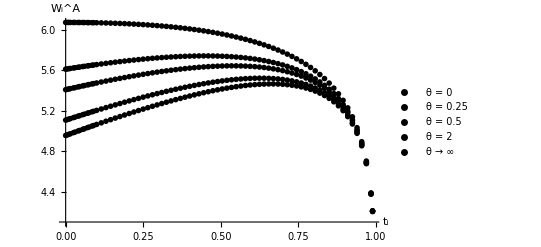

```mathematica
figure3=ListPlot[{s11111welAθ00i, s11111welAθ025i, s11111welAθ05i,s11111welAθ20i, s11111minIncreali}
, PlotLegends->Placed[PointLegend[{"θ = 0", "θ = 0.25","θ = 0.5", "θ = 2", "θ → ∞"}
,LegendFunction->Panel,LegendMargins->1],{0.7,0.325}]
, PlotRange->Full,AxesLabel->{"t_i","W_i^A"} ,AxesStyle->Directive[ Black]
,PlotMarkers->{"OpenMarkers",Tiny}
, MaxPlotPoints->75
,PlotStyle->Black
]
Export["UnilateralTax_Figure_3.pdf",figure3];
```

### Table 1: Optimal tax rates (t_i^opt) for different values of inequality aversion across scenarios

```mathematica
Grid[s11111topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s21111topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s12111topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
```

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.05
t_i^opt|θ=0.25 | 0.45
t_i^opt|θ=0.5 | 0.54
t_i^opt|θ=1.0 | 0.595
t_i^opt|θ=1.5 | 0.62
t_i^opt|θ=2.0 | 0.63
t_i^opt|θ→∞ | 0.665
t_i^opt|Sen | 0.66

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.05
t_i^opt|θ=0.25 | 0.44
t_i^opt|θ=0.5 | 0.53
t_i^opt|θ=1.0 | 0.59
t_i^opt|θ=1.5 | 0.61
t_i^opt|θ=2.0 | 0.62
t_i^opt|θ→∞ | 0.655
t_i^opt|Sen | 0.655

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.04
t_i^opt|θ=0.25 | 0.405
t_i^opt|θ=0.5 | 0.5
t_i^opt|θ=1.0 | 0.565
t_i^opt|θ=1.5 | 0.59
t_i^opt|θ=2.0 | 0.605
t_i^opt|θ→∞ | 0.655
t_i^opt|Sen | 0.65

### Table A.1: Optimal tax rates (t_i^opt) for different values of inequality aversion and parameter choices

```mathematica
Grid[s11111topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s11113topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s11112topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s11211topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s11311topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s11131topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s11121topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
```

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.05
t_i^opt|θ=0.25 | 0.45
t_i^opt|θ=0.5 | 0.54
t_i^opt|θ=1.0 | 0.595
t_i^opt|θ=1.5 | 0.62
t_i^opt|θ=2.0 | 0.63
t_i^opt|θ→∞ | 0.665
t_i^opt|Sen | 0.66

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.05
t_i^opt|θ=0.25 | 0.45
t_i^opt|θ=0.5 | 0.54
t_i^opt|θ=1.0 | 0.595
t_i^opt|θ=1.5 | 0.62
t_i^opt|θ=2.0 | 0.63
t_i^opt|θ→∞ | 0.665
t_i^opt|Sen | 0.66

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.05
t_i^opt|θ=0.25 | 0.45
t_i^opt|θ=0.5 | 0.54
t_i^opt|θ=1.0 | 0.595
t_i^opt|θ=1.5 | 0.615
t_i^opt|θ=2.0 | 0.63
t_i^opt|θ→∞ | 0.665
t_i^opt|Sen | 0.66

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.005
t_i^opt|θ=0.25 | 0.07
t_i^opt|θ=0.5 | 0.11
t_i^opt|θ=1.0 | 0.165
t_i^opt|θ=1.5 | 0.2
t_i^opt|θ=2.0 | 0.22
t_i^opt|θ→∞ | 0.33
t_i^opt|Sen | 0.315

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.
t_i^opt|θ=0.25 | 0.
t_i^opt|θ=0.5 | 0.005
t_i^opt|θ=1.0 | 0.99
t_i^opt|θ=1.5 | 0.005
t_i^opt|θ=2.0 | 0.01
t_i^opt|θ→∞ | 0.07
t_i^opt|Sen | 0.055

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.01
t_i^opt|θ=0.25 | 0.18
t_i^opt|θ=0.5 | 0.26
t_i^opt|θ=1.0 | 0.335
t_i^opt|θ=1.5 | 0.37
t_i^opt|θ=2.0 | 0.39
t_i^opt|θ→∞ | 0.46
t_i^opt|Sen | 0.45

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.
t_i^opt|θ=0.25 | 0.035
t_i^opt|θ=0.5 | 0.06
t_i^opt|θ=1.0 | 0.1
t_i^opt|θ=1.5 | 0.12
t_i^opt|θ=2.0 | 0.135
t_i^opt|θ→∞ | 0.23
t_i^opt|Sen | 0.2

### Table A.2: Optimal tax rates (t_i^opt) for different values of inequality aversion and parameter choices across scenarios

```mathematica
Grid[s11111topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s11211topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s11121topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s21111topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s21211topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s21121topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s12111topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s12211topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s12121topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
```

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.05
t_i^opt|θ=0.25 | 0.45
t_i^opt|θ=0.5 | 0.54
t_i^opt|θ=1.0 | 0.595
t_i^opt|θ=1.5 | 0.62
t_i^opt|θ=2.0 | 0.63
t_i^opt|θ→∞ | 0.665
t_i^opt|Sen | 0.66

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.005
t_i^opt|θ=0.25 | 0.07
t_i^opt|θ=0.5 | 0.11
t_i^opt|θ=1.0 | 0.165
t_i^opt|θ=1.5 | 0.2
t_i^opt|θ=2.0 | 0.22
t_i^opt|θ→∞ | 0.33
t_i^opt|Sen | 0.315

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.
t_i^opt|θ=0.25 | 0.035
t_i^opt|θ=0.5 | 0.06
t_i^opt|θ=1.0 | 0.1
t_i^opt|θ=1.5 | 0.12
t_i^opt|θ=2.0 | 0.135
t_i^opt|θ→∞ | 0.23
t_i^opt|Sen | 0.2

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.05
t_i^opt|θ=0.25 | 0.44
t_i^opt|θ=0.5 | 0.53
t_i^opt|θ=1.0 | 0.59
t_i^opt|θ=1.5 | 0.61
t_i^opt|θ=2.0 | 0.62
t_i^opt|θ→∞ | 0.655
t_i^opt|Sen | 0.655

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.005
t_i^opt|θ=0.25 | 0.07
t_i^opt|θ=0.5 | 0.11
t_i^opt|θ=1.0 | 0.165
t_i^opt|θ=1.5 | 0.2
t_i^opt|θ=2.0 | 0.22
t_i^opt|θ→∞ | 0.33
t_i^opt|Sen | 0.31

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.
t_i^opt|θ=0.25 | 0.035
t_i^opt|θ=0.5 | 0.06
t_i^opt|θ=1.0 | 0.095
t_i^opt|θ=1.5 | 0.12
t_i^opt|θ=2.0 | 0.135
t_i^opt|θ→∞ | 0.225
t_i^opt|Sen | 0.2

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.04
t_i^opt|θ=0.25 | 0.405
t_i^opt|θ=0.5 | 0.5
t_i^opt|θ=1.0 | 0.565
t_i^opt|θ=1.5 | 0.59
t_i^opt|θ=2.0 | 0.605
t_i^opt|θ→∞ | 0.655
t_i^opt|Sen | 0.65

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.005
t_i^opt|θ=0.25 | 0.055
t_i^opt|θ=0.5 | 0.095
t_i^opt|θ=1.0 | 0.145
t_i^opt|θ=1.5 | 0.18
t_i^opt|θ=2.0 | 0.2
t_i^opt|θ→∞ | 0.33
t_i^opt|Sen | {0.,3.04406}

t_i^opt|θ=0 | s12121welAθ00i⟦{{{}}⟦1,1⟧}⟧⟦1,1⟧
t_i^opt|θ=0.01 | s12121welAθ001i⟦{{{}}⟦1,1⟧}⟧⟦1,1⟧
t_i^opt|θ=0.25 | s12121welAθ025i⟦{{{}}⟦1,1⟧}⟧⟦1,1⟧
t_i^opt|θ=0.5 | s12121welAθ05i⟦{{{}}⟦1,1⟧}⟧⟦1,1⟧
t_i^opt|θ=1.0 | s12121welAθ10i⟦{{{}}⟦1,1⟧}⟧⟦1,1⟧
t_i^opt|θ=1.5 | s12121welAθ15i⟦{{{}}⟦1,1⟧}⟧⟦1,1⟧
t_i^opt|θ=2.0 | s12121welAθ20i⟦{{{}}⟦1,1⟧}⟧⟦1,1⟧
t_i^opt|θ→∞ | s12121minIncreali⟦{{{}}⟦1,1⟧}⟧⟦1,1⟧
t_i^opt|Sen | s12121welGi⟦{{{}}⟦1,1⟧}⟧⟦1,1⟧

## S.2 “Trade imbalances”

### Table S.1: Trade imbalances: Effects on firm selection and the wage

```mathematica
tableNumSimTIB={{"t_i","",{Part[s11111massLi,1]}[[1,1]],{Part[s11111massLi,21]}[[1,1]],{Part[s11111massLi,41]}[[1,1]],{Part[s11111massLi,61]}[[1,1]],{Part[s11111massLi,81]}[[1,1]],{Part[s11111massLi,101]}[[1,1]],{Part[s11111massLi,121]}[[1,1]],{Part[s11111massLi,141]}[[1,1]],{Part[s11111massLi,161]}[[1,1]],{Part[s11111massLi,181]}[[1,1]]}};
AppendTo[tableNumSimTIB,{"φ_i^i","T=0",N[Round[1000*{Part[s11111ϕii,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕii,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕii,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕii,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111ϕii,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕii,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕii,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕii,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕii,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕii,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"φ_i^i","T=5",N[Round[1000*{Part[s11111TIBpϕii,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕii,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕii,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕii,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111TIBpϕii,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕii,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕii,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕii,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕii,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕii,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"φ_i^i","T=-5",N[Round[1000*{Part[s11111TIBnϕii,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕii,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕii,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕii,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111TIBnϕii,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕii,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕii,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕii,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕii,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕii,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"φ_i^j","T=0",N[Round[1000*{Part[s11111ϕij,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕij,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕij,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕij,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111ϕij,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕij,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕij,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕij,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕij,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕij,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"φ_i^j","T=5",N[Round[1000*{Part[s11111TIBpϕij,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕij,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕij,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕij,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111TIBpϕij,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕij,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕij,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕij,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕij,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕij,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"φ_i^j","T=-5",N[Round[1000*{Part[s11111TIBnϕij,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕij,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕij,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕij,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111TIBnϕij,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕij,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕij,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕij,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕij,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕij,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"χ_i","T=0",N[Round[1000*{Part[s11111χi,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111χi,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"χ_i","T=5",N[Round[1000*{Part[s11111TIBpχi,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpχi,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpχi,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpχi,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111TIBpχi,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpχi,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpχi,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpχi,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpχi,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpχi,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"χ_i","T=-5",N[Round[1000*{Part[s11111TIBnχi,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnχi,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnχi,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnχi,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111TIBnχi,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnχi,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnχi,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnχi,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnχi,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnχi,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"φ_j^j","T=0",N[Round[1000*{Part[s11111ϕjj,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕjj,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕjj,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕjj,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111ϕjj,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕjj,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕjj,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕjj,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕjj,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕjj,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"φ_j^j","T=5",N[Round[1000*{Part[s11111TIBpϕjj,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕjj,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕjj,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕjj,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111TIBpϕjj,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕjj,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕjj,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕjj,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕjj,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕjj,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"φ_j^j","T=-5",N[Round[1000*{Part[s11111TIBnϕjj,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕjj,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕjj,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕjj,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111TIBnϕjj,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕjj,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕjj,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕjj,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕjj,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕjj,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"φ_j^i","T=0",N[Round[1000*{Part[s11111ϕji,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕji,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕji,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕji,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111ϕji,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕji,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕji,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕji,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕji,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ϕji,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"φ_j^i","T=5",N[Round[1000*{Part[s11111TIBpϕji,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕji,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕji,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕji,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111TIBpϕji,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕji,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕji,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕji,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕji,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpϕji,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"φ_j^i","T=-5",N[Round[1000*{Part[s11111TIBnϕji,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕji,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕji,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕji,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111TIBnϕji,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕji,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕji,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕji,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕji,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnϕji,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"χ_j","T=0",N[Round[1000*{Part[s11111χj,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111χj,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"χ_j","T=5",N[Round[1000*{Part[s11111TIBpχj,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpχj,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpχj,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpχj,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111TIBpχj,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpχj,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpχj,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpχj,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpχj,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpχj,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"χ_j","T=-5",N[Round[1000*{Part[s11111TIBnχj,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnχj,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnχj,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnχj,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111TIBnχj,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnχj,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnχj,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnχj,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnχj,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnχj,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"w_i","T=0",N[Round[1000*{Part[s11111wi,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111wi,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111wi,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111wi,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111wi,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111wi,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111wi,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111wi,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111wi,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111wi,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"w_i","T=5",N[Round[1000*{Part[s11111TIBpwi,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpwi,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpwi,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpwi,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111TIBpwi,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpwi,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpwi,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpwi,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpwi,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBpwi,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimTIB,{"w_i","T=-5",N[Round[1000*{Part[s11111TIBnwi,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnwi,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnwi,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnwi,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111TIBnwi,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnwi,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnwi,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnwi,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnwi,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111TIBnwi,181]}[[1,2]]]/1000,3]}];
tableNumSimTIB
```

{{t_i,,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},{φ_i^i,T=0,1.95,1.99,2.05,2.11,2.19,2.29,2.41,2.59,2.86,3.4},{φ_i^i,T=5,1.96,2.01,2.06,2.13,2.21,2.3,2.43,2.61,2.88,3.43},{φ_i^i,T=-5,1.93,1.98,2.03,2.1,2.17,2.27,2.4,2.57,2.84,3.37},{φ_i^j,T=0,2.47,2.53,2.6,2.68,2.78,2.9,3.05,3.26,3.59,4.23},{φ_i^j,T=5,2.42,2.48,2.55,2.63,2.72,2.84,2.99,3.2,3.52,4.15},{φ_i^j,T=-5,2.52,2.58,2.65,2.73,2.83,2.95,3.11,3.33,3.66,4.32},{χ_i,T=0,0.384,0.384,0.385,0.385,0.387,0.388,0.391,0.395,0.402,0.416},{χ_i,T=5,0.428,0.428,0.428,0.429,0.431,0.433,0.436,0.441,0.449,0.466},{χ_i,T=-5,0.346,0.346,0.346,0.347,0.347,0.349,0.351,0.355,0.36,0.372},{φ_j^j,T=0,1.99,1.99,1.99,1.99,1.99,1.99,1.99,1.99,1.99,1.98},{φ_j^j,T=5,1.98,1.98,1.98,1.98,1.98,1.98,1.98,1.97,1.97,1.97},{φ_j^j,T=-5,2.01,2.01,2.01,2.01,2.01,2.01,2.01,2.,2.,2.},{φ_j^i,T=0,2.53,2.53,2.53,2.53,2.53,2.53,2.54,2.54,2.55,2.57},{φ_j^i,T=5,2.58,2.58,2.58,2.58,2.58,2.59,2.59,2.59,2.6,2.62},{φ_j^i,T=-5,2.48,2.48,2.48,2.48,2.49,2.49,2.49,2.49,2.5,2.51},{χ_j,T=0,0.385,0.384,0.384,0.383,0.382,0.381,0.378,0.374,0.368,0.355},{χ_j,T=5,0.345,0.345,0.345,0.344,0.343,0.342,0.339,0.335,0.329,0.317},{χ_j,T=-5,0.428,0.428,0.427,0.426,0.425,0.424,0.421,0.417,0.41,0.398},{w_i,T=0,1.01,1.,0.989,0.977,0.963,0.947,0.928,0.905,0.873,0.823},{w_i,T=5,1.,0.991,0.98,0.968,0.954,0.939,0.92,0.897,0.865,0.815},{w_i,T=-5,1.02,1.01,0.998,0.985,0.971,0.955,0.936,0.913,0.881,0.831}}

## S.3 “Numerical simulation in levels”

### Figure S.2: Numerical simulation of Proposition 1, part 1

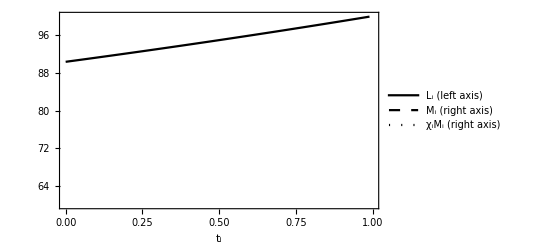
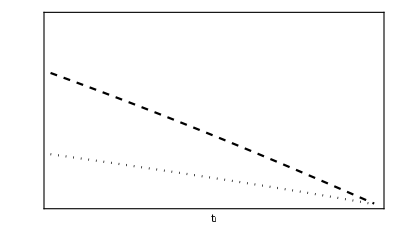

```mathematica
figureS2a1=ListLinePlot[{s11111massLi,empty,empty}
,PlotStyle->{{Black},{Black,Dashed},{Black,Dotted}}
, PlotLegends->Placed[PointLegend[{Style["L_i (left axis)",FontSize->12],Style["M_i (right axis)",FontSize->12], Style["χ_iM_i (right axis)",FontSize->12]}
,LegendFunction->Panel,LegendMargins->1],
Right
]
,AxesStyle->Directive[ Black]
,Frame->{{True,False},{True,False}}
,FrameLabel->{Style["t_i",FontSize->10]}
,PlotStyle->{{Black}}
,ImagePadding->35
,PlotStyle->Black
,PlotRange->{{0,1},{60,100}}];
figureS2a2=ListLinePlot[{s11111massMi,s11111massMij}
,AxesLabel->{Style["t_i",FontSize->10]}
,AxesStyle->Directive[ Black]
,Frame->{{False,True},{True,False}}
,PlotStyle->{{Black,Dashed},{Black,Dotted}}
,PlotStyle->Black
,ImagePadding->35
, FrameTicks->{{None,All},{None,None}}
,PlotRange->{{0,1},{0,10}}];
figureS2a=Overlay[{figureS2a1,figureS2a2}]
Export["UnilateralTax_Figure_S2a.pdf",figureS2a];
```

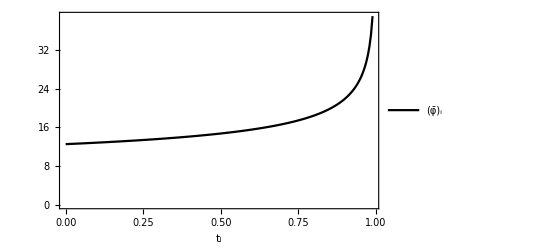

```mathematica
figureS2b=ListLinePlot[{s11111avgϕi}
,AxesLabel->{Style["t_i",FontSize->10]}
,PlotStyle->{{Black},{Black,Dashed},{Black,Dotted}}
, PlotLegends->Placed[PointLegend[{Style[Subscript[OverBar[φ], i],FontSize->12]}
,LegendFunction->Panel,LegendMargins->1],
Right
]
,AxesStyle->Directive[ Black]
,Frame->{{True,False},{True,False}}
,PlotStyle->{{Black}}
,ImagePadding->35
,FrameLabel->{Style["t_i",FontSize->10]}
,PlotStyle->Black
,PlotRange->Full]
Export["UnilateralTax_Figure_S2b.pdf",figureS2b];
```

### Figure S.3: Numerical simulation of Proposition 1, part 2

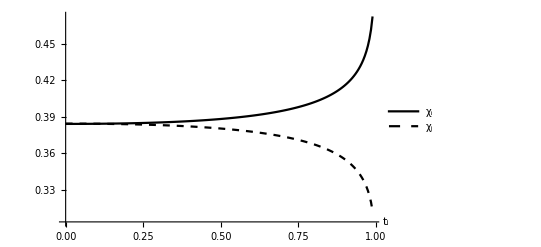

```mathematica
figureS3a=
ListLinePlot[{s11111χi,s11111χj}
, PlotLegends->Placed[PointLegend[{Style["χ_i",FontSize->12],Style["χ_j",FontSize->12]}
,LegendFunction->Panel,LegendMargins->1],
Right
]
,AxesLabel->{Style["t_i",FontSize->10]}
,AxesStyle->Directive[ Black]
,PlotStyle->{{Black},{Black,Dashed},{Black,Dotted}}
,PlotStyle->Black
, PlotRange->Full]
Export["UnilateralTax_Figure_S3a.pdf",figureS3a];
```

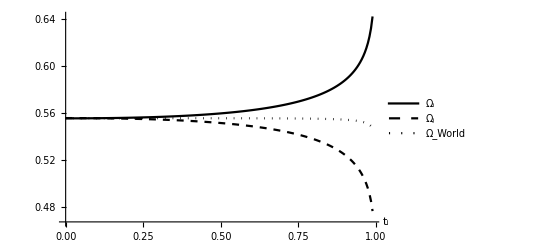

```mathematica
figureS3b=
ListLinePlot[{s11111Ωi, s11111Ωj, s11111ΩWorld}
, PlotLegends->Placed[PointLegend[{Style["Ω_i",FontSize->12],Style["Ω_j",FontSize->12],Style["Ω_World",FontSize->12]}
,LegendFunction->Panel,LegendMargins->1],
Right
]
,AxesLabel->{Style["t_i",FontSize->10]}
,AxesStyle->Directive[ Black]
,PlotStyle->{{Black},{Black,Dashed},{Black,Dotted}}
,PlotStyle->Black
, PlotRange->Full]
Export["UnilateralTax_Figure_S3b.pdf",figureS3b];
```

### Figure S.4: Numerical simulation of Proposition 1, part 3

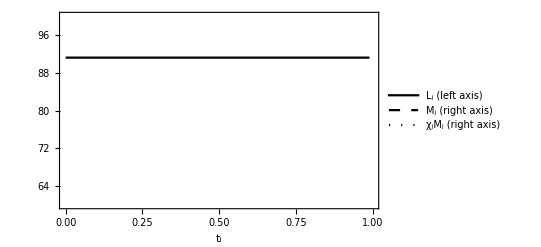
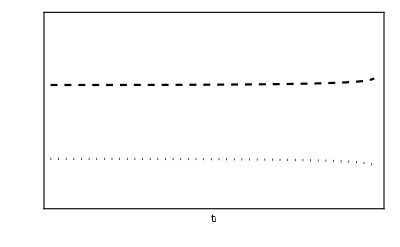

```mathematica
figureS4a1=
ListLinePlot[{s11111massLj,empty,empty}
,PlotStyle->{{Black},{Black,Dashed},{Black,Dotted}}
, PlotLegends->Placed[PointLegend[{Style["L_j (left axis)",FontSize->12],Style["M_j (right axis)",FontSize->12], Style["χ_jM_j (right axis)",FontSize->12]}
,LegendFunction->Panel,LegendMargins->1],
Right
]
,AxesStyle->Directive[ Black]
,Frame->{{True,False},{True,False}}
,FrameLabel->{Style["t_i",FontSize->10]}
,PlotStyle->{{Black}}
,ImagePadding->35
,PlotStyle->Black
,PlotRange->{{0,1},{60,100}}];
figureS4a2=ListLinePlot[{s11111massMj,s11111massMji}
,AxesLabel->{Style["t_i",FontSize->10]}
,AxesStyle->Directive[ Black]
,Frame->{{False,True},{True,False}}
,PlotStyle->{{Black,Dashed},{Black,Dotted}}
,PlotStyle->Black
,ImagePadding->35
, FrameTicks->{{None,All},{None,None}}
,PlotRange->{{0,1},{0,10}}];
figureS4a=Overlay[{figureS4a1,figureS4a2}]
Export["UnilateralTax_Figure_S4a.pdf",figureS4a];
```

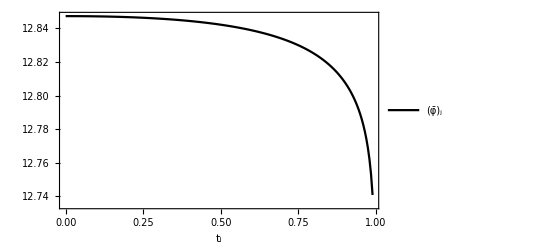

```mathematica
figureS4b=
ListLinePlot[{s11111avgϕj}
,AxesLabel->{Style["t_i",FontSize->10]}
,PlotStyle->{{Black},{Black,Dashed},{Black,Dotted}}
, PlotLegends->Placed[PointLegend[{Style[Subscript[OverBar[φ], j],FontSize->12]}
,LegendFunction->Panel,LegendMargins->1],
Right
]
,AxesStyle->Directive[ Black]
,Frame->{{True,False},{True,False}}
,PlotStyle->{{Black}}
,ImagePadding->35
,FrameLabel->{Style["t_i",FontSize->10]}
,PlotStyle->Black
,PlotRange->Full]
Export["UnilateralTax_Figure_S4b.pdf",figureS4b];
```

### Figure S.5: Numerical simulation of Proposition 2

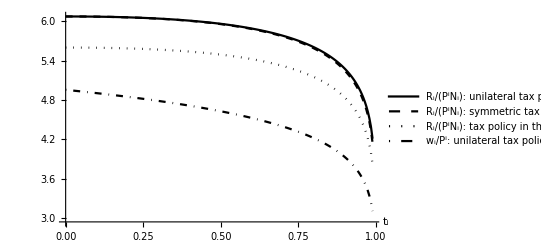

```mathematica
s11111realwi=Transpose@{Part[s11111wi][[;;,1]],Part[s11111wi][[;;,2]]/Part[s11111indexPi][[;;,2]]};
figureS5=
ListLinePlot[{s11111welAθ00i,s21111welAθ00i,s12111welAθ00i,s11111realwi}
, PlotLegends->Placed[PointLegend[{Style["R_i/(P^iN_i): unilateral tax policy in the open economy",FontSize->12],Style["R_i/(P^iN_i): symmetric tax policy in the open economy",FontSize->12],Style["R_i/(P^iN_i): tax policy in the closed economy",FontSize->12],Style["w_i/P^i: unilateral tax policy in the open economy",FontSize->12]}
,LegendFunction->Panel,LegendMargins->1],
Right
]
,AxesLabel->{Style["t_i",FontSize->10]}
,AxesStyle->Directive[ Black]
,PlotStyle->{{Black},{Black,Dashed},{Black,Dotted},{Black,DotDashed}}
,PlotStyle->Black
, PlotRange->Full]
Export["UnilateralTax_Figure_S5.pdf",figureS5];
```

### Figure S.6: Numerical simulation of Proposition 3

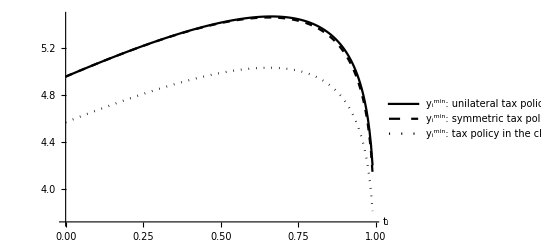

```mathematica
figureS6=
ListLinePlot[{s11111minIncreali,s21111minIncreali,s12111minIncreali}
, PlotLegends->Placed[PointLegend[{Style["y_i^min: unilateral tax policy in the open economy",FontSize->12],Style["y_i^min: symmetric tax policy in the open economy",FontSize->12],Style["y_i^min: tax policy in the closed economy",FontSize->12]}
,LegendFunction->Panel,LegendMargins->1],
Right
]
,AxesLabel->{Style["t_i",FontSize->10]}
,AxesStyle->Directive[ Black]
,PlotStyle->{{Black},{Black,Dashed},{Black,Dotted},{Black,DotDashed}}
,PlotStyle->Black
, PlotRange->Full]
Export["UnilateralTax_Figure_S6.pdf",figureS6];
```

### Figure S.7: Numerical simulation of Proposition 4

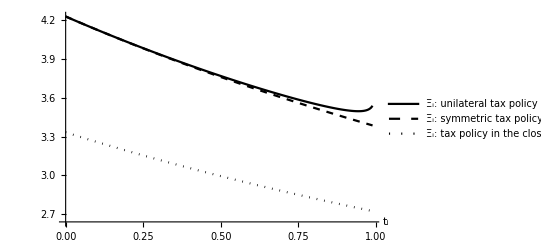

```mathematica
figureS7=
ListLinePlot[{s11111Ξi,s21111Ξi,s12111Ξi}
, PlotLegends->Placed[PointLegend[{Style["Ξ_i: unilateral tax policy in the open economy",FontSize->12],Style["Ξ_i: symmetric tax policy in the open economy",FontSize->12],Style["Ξ_i: tax policy in the closed economy",FontSize->12]}
,LegendFunction->Panel,LegendMargins->1],
Right
]
,AxesLabel->{Style["t_i",FontSize->10]}
,AxesStyle->Directive[ Black]
,PlotStyle->{{Black},{Black,Dashed},{Black,Dotted},{Black,DotDashed}}
,PlotStyle->Black
, PlotRange->Full]
Export["UnilateralTax_Figure_S7.pdf",figureS7];
```

### Figure S.8: Numerical simulation of Proposition 5

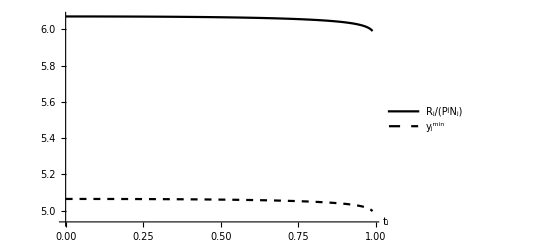

```mathematica
figureS8a=
ListLinePlot[{s11111welAθ00j,s11111minIncrealj}
, PlotLegends->Placed[PointLegend[{Style["R_j/(P^jN_j)",FontSize->12],Style["y_j^min",FontSize->12]}
,LegendFunction->Panel,LegendMargins->1],
Right
]
,AxesLabel->{Style["t_i",FontSize->10]}
,AxesStyle->Directive[ Black]
,PlotStyle->{{Black},{Black,Dashed},{Black,Dotted},{Black,DotDashed}}
,PlotStyle->Black
, PlotRange->Full
]
Export["UnilateralTax_Figure_S8a.pdf",figureS8a];
```

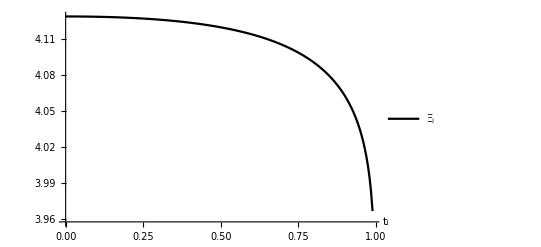

```mathematica
figureS8b=
ListLinePlot[{s11111Ξj}
, PlotLegends->Placed[PointLegend[{Style["Ξ_j",FontSize->12]}
,LegendFunction->Panel,LegendMargins->1],
Right
]
,AxesLabel->{Style["t_i",FontSize->10]}
,AxesStyle->Directive[ Black]
,PlotStyle->{{Black},{Black,Dashed},{Black,Dotted},{Black,DotDashed}}
,PlotStyle->Black
, PlotRange->Full]
Export["UnilateralTax_Figure_S8b.pdf",figureS8b];
```

### Table S.2: Variation in k: Effects on the factor allocation and the terms of trade

```mathematica
tableNumSimk={{"t_i","",{Part[s11111massLi,1]}[[1,1]],{Part[s11111massLi,21]}[[1,1]],{Part[s11111massLi,41]}[[1,1]],{Part[s11111massLi,61]}[[1,1]],{Part[s11111massLi,81]}[[1,1]],{Part[s11111massLi,101]}[[1,1]],{Part[s11111massLi,121]}[[1,1]],{Part[s11111massLi,141]}[[1,1]],{Part[s11111massLi,161]}[[1,1]],{Part[s11111massLi,181]}[[1,1]]}};
AppendTo[tableNumSimk,{"L_i","k=4",N[Round[10*{Part[s11111massLi,1]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,21]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,41]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,61]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,81]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,101]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,121]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,141]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,161]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,181]}[[1,2]]]/10,3]}];
AppendTo[tableNumSimk,{"L_i","k=8",N[Round[10*{Part[s11211massLi,1]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLi,21]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLi,41]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLi,61]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLi,81]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLi,101]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLi,121]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLi,141]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLi,161]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLi,181]}[[1,2]]]/10,3]}];
AppendTo[tableNumSimk,{"M_i","k=4",N[Round[10*{Part[s11111massMi,1]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,21]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,41]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,61]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,81]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,101]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,121]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,141]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,161]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,181]}[[1,2]]]/10,1]}];
AppendTo[tableNumSimk,{"M_i","k=8",N[Round[10*{Part[s11211massMi,1]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massMi,21]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massMi,41]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massMi,61]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massMi,81]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMi,101]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMi,121]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMi,141]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMi,161]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMi,181]}[[1,2]]]/10,2]}];
AppendTo[tableNumSimk,{"χ_iM_i","k=4",N[Round[10*{Part[s11111massMij,1]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMij,21]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMij,41]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMij,61]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMij,81]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMij,101]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMij,121]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMij,141]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMij,161]}[[1,2]]]/10,1],N[Round[10*{Part[s11111massMij,181]}[[1,2]]]/10,1]}];
AppendTo[tableNumSimk,{"χ_iM_i","k=8",N[Round[10*{Part[s11211massMij,1]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMij,21]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMij,41]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMij,61]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMij,81]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMij,101]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMij,121]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMij,141]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMij,161]}[[1,2]]]/10,1],N[Round[10*{Part[s11211massMij,181]}[[1,2]]]/10,1]}];
AppendTo[tableNumSimk,{"OverBar[φ]_i","k=4",N[Round[10*{Part[s11111avgϕi,1]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,21]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,41]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,61]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,81]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,101]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,121]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,141]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,161]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,181]}[[1,2]]]/10,3]}];
AppendTo[tableNumSimk,{"OverBar[φ]_i","k=8",N[Round[100*{Part[s11211avgϕi,1]}[[1,2]]]/100,2],N[Round[100*{Part[s11211avgϕi,21]}[[1,2]]]/100,2],N[Round[100*{Part[s11211avgϕi,41]}[[1,2]]]/100,2],N[Round[100*{Part[s11211avgϕi,61]}[[1,2]]]/100,2],N[Round[100*{Part[s11211avgϕi,81]}[[1,2]]]/100,2],N[Round[100*{Part[s11211avgϕi,101]}[[1,2]]]/100,2],N[Round[100*{Part[s11211avgϕi,121]}[[1,2]]]/100,2],N[Round[100*{Part[s11211avgϕi,141]}[[1,2]]]/100,2],N[Round[100*{Part[s11211avgϕi,161]}[[1,2]]]/100,2],N[Round[100*{Part[s11211avgϕi,181]}[[1,2]]]/100,2]}];
AppendTo[tableNumSimk,{"χ_i","k=4",N[Round[1000*{Part[s11111χi,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111χi,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimk,{"χ_i","k=8",N[Round[1000*{Part[s11211χi,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211χi,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211χi,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211χi,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11211χi,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211χi,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211χi,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211χi,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211χi,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211χi,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimk,{"Ω_i","k=4",N[Round[1000*{Part[s11111Ωi,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωi,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωi,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωi,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111Ωi,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωi,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωi,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωi,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωi,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωi,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimk,{"Ω_i","k=8",N[Round[1000*{Part[s11211Ωi,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211Ωi,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211Ωi,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211Ωi,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11211Ωi,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211Ωi,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211Ωi,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211Ωi,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211Ωi,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211Ωi,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimk,{"Export_i","k=4",N[Round[1000*{Part[s11111exporti,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111exporti,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111exporti,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111exporti,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111exporti,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111exporti,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111exporti,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111exporti,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111exporti,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111exporti,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimk,{"Export_i","k=8",N[Round[1000*{Part[s11211exporti,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211exporti,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211exporti,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211exporti,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11211exporti,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211exporti,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211exporti,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211exporti,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211exporti,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211exporti,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimk,{"P_i^j/P_j^i","k=4",N[Round[100000*{Part[s11111toti,1]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,21]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,41]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,61]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,81]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,101]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,121]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,141]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,161]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,181]}[[1,2]]]/100000,4]}];
AppendTo[tableNumSimk,{"P_i^j/P_j^i","k=8",N[Round[100000*{Part[s11211toti,1]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11211toti,21]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11211toti,41]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11211toti,61]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11211toti,81]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11211toti,101]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11211toti,121]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11211toti,141]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11211toti,161]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11211toti,181]}[[1,2]]]/100000,4]}];
AppendTo[tableNumSimk,{"χ_j","k=4",N[Round[1000*{Part[s11111χj,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111χj,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimk,{"χ_j","k=8",N[Round[1000*{Part[s11211χj,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211χj,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211χj,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211χj,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11211χj,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211χj,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211χj,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211χj,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211χj,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211χj,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimk,{"Ω_j","k=4",N[Round[1000*{Part[s11111Ωj,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωj,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωj,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωj,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111Ωj,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωj,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωj,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωj,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωj,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωj,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimk,{"Ω_j","k=8",N[Round[1000*{Part[s11211Ωj,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211Ωj,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211Ωj,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211Ωj,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11211Ωj,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211Ωj,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211Ωj,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211Ωj,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211Ωj,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211Ωj,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimk,{"L_j","k=4",N[Round[10*{Part[s11111massLj,1]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,21]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,41]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,61]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,81]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,101]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,121]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,141]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,161]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,181]}[[1,2]]]/10,3]}];
AppendTo[tableNumSimk,{"L_j","k=8",N[Round[10*{Part[s11211massLj,1]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLj,21]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLj,41]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLj,61]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLj,81]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLj,101]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLj,121]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLj,141]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLj,161]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massLj,181]}[[1,2]]]/10,3]}];
AppendTo[tableNumSimk,{"M_j","k=4",N[Round[10*{Part[s11111massMj,1]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,21]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,41]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,61]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,81]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,101]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,121]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,141]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,161]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,181]}[[1,2]]]/10,2]}];
AppendTo[tableNumSimk,{"M_j","k=8",N[Round[10*{Part[s11211massMj,1]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massMj,21]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massMj,41]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massMj,61]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massMj,81]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massMj,101]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massMj,121]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massMj,141]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massMj,161]}[[1,2]]]/10,3],N[Round[10*{Part[s11211massMj,181]}[[1,2]]]/10,3]}];
AppendTo[tableNumSimk,{"χ_jM_j","k=4",N[Round[10*{Part[s11111massMji,1]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMji,21]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMji,41]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMji,61]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMji,81]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMji,101]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMji,121]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMji,141]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMji,161]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMji,181]}[[1,2]]]/10,2]}];
AppendTo[tableNumSimk,{"χ_jM_j","k=8",N[Round[10*{Part[s11211massMji,1]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMji,21]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMji,41]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMji,61]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMji,81]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMji,101]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMji,121]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMji,141]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMji,161]}[[1,2]]]/10,2],N[Round[10*{Part[s11211massMji,181]}[[1,2]]]/10,2]}];
AppendTo[tableNumSimk,{"OverBar[φ]_j","k=4",N[Round[100*{Part[s11111avgϕj,1]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,21]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,41]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,61]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,81]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,101]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,121]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,141]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,161]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,181]}[[1,2]]]/100,4]}];
AppendTo[tableNumSimk,{"OverBar[φ]_j","k=8",N[Round[1000*{Part[s11211avgϕj,1]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11211avgϕj,21]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11211avgϕj,41]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11211avgϕj,61]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11211avgϕj,81]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11211avgϕj,101]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11211avgϕj,121]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11211avgϕj,141]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11211avgϕj,161]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11211avgϕj,181]}[[1,2]]]/1000,4]}];
AppendTo[tableNumSimk,{"Ω_World","k=4",N[Round[1000*{Part[s11111ΩWorld,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ΩWorld,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ΩWorld,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ΩWorld,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111ΩWorld,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ΩWorld,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ΩWorld,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ΩWorld,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ΩWorld,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ΩWorld,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimk,{"Ω_World","k=8",N[Round[1000*{Part[s11211ΩWorld,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211ΩWorld,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211ΩWorld,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211ΩWorld,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11211ΩWorld,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211ΩWorld,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211ΩWorld,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211ΩWorld,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211ΩWorld,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11211ΩWorld,181]}[[1,2]]]/1000,3]}];
tableNumSimk
```

{{t_i,,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},{L_i,k=4,90.3,91.2,92.1,93.,94.,94.9,95.9,96.9,97.9,98.9},{L_i,k=8,81.2,82.7,84.3,86.,87.8,89.6,91.5,93.5,95.6,97.7},{M_i,k=4,7.,6.4,5.7,5.,4.4,3.7,3.,2.2,1.5,0.7},{M_i,k=8,16.4,15.1,13.6,12.2,11.,9.,7.4,5.6,3.8,1.9},{χ_iM_i,k=4,2.7,2.4,2.2,1.9,1.7,1.4,1.2,0.9,0.6,0.3},{χ_iM_i,k=8,2.4,2.2,2.,1.8,1.6,1.4,1.1,0.9,0.6,0.3},{OverBar[φ]_i,k=4,12.5,12.8,13.2,13.6,14.1,14.7,15.5,16.7,18.4,21.9},{OverBar[φ]_i,k=8,1.6,1.6,1.6,1.7,1.7,1.7,1.8,1.8,1.9,2.1},{χ_i,k=4,0.384,0.384,0.385,0.385,0.387,0.388,0.391,0.395,0.402,0.416},{χ_i,k=8,0.148,0.148,0.148,0.148,0.149,0.15,0.152,0.155,0.159,0.169},{Ω_i,k=4,0.555,0.555,0.556,0.556,0.558,0.559,0.562,0.566,0.573,0.587},{Ω_i,k=8,0.257,0.257,0.258,0.258,0.26,0.261,0.264,0.268,0.275,0.289},{Export_i,k=4,34.4,34.4,34.3,34.3,34.2,34.1,33.9,33.7,33.3,32.5},{Export_i,k=8,14.5,14.5,14.4,14.4,14.3,14.2,14.1,13.9,13.5,12.8},{P_i^j/P_j^i,k=4,0.9999,1.,1.,1.001,1.001,1.003,1.004,1.007,1.011,1.02},{P_i^j/P_j^i,k=8,0.9999,1.,1.,1.001,1.001,1.002,1.004,1.006,1.009,1.017},{χ_j,k=4,0.385,0.384,0.384,0.383,0.382,0.381,0.378,0.374,0.368,0.355},{χ_j,k=8,0.148,0.148,0.148,0.147,0.146,0.145,0.144,0.141,0.137,0.129},{Ω_j,k=4,0.555,0.555,0.555,0.554,0.553,0.551,0.549,0.544,0.538,0.524},{Ω_j,k=8,0.258,0.257,0.257,0.256,0.255,0.254,0.251,0.247,0.241,0.229},{L_j,k=4,91.2,91.2,91.2,91.2,91.2,91.2,91.2,91.2,91.2,91.2},{L_j,k=8,82.7,82.7,82.7,82.7,82.7,82.7,82.7,82.7,82.7,82.7},{M_j,k=4,6.4,6.4,6.4,6.4,6.4,6.4,6.4,6.4,6.4,6.5},{M_j,k=8,15.1,15.1,15.1,15.1,15.1,15.1,15.1,15.1,15.2,15.3},{χ_jM_j,k=4,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.3},{χ_jM_j,k=8,2.2,2.2,2.2,2.2,2.2,2.2,2.2,2.1,2.1,2.},{OverBar[φ]_j,k=4,12.85,12.85,12.85,12.85,12.84,12.84,12.84,12.83,12.83,12.81},{OverBar[φ]_j,k=8,1.623,1.623,1.623,1.623,1.623,1.623,1.622,1.621,1.62,1.618},{Ω_World,k=4,0.555,0.555,0.555,0.555,0.555,0.555,0.555,0.555,0.555,0.554},{Ω_World,k=8,0.257,0.257,0.257,0.257,0.257,0.257,0.257,0.257,0.257,0.255}}

### Table S.3: Variation in k: Effects on real income and inequality

```mathematica
tableNumSimk2={{"t_i","",{Part[s11111massLi,1]}[[1,1]],{Part[s11111massLi,21]}[[1,1]],{Part[s11111massLi,41]}[[1,1]],{Part[s11111massLi,61]}[[1,1]],{Part[s11111massLi,81]}[[1,1]],{Part[s11111massLi,101]}[[1,1]],{Part[s11111massLi,121]}[[1,1]],{Part[s11111massLi,141]}[[1,1]],{Part[s11111massLi,161]}[[1,1]],{Part[s11111massLi,181]}[[1,1]]}};
AppendTo[tableNumSimk2,{"R_i/(P_iN_i)","k=4",N[Round[100*{Part[s11111welAθ00i,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimk2,{"R_i/(P_iN_i)","k=8",N[Round[100*{Part[s11211welAθ00i,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00i,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00i,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00i,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00i,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00i,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00i,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00i,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00i,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00i,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimk2,{"y_i^min","k=4",N[Round[100*{Part[s11111minIncreali,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimk2,{"y_i^min","k=8",N[Round[100*{Part[s11211minIncreali,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncreali,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncreali,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncreali,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncreali,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncreali,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncreali,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncreali,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncreali,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncreali,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimk2,{"Ξ_i","k=4",N[Round[100*{Part[s11111Ξi,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimk2,{"Ξ_i","k=8",N[Round[100*{Part[s11211Ξi,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξi,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξi,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξi,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξi,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξi,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξi,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξi,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξi,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξi,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimk2,{"R_j/(P_jN_j)","k=4",N[Round[100*{Part[s11111welAθ00j,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimk2,{"R_j/(P_jN_j)","k=8",N[Round[100*{Part[s11211welAθ00j,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00j,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00j,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00j,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00j,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00j,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00j,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00j,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00j,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11211welAθ00j,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimk2,{"y_j^min","k=4",N[Round[100*{Part[s11111minIncrealj,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimk2,{"y_j^min","k=8",N[Round[100*{Part[s11211minIncrealj,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncrealj,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncrealj,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncrealj,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncrealj,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncrealj,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncrealj,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncrealj,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncrealj,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11211minIncrealj,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimk2,{"Ξ_j","k=4",N[Round[100*{Part[s11111Ξj,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimk2,{"Ξ_j","k=8",N[Round[100*{Part[s11211Ξj,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξj,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξj,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξj,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξj,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξj,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξj,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξj,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξj,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11211Ξj,181]}[[1,2]]]/100,3]}];
tableNumSimk2
```

{{t_i,,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},{R_i/(P_iN_i),k=4,6.07,6.07,6.06,6.04,6.01,5.96,5.89,5.78,5.61,5.28},{R_i/(P_iN_i),k=8,3.39,3.38,3.37,3.35,3.31,3.26,3.17,3.05,2.85,2.5},{y_i^min,k=4,4.95,5.06,5.17,5.26,5.35,5.41,5.46,5.46,5.4,5.18},{y_i^min,k=8,3.07,3.1,3.12,3.13,3.13,3.11,3.06,2.97,2.8,2.48},{Ξ_i,k=4,4.23,4.13,4.03,3.94,3.85,3.77,3.69,3.62,3.56,3.51},{Ξ_i,k=8,1.62,1.6,1.58,1.57,1.55,1.53,1.52,1.5,1.49,1.48},{R_j/(P_jN_j),k=4,6.07,6.07,6.07,6.07,6.07,6.07,6.06,6.06,6.05,6.04},{R_j/(P_jN_j),k=8,3.38,3.38,3.38,3.38,3.38,3.38,3.38,3.38,3.38,3.38},{y_j^min,k=4,5.06,5.06,5.06,5.06,5.06,5.06,5.06,5.05,5.05,5.04},{y_j^min,k=8,3.1,3.1,3.1,3.1,3.1,3.1,3.1,3.1,3.1,3.1},{Ξ_j,k=4,4.13,4.13,4.13,4.13,4.12,4.12,4.11,4.1,4.09,4.06},{Ξ_j,k=8,1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.6,1.59,1.59}}

### Table S.4: Variation in σ: Effects on the factor allocation and the terms of trade

```mathematica
tableNumSimσ={{"t_i","",{Part[s11111massLi,1]}[[1,1]],{Part[s11111massLi,21]}[[1,1]],{Part[s11111massLi,41]}[[1,1]],{Part[s11111massLi,61]}[[1,1]],{Part[s11111massLi,81]}[[1,1]],{Part[s11111massLi,101]}[[1,1]],{Part[s11111massLi,121]}[[1,1]],{Part[s11111massLi,141]}[[1,1]],{Part[s11111massLi,161]}[[1,1]],{Part[s11111massLi,181]}[[1,1]]}};
AppendTo[tableNumSimσ,{"L_i","σ=3.8",N[Round[10*{Part[s11111massLi,1]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,21]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,41]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,61]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,81]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,101]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,121]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,141]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,161]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,181]}[[1,2]]]/10,3]}];
AppendTo[tableNumSimσ,{"L_i","σ=2",N[Round[10*{Part[s11121massLi,1]}[[1,2]]]/10,3],N[Round[10*{Part[s11121massLi,21]}[[1,2]]]/10,3],N[Round[10*{Part[s11121massLi,41]}[[1,2]]]/10,3],N[Round[10*{Part[s11121massLi,61]}[[1,2]]]/10,3],N[Round[10*{Part[s11121massLi,81]}[[1,2]]]/10,3],N[Round[10*{Part[s11121massLi,101]}[[1,2]]]/10,3],N[Round[10*{Part[s11121massLi,121]}[[1,2]]]/10,3],N[Round[10*{Part[s11121massLi,141]}[[1,2]]]/10,3],N[Round[10*{Part[s11121massLi,161]}[[1,2]]]/10,3],N[Round[10*{Part[s11121massLi,181]}[[1,2]]]/10,3]}];
AppendTo[tableNumSimσ,{"M_i","σ=3.8",N[Round[10*{Part[s11111massMi,1]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,21]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,41]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,61]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,81]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,101]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,121]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,141]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,161]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,181]}[[1,2]]]/10,1]}];
AppendTo[tableNumSimσ,{"M_i","σ=2",N[Round[100*{Part[s11121massMi,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11121massMi,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11121massMi,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11121massMi,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11121massMi,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11121massMi,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11121massMi,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11121massMi,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11121massMi,161]}[[1,2]]]/100,2],N[Round[100*{Part[s11121massMi,181]}[[1,2]]]/100,2]}];
AppendTo[tableNumSimσ,{"χ_iM_i","σ=3.8",N[Round[100*{Part[s11111massMij,1]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMij,21]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMij,41]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMij,61]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMij,81]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMij,101]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMij,121]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMij,141]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMij,161]}[[1,2]]]/100,1],N[Round[100*{Part[s11111massMij,181]}[[1,2]]]/100,1]}];
AppendTo[tableNumSimσ,{"χ_iM_i","σ=2",N[Round[100*{Part[s11121massMij,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11121massMij,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11121massMij,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11121massMij,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11121massMij,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11121massMij,101]}[[1,2]]]/100,2],N[Round[100*{Part[s11121massMij,121]}[[1,2]]]/100,2],N[Round[100*{Part[s11121massMij,141]}[[1,2]]]/100,2],N[Round[100*{Part[s11121massMij,161]}[[1,2]]]/100,2],N[Round[100*{Part[s11121massMij,181]}[[1,2]]]/100,2]}];
AppendTo[tableNumSimσ,{"OverBar[φ]_i","σ=3.8",N[Round[10*{Part[s11111avgϕi,1]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,21]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,41]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,61]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,81]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,101]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,121]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,141]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,161]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,181]}[[1,2]]]/10,3]}];
AppendTo[tableNumSimσ,{"OverBar[φ]_i","σ=2",N[Round[100*{Part[s11121avgϕi,1]}[[1,2]]]/100,2],N[Round[100*{Part[s11121avgϕi,21]}[[1,2]]]/100,2],N[Round[100*{Part[s11121avgϕi,41]}[[1,2]]]/100,2],N[Round[100*{Part[s11121avgϕi,61]}[[1,2]]]/100,2],N[Round[100*{Part[s11121avgϕi,81]}[[1,2]]]/100,2],N[Round[100*{Part[s11121avgϕi,101]}[[1,2]]]/100,2],N[Round[100*{Part[s11121avgϕi,121]}[[1,2]]]/100,2],N[Round[100*{Part[s11121avgϕi,141]}[[1,2]]]/100,2],N[Round[100*{Part[s11121avgϕi,161]}[[1,2]]]/100,2],N[Round[100*{Part[s11121avgϕi,181]}[[1,2]]]/100,2]}];
AppendTo[tableNumSimσ,{"χ_i","σ=3.8",N[Round[1000*{Part[s11111χi,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111χi,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimσ,{"χ_i","σ=2",N[Round[1000*{Part[s11121χi,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121χi,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121χi,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121χi,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11121χi,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121χi,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121χi,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121χi,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121χi,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121χi,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimσ,{"Ω_i","σ=3.8",N[Round[1000*{Part[s11111Ωi,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωi,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωi,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωi,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111Ωi,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωi,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωi,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωi,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωi,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωi,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimσ,{"Ω_i","σ=2",N[Round[1000*{Part[s11121Ωi,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121Ωi,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121Ωi,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121Ωi,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11121Ωi,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121Ωi,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121Ωi,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121Ωi,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121Ωi,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121Ωi,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimσ,{"Export_i","σ=3.8",N[Round[1000*{Part[s11111exporti,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111exporti,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111exporti,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111exporti,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111exporti,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111exporti,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111exporti,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111exporti,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111exporti,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111exporti,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimσ,{"Export_i","σ=2",N[Round[1000*{Part[s11121exporti,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121exporti,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121exporti,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121exporti,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11121exporti,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121exporti,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121exporti,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121exporti,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121exporti,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121exporti,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimσ,{"P_i^j/P_j^i","σ=3.8",N[Round[100000*{Part[s11111toti,1]}[[1,2]]]/100000,5],N[Round[100000*{Part[s11111toti,21]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,41]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,61]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,81]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,101]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,121]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,141]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,161]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,181]}[[1,2]]]/100000,4]}];
AppendTo[tableNumSimσ,{"P_i^j/P_j^i","σ=2",N[Round[100000*{Part[s11121toti,1]}[[1,2]]]/100000,5],N[Round[100000*{Part[s11121toti,21]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11121toti,41]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11121toti,61]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11121toti,81]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11121toti,101]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11121toti,121]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11121toti,141]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11121toti,161]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11121toti,181]}[[1,2]]]/100000,4]}];
AppendTo[tableNumSimσ,{"χ_j","σ=3.8",N[Round[1000*{Part[s11111χj,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111χj,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimσ,{"χ_j","σ=2",N[Round[1000*{Part[s11121χj,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121χj,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121χj,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121χj,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11121χj,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121χj,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121χj,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121χj,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121χj,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121χj,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimσ,{"Ω_j","σ=3.8",N[Round[1000*{Part[s11111Ωj,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωj,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωj,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωj,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111Ωj,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωj,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωj,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωj,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωj,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωj,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimσ,{"Ω_j","σ=2",N[Round[1000*{Part[s11121Ωj,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121Ωj,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121Ωj,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121Ωj,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11121Ωj,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121Ωj,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121Ωj,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121Ωj,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121Ωj,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121Ωj,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimσ,{"L_j","σ=3.8",N[Round[10*{Part[s11111massLj,1]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,21]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,41]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,61]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,81]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,101]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,121]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,141]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,161]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,181]}[[1,2]]]/10,3]}];
AppendTo[tableNumSimσ,{"L_j","σ=2",N[Round[10*{Part[s11121massLj,1]}[[1,2]]]/10,3],N[Round[10*{Part[s11121massLj,21]}[[1,2]]]/10,3],N[Round[10*{Part[s11121massLj,41]}[[1,2]]]/10,3],N[Round[10*{Part[s11121massLj,61]}[[1,2]]]/10,3],N[Round[10*{Part[s11121massLj,81]}[[1,2]]]/10,3],N[Round[10*{Part[s11121massLj,101]}[[1,2]]]/10,3],N[Round[10*{Part[s11121massLj,121]}[[1,2]]]/10,3],N[Round[10*{Part[s11121massLj,141]}[[1,2]]]/10,3],N[Round[10*{Part[s11121massLj,161]}[[1,2]]]/10,3],N[Round[10*{Part[s11121massLj,181]}[[1,2]]]/10,3]}];
AppendTo[tableNumSimσ,{"M_j","σ=3.8",N[Round[10*{Part[s11111massMj,1]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,21]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,41]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,61]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,81]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,101]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,121]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,141]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,161]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,181]}[[1,2]]]/10,2]}];
AppendTo[tableNumSimσ,{"M_j","σ=2",N[Round[10*{Part[s11121massMj,1]}[[1,2]]]/10,3],N[Round[10*{Part[s11121massMj,21]}[[1,2]]]/10,3],N[Round[10*{Part[s11121massMj,41]}[[1,2]]]/10,3],N[Round[10*{Part[s11121massMj,61]}[[1,2]]]/10,3],N[Round[10*{Part[s11121massMj,81]}[[1,2]]]/10,3],N[Round[10*{Part[s11121massMj,101]}[[1,2]]]/10,3],N[Round[10*{Part[s11121massMj,121]}[[1,2]]]/10,3],N[Round[10*{Part[s11121massMj,141]}[[1,2]]]/10,3],N[Round[10*{Part[s11121massMj,161]}[[1,2]]]/10,3],N[Round[10*{Part[s11121massMj,181]}[[1,2]]]/10,3]}];
AppendTo[tableNumSimσ,{"χ_jM_j","σ=3.8",N[Round[100*{Part[s11111massMji,1]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMji,21]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMji,41]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMji,61]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMji,81]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMji,101]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMji,121]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMji,141]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMji,161]}[[1,2]]]/100,2],N[Round[100*{Part[s11111massMji,181]}[[1,2]]]/100,2]}];
AppendTo[tableNumSimσ,{"χ_jM_j","σ=2",N[Round[100*{Part[s11121massMji,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11121massMji,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11121massMji,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11121massMji,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11121massMji,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11121massMji,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11121massMji,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11121massMji,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11121massMji,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11121massMji,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimσ,{"OverBar[φ]_j","σ=3.8",N[Round[100*{Part[s11111avgϕj,1]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,21]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,41]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,61]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,81]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,101]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,121]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,141]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,161]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,181]}[[1,2]]]/100,4]}];
AppendTo[tableNumSimσ,{"OverBar[φ]_j","σ=2",N[Round[1000*{Part[s11121avgϕj,1]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11121avgϕj,21]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11121avgϕj,41]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11121avgϕj,61]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11121avgϕj,81]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11121avgϕj,101]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11121avgϕj,121]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11121avgϕj,141]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11121avgϕj,161]}[[1,2]]]/1000,4],N[Round[1000*{Part[s11121avgϕj,181]}[[1,2]]]/1000,4]}];
AppendTo[tableNumSimσ,{"Ω_World","σ=3.8",N[Round[1000*{Part[s11111ΩWorld,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ΩWorld,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ΩWorld,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ΩWorld,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111ΩWorld,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ΩWorld,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ΩWorld,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ΩWorld,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ΩWorld,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ΩWorld,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimσ,{"Ω_World","σ=2",N[Round[1000*{Part[s11121ΩWorld,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121ΩWorld,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121ΩWorld,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121ΩWorld,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11121ΩWorld,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121ΩWorld,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121ΩWorld,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121ΩWorld,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121ΩWorld,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11121ΩWorld,181]}[[1,2]]]/1000,3]}];
tableNumSimσ
```

{{t_i,,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},{L_i,σ=3.8,90.3,91.2,92.1,93.,94.,94.9,95.9,96.9,97.9,98.9},{L_i,σ=2,57.1,59.7,62.5,65.6,69.,72.7,76.9,81.6,87.,93.},{M_i,σ=3.8,7.,6.4,5.7,5.,4.4,3.7,3.,2.2,1.5,0.7},{M_i,σ=2,31.,29.1,27.1,24.8,22.3,19.5,16.4,12.9,9.,4.6},{χ_iM_i,σ=3.8,2.7,2.4,2.2,1.9,1.7,1.4,1.2,0.88,0.6,0.3},{χ_iM_i,σ=2,11.9,11.2,10.4,9.62,8.73,7.8,6.7,5.5,4.1,2.4},{OverBar[φ]_i,σ=3.8,12.5,12.8,13.2,13.6,14.1,14.7,15.5,16.7,18.4,21.9},{OverBar[φ]_i,σ=2,2.2,2.2,2.2,2.3,2.4,2.4,2.5,2.7,2.9,3.4},{χ_i,σ=3.8,0.384,0.384,0.385,0.385,0.387,0.388,0.391,0.395,0.402,0.416},{χ_i,σ=2,0.384,0.384,0.386,0.388,0.392,0.398,0.408,0.425,0.455,0.526},{Ω_i,σ=3.8,0.555,0.555,0.556,0.556,0.558,0.559,0.562,0.566,0.573,0.587},{Ω_i,σ=2,0.555,0.555,0.557,0.559,0.563,0.569,0.579,0.596,0.626,0.69},{Export_i,σ=3.8,34.4,34.4,34.3,34.3,34.2,34.1,33.9,33.7,33.3,32.5},{Export_i,σ=2,33.2,33.2,33.1,32.9,32.7,32.3,31.8,30.8,29.3,26.2},{P_i^j/P_j^i,σ=3.8,0.99993,1.,1.,1.001,1.001,1.003,1.004,1.007,1.011,1.02},{P_i^j/P_j^i,σ=2,0.99979,1.,1.001,1.002,1.005,1.009,1.015,1.025,1.043,1.082},{χ_j,σ=3.8,0.385,0.384,0.384,0.383,0.382,0.381,0.378,0.374,0.368,0.355},{χ_j,σ=2,0.385,0.384,0.383,0.381,0.377,0.371,0.362,0.348,0.325,0.281},{Ω_j,σ=3.8,0.555,0.555,0.555,0.554,0.553,0.551,0.549,0.544,0.538,0.524},{Ω_j,σ=2,0.556,0.555,0.554,0.552,0.548,0.542,0.532,0.516,0.49,0.438},{L_j,σ=3.8,91.2,91.2,91.2,91.2,91.2,91.2,91.2,91.2,91.2,91.2},{L_j,σ=2,59.7,59.7,59.7,59.7,59.7,59.7,59.7,59.7,59.7,59.7},{M_j,σ=3.8,6.4,6.4,6.4,6.4,6.4,6.4,6.4,6.4,6.4,6.5},{M_j,σ=2,29.1,29.1,29.1,29.2,29.3,29.4,29.6,29.9,30.4,31.5},{χ_jM_j,σ=3.8,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.3},{χ_jM_j,σ=2,11.2,11.2,11.2,11.1,11.,10.9,10.7,10.4,9.87,8.83},{OverBar[φ]_j,σ=3.8,12.85,12.85,12.85,12.85,12.84,12.84,12.84,12.83,12.83,12.81},{OverBar[φ]_j,σ=2,2.195,2.195,2.195,2.195,2.194,2.192,2.19,2.187,2.18,2.167},{Ω_World,σ=3.8,0.555,0.555,0.555,0.555,0.555,0.555,0.555,0.555,0.555,0.554},{Ω_World,σ=2,0.555,0.555,0.555,0.555,0.555,0.555,0.555,0.553,0.55,0.536}}

### Table S.5: Variation in σ: Effects on real income and inequality

```mathematica
tableNumSimσ2={{"t_i","",{Part[s11111massLi,1]}[[1,1]],{Part[s11111massLi,21]}[[1,1]],{Part[s11111massLi,41]}[[1,1]],{Part[s11111massLi,61]}[[1,1]],{Part[s11111massLi,81]}[[1,1]],{Part[s11111massLi,101]}[[1,1]],{Part[s11111massLi,121]}[[1,1]],{Part[s11111massLi,141]}[[1,1]],{Part[s11111massLi,161]}[[1,1]],{Part[s11111massLi,181]}[[1,1]]}};
AppendTo[tableNumSimσ2,{"R_i/(P_iN_i)","σ=3.8",N[Round[100*{Part[s11111welAθ00i,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimσ2,{"R_i/(P_iN_i)","σ=2",N[Round[100*{Part[s11121welAθ00i,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11121welAθ00i,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11121welAθ00i,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11121welAθ00i,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11121welAθ00i,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11121welAθ00i,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11121welAθ00i,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11121welAθ00i,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11121welAθ00i,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11121welAθ00i,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimσ2,{"y_i^min","σ=3.8",N[Round[100*{Part[s11111minIncreali,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimσ2,{"y_i^min","σ=2",N[Round[100*{Part[s11121minIncreali,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11121minIncreali,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11121minIncreali,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11121minIncreali,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11121minIncreali,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11121minIncreali,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11121minIncreali,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11121minIncreali,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11121minIncreali,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11121minIncreali,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimσ2,{"Ξ_i","σ=3.8",N[Round[100*{Part[s11111Ξi,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimσ2,{"Ξ_i","σ=2",N[Round[100*{Part[s11121Ξi,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11121Ξi,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11121Ξi,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11121Ξi,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11121Ξi,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11121Ξi,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11121Ξi,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11121Ξi,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11121Ξi,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11121Ξi,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimσ2,{"R_j/(P_jN_j)","σ=3.8",N[Round[100*{Part[s11111welAθ00j,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimσ2,{"R_j/(P_jN_j)","σ=2",N[Round[100*{Part[s11121welAθ00j,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11121welAθ00j,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11121welAθ00j,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11121welAθ00j,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11121welAθ00j,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11121welAθ00j,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11121welAθ00j,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11121welAθ00j,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11121welAθ00j,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11121welAθ00j,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimσ2,{"y_j^min","σ=3.8",N[Round[100*{Part[s11111minIncrealj,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimσ2,{"y_j^min","σ=2",N[Round[100*{Part[s11121minIncrealj,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11121minIncrealj,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11121minIncrealj,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11121minIncrealj,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11121minIncrealj,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11121minIncrealj,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11121minIncrealj,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11121minIncrealj,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11121minIncrealj,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11121minIncrealj,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimσ2,{"Ξ_j","σ=3.8",N[Round[100*{Part[s11111Ξj,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimσ2,{"Ξ_j","σ=2",N[Round[100*{Part[s11121Ξj,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11121Ξj,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11121Ξj,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11121Ξj,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11121Ξj,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11121Ξj,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11121Ξj,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11121Ξj,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11121Ξj,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11121Ξj,181]}[[1,2]]]/100,3]}];
tableNumSimσ2
```

{{t_i,,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},{R_i/(P_iN_i),σ=3.8,6.07,6.07,6.06,6.04,6.01,5.96,5.89,5.78,5.61,5.28},{R_i/(P_iN_i),σ=2,43.8,43.7,43.3,42.7,41.5,39.8,37.2,33.4,27.6,18.7},{y_i^min,σ=3.8,4.95,5.06,5.17,5.26,5.35,5.41,5.46,5.46,5.4,5.18},{y_i^min,σ=2,38.3,38.8,39.,38.9,38.4,37.3,35.3,32.1,27.,18.5},{Ξ_i,σ=3.8,4.23,4.13,4.03,3.94,3.85,3.77,3.69,3.62,3.56,3.51},{Ξ_i,σ=2,1.46,1.44,1.41,1.39,1.36,1.34,1.32,1.3,1.29,1.28},{R_j/(P_jN_j),σ=3.8,6.07,6.07,6.07,6.07,6.07,6.07,6.06,6.06,6.05,6.04},{R_j/(P_jN_j),σ=2,43.7,43.7,43.7,43.7,43.6,43.6,43.5,43.4,43.2,42.8},{y_j^min,σ=3.8,5.06,5.06,5.06,5.06,5.06,5.06,5.06,5.05,5.05,5.04},{y_j^min,σ=2,38.8,38.8,38.8,38.7,38.7,38.7,38.6,38.5,38.3,38.},{Ξ_j,σ=3.8,4.13,4.13,4.13,4.13,4.12,4.12,4.11,4.1,4.09,4.06},{Ξ_j,σ=2,1.44,1.44,1.44,1.43,1.43,1.43,1.43,1.42,1.42,1.4}}

### Table S.6: Variation in τ: Effects on the factor allocation and the terms of trade

```mathematica
tableNumSimτ={{"t_i","",{Part[s11111massLi,1]}[[1,1]],{Part[s11111massLi,21]}[[1,1]],{Part[s11111massLi,41]}[[1,1]],{Part[s11111massLi,61]}[[1,1]],{Part[s11111massLi,81]}[[1,1]],{Part[s11111massLi,101]}[[1,1]],{Part[s11111massLi,121]}[[1,1]],{Part[s11111massLi,141]}[[1,1]],{Part[s11111massLi,161]}[[1,1]],{Part[s11111massLi,181]}[[1,1]]}};
AppendTo[tableNumSimτ,{"L_i","τ=1.27",N[Round[10*{Part[s11111massLi,1]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,21]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,41]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,61]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,81]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,101]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,121]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,141]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,161]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLi,181]}[[1,2]]]/10,3]}];
AppendTo[tableNumSimτ,{"L_i","τ=1.61",N[Round[10*{Part[s13111massLi,1]}[[1,2]]]/10,3],N[Round[10*{Part[s13111massLi,21]}[[1,2]]]/10,3],N[Round[10*{Part[s13111massLi,41]}[[1,2]]]/10,3],N[Round[10*{Part[s13111massLi,61]}[[1,2]]]/10,3],N[Round[10*{Part[s13111massLi,81]}[[1,2]]]/10,3],N[Round[10*{Part[s13111massLi,101]}[[1,2]]]/10,3],N[Round[10*{Part[s13111massLi,121]}[[1,2]]]/10,3],N[Round[10*{Part[s13111massLi,141]}[[1,2]]]/10,3],N[Round[10*{Part[s13111massLi,161]}[[1,2]]]/10,3],N[Round[10*{Part[s13111massLi,181]}[[1,2]]]/10,3]}];
AppendTo[tableNumSimτ,{"M_i","τ=1.27",N[Round[10*{Part[s11111massMi,1]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,21]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,41]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,61]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,81]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,101]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,121]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,141]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,161]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMi,181]}[[1,2]]]/10,1]}];
AppendTo[tableNumSimτ,{"M_i","τ=1.61",N[Round[10*{Part[s13111massMi,1]}[[1,2]]]/10,3],N[Round[10*{Part[s13111massMi,21]}[[1,2]]]/10,3],N[Round[10*{Part[s13111massMi,41]}[[1,2]]]/10,3],N[Round[10*{Part[s13111massMi,61]}[[1,2]]]/10,3],N[Round[10*{Part[s13111massMi,81]}[[1,2]]]/10,2],N[Round[10*{Part[s13111massMi,101]}[[1,2]]]/10,2],N[Round[10*{Part[s13111massMi,121]}[[1,2]]]/10,2],N[Round[10*{Part[s13111massMi,141]}[[1,2]]]/10,2],N[Round[10*{Part[s13111massMi,161]}[[1,2]]]/10,2],N[Round[10*{Part[s13111massMi,181]}[[1,2]]]/10,2]}];
AppendTo[tableNumSimτ,{"χ_iM_i","τ=1.27",N[Round[10*{Part[s11111massMij,1]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMij,21]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMij,41]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMij,61]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMij,81]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMij,101]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMij,121]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMij,141]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMij,161]}[[1,2]]]/10,1],N[Round[10*{Part[s11111massMij,181]}[[1,2]]]/10,1]}];
AppendTo[tableNumSimτ,{"χ_iM_i","τ=1.61",N[Round[10*{Part[s13111massMij,1]}[[1,2]]]/10,2],N[Round[10*{Part[s13111massMij,21]}[[1,2]]]/10,2],N[Round[10*{Part[s13111massMij,41]}[[1,2]]]/10,2],N[Round[10*{Part[s13111massMij,61]}[[1,2]]]/10,2],N[Round[10*{Part[s13111massMij,81]}[[1,2]]]/10,2],N[Round[10*{Part[s13111massMij,101]}[[1,2]]]/10,2],N[Round[10*{Part[s13111massMij,121]}[[1,2]]]/10,2],N[Round[10*{Part[s13111massMij,141]}[[1,2]]]/10,2],N[Round[10*{Part[s13111massMij,161]}[[1,2]]]/10,1],N[Round[10*{Part[s13111massMij,181]}[[1,2]]]/10,1]}];
AppendTo[tableNumSimτ,{"OverBar[φ]_i","τ=1.27",N[Round[10*{Part[s11111avgϕi,1]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,21]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,41]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,61]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,81]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,101]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,121]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,141]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,161]}[[1,2]]]/10,3],N[Round[10*{Part[s11111avgϕi,181]}[[1,2]]]/10,3]}];
AppendTo[tableNumSimτ,{"OverBar[φ]_i","τ=1.61",N[Round[10*{Part[s13111avgϕi,1]}[[1,2]]]/10,3],N[Round[10*{Part[s13111avgϕi,21]}[[1,2]]]/10,3],N[Round[10*{Part[s13111avgϕi,41]}[[1,2]]]/10,3],N[Round[10*{Part[s13111avgϕi,61]}[[1,2]]]/10,3],N[Round[10*{Part[s13111avgϕi,81]}[[1,2]]]/10,3],N[Round[10*{Part[s13111avgϕi,101]}[[1,2]]]/10,3],N[Round[10*{Part[s13111avgϕi,121]}[[1,2]]]/10,3],N[Round[10*{Part[s13111avgϕi,141]}[[1,2]]]/10,3],N[Round[10*{Part[s13111avgϕi,161]}[[1,2]]]/10,3],N[Round[10*{Part[s13111avgϕi,181]}[[1,2]]]/10,3]}];
AppendTo[tableNumSimτ,{"χ_i","τ=1.27",N[Round[1000*{Part[s11111χi,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111χi,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χi,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimτ,{"χ_i","τ=1.61",N[Round[1000*{Part[s13111χi,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111χi,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111χi,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111χi,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s13111χi,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111χi,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111χi,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111χi,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111χi,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111χi,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimτ,{"Ω_i","τ=1.27",N[Round[1000*{Part[s11111Ωi,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωi,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωi,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωi,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111Ωi,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωi,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωi,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωi,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωi,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωi,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimτ,{"Ω_i","τ=1.61",N[Round[1000*{Part[s13111Ωi,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111Ωi,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111Ωi,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111Ωi,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s13111Ωi,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111Ωi,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111Ωi,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111Ωi,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111Ωi,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111Ωi,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimτ,{"Export_i","τ=1.27",N[Round[1000*{Part[s11111exporti,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111exporti,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111exporti,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111exporti,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111exporti,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111exporti,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111exporti,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111exporti,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111exporti,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111exporti,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimτ,{"Export_i","τ=1.61",N[Round[1000*{Part[s13111exporti,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111exporti,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111exporti,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111exporti,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s13111exporti,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111exporti,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111exporti,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111exporti,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111exporti,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111exporti,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimτ,{"P_i^j/P_j^i","τ=1.27",N[Round[100000*{Part[s11111toti,1]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,21]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,41]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,61]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,81]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,101]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,121]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,141]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,161]}[[1,2]]]/100000,4],N[Round[100000*{Part[s11111toti,181]}[[1,2]]]/100000,4]}];
AppendTo[tableNumSimτ,{"P_i^j/P_j^i","τ=1.61",N[Round[100000*{Part[s13111toti,1]}[[1,2]]]/100000,4],N[Round[100000*{Part[s13111toti,21]}[[1,2]]]/100000,4],N[Round[100000*{Part[s13111toti,41]}[[1,2]]]/100000,4],N[Round[100000*{Part[s13111toti,61]}[[1,2]]]/100000,4],N[Round[100000*{Part[s13111toti,81]}[[1,2]]]/100000,4],N[Round[100000*{Part[s13111toti,101]}[[1,2]]]/100000,4],N[Round[100000*{Part[s13111toti,121]}[[1,2]]]/100000,4],N[Round[100000*{Part[s13111toti,141]}[[1,2]]]/100000,4],N[Round[100000*{Part[s13111toti,161]}[[1,2]]]/100000,4],N[Round[100000*{Part[s13111toti,181]}[[1,2]]]/100000,4]}];
AppendTo[tableNumSimτ,{"χ_j","τ=1.27",N[Round[1000*{Part[s11111χj,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111χj,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111χj,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimτ,{"χ_j","τ=1.61",N[Round[1000*{Part[s13111χj,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111χj,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111χj,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111χj,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s13111χj,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111χj,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111χj,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111χj,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111χj,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111χj,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimτ,{"Ω_j","τ=1.27",N[Round[1000*{Part[s11111Ωj,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωj,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωj,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωj,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111Ωj,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωj,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωj,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωj,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωj,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111Ωj,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimτ,{"Ω_j","τ=1.61",N[Round[1000*{Part[s13111Ωj,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111Ωj,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111Ωj,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111Ωj,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s13111Ωj,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111Ωj,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111Ωj,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111Ωj,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111Ωj,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111Ωj,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimτ,{"L_j","τ=1.27",N[Round[10*{Part[s11111massLj,1]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,21]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,41]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,61]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,81]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,101]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,121]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,141]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,161]}[[1,2]]]/10,3],N[Round[10*{Part[s11111massLj,181]}[[1,2]]]/10,3]}];
AppendTo[tableNumSimτ,{"L_j","τ=1.61",N[Round[10*{Part[s13111massLj,1]}[[1,2]]]/10,3],N[Round[10*{Part[s13111massLj,21]}[[1,2]]]/10,3],N[Round[10*{Part[s13111massLj,41]}[[1,2]]]/10,3],N[Round[10*{Part[s13111massLj,61]}[[1,2]]]/10,3],N[Round[10*{Part[s13111massLj,81]}[[1,2]]]/10,3],N[Round[10*{Part[s13111massLj,101]}[[1,2]]]/10,3],N[Round[10*{Part[s13111massLj,121]}[[1,2]]]/10,3],N[Round[10*{Part[s13111massLj,141]}[[1,2]]]/10,3],N[Round[10*{Part[s13111massLj,161]}[[1,2]]]/10,3],N[Round[10*{Part[s13111massLj,181]}[[1,2]]]/10,3]}];
AppendTo[tableNumSimτ,{"M_j","τ=1.27",N[Round[10*{Part[s11111massMj,1]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,21]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,41]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,61]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,81]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,101]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,121]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,141]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,161]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMj,181]}[[1,2]]]/10,2]}];
AppendTo[tableNumSimτ,{"M_j","τ=1.61",N[Round[10*{Part[s13111massMj,1]}[[1,2]]]/10,3],N[Round[10*{Part[s13111massMj,21]}[[1,2]]]/10,3],N[Round[10*{Part[s13111massMj,41]}[[1,2]]]/10,3],N[Round[10*{Part[s13111massMj,61]}[[1,2]]]/10,3],N[Round[10*{Part[s13111massMj,81]}[[1,2]]]/10,3],N[Round[10*{Part[s13111massMj,101]}[[1,2]]]/10,3],N[Round[10*{Part[s13111massMj,121]}[[1,2]]]/10,3],N[Round[10*{Part[s13111massMj,141]}[[1,2]]]/10,3],N[Round[10*{Part[s13111massMj,161]}[[1,2]]]/10,3],N[Round[10*{Part[s13111massMj,181]}[[1,2]]]/10,3]}];
AppendTo[tableNumSimτ,{"χ_jM_j","τ=1.27",N[Round[10*{Part[s11111massMji,1]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMji,21]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMji,41]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMji,61]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMji,81]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMji,101]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMji,121]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMji,141]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMji,161]}[[1,2]]]/10,2],N[Round[10*{Part[s11111massMji,181]}[[1,2]]]/10,2]}];
AppendTo[tableNumSimτ,{"χ_jM_j","τ=1.61",N[Round[10*{Part[s13111massMji,1]}[[1,2]]]/10,2],N[Round[10*{Part[s13111massMji,21]}[[1,2]]]/10,2],N[Round[10*{Part[s13111massMji,41]}[[1,2]]]/10,2],N[Round[10*{Part[s13111massMji,61]}[[1,2]]]/10,2],N[Round[10*{Part[s13111massMji,81]}[[1,2]]]/10,2],N[Round[10*{Part[s13111massMji,101]}[[1,2]]]/10,2],N[Round[10*{Part[s13111massMji,121]}[[1,2]]]/10,2],N[Round[10*{Part[s13111massMji,141]}[[1,2]]]/10,2],N[Round[10*{Part[s13111massMji,161]}[[1,2]]]/10,2],N[Round[10*{Part[s13111massMji,181]}[[1,2]]]/10,2]}];
AppendTo[tableNumSimτ,{"OverBar[φ]_j","τ=1.27",N[Round[100*{Part[s11111avgϕj,1]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,21]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,41]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,61]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,81]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,101]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,121]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,141]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,161]}[[1,2]]]/100,4],N[Round[100*{Part[s11111avgϕj,181]}[[1,2]]]/100,4]}];
AppendTo[tableNumSimτ,{"OverBar[φ]_j","τ=1.61",N[Round[1000*{Part[s13111avgϕj,1]}[[1,2]]]/1000,4],N[Round[1000*{Part[s13111avgϕj,21]}[[1,2]]]/1000,4],N[Round[1000*{Part[s13111avgϕj,41]}[[1,2]]]/1000,4],N[Round[1000*{Part[s13111avgϕj,61]}[[1,2]]]/1000,4],N[Round[1000*{Part[s13111avgϕj,81]}[[1,2]]]/1000,4],N[Round[1000*{Part[s13111avgϕj,101]}[[1,2]]]/1000,4],N[Round[1000*{Part[s13111avgϕj,121]}[[1,2]]]/1000,4],N[Round[1000*{Part[s13111avgϕj,141]}[[1,2]]]/1000,4],N[Round[1000*{Part[s13111avgϕj,161]}[[1,2]]]/1000,4],N[Round[1000*{Part[s13111avgϕj,181]}[[1,2]]]/1000,4]}];
AppendTo[tableNumSimτ,{"Ω_World","τ=1.27",N[Round[1000*{Part[s11111ΩWorld,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ΩWorld,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ΩWorld,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ΩWorld,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s11111ΩWorld,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ΩWorld,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ΩWorld,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ΩWorld,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ΩWorld,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s11111ΩWorld,181]}[[1,2]]]/1000,3]}];
AppendTo[tableNumSimτ,{"Ω_World","τ=1.61",N[Round[1000*{Part[s13111ΩWorld,1]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111ΩWorld,21]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111ΩWorld,41]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111ΩWorld,61]}[[1,2]]]/1000,03],N[Round[1000*{Part[s13111ΩWorld,81]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111ΩWorld,101]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111ΩWorld,121]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111ΩWorld,141]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111ΩWorld,161]}[[1,2]]]/1000,3],N[Round[1000*{Part[s13111ΩWorld,181]}[[1,2]]]/1000,3]}];
tableNumSimτ
```

{{t_i,,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},{L_i,τ=1.27,90.3,91.2,92.1,93.,94.,94.9,95.9,96.9,97.9,98.9},{L_i,τ=1.61,90.3,91.2,92.1,93.,94.,94.9,95.9,96.9,97.9,98.9},{M_i,τ=1.27,7.,6.4,5.7,5.,4.4,3.7,3.,2.2,1.5,0.7},{M_i,τ=1.61,8.4,7.7,6.9,6.1,5.3,4.4,3.6,2.7,1.8,0.9},{χ_iM_i,τ=1.27,2.7,2.4,2.2,1.9,1.7,1.4,1.2,0.9,0.6,0.3},{χ_iM_i,τ=1.61,1.3,1.1,1.,0.9,0.8,0.7,0.5,0.4,0.3,0.1},{OverBar[φ]_i,τ=1.27,12.5,12.8,13.2,13.6,14.1,14.7,15.5,16.7,18.4,21.9},{OverBar[φ]_i,τ=1.61,12.,12.3,12.6,13.,13.5,14.1,14.9,16.,17.6,21.},{χ_i,τ=1.27,0.384,0.384,0.385,0.385,0.387,0.388,0.391,0.395,0.402,0.416},{χ_i,τ=1.61,0.149,0.149,0.149,0.149,0.15,0.15,0.151,0.152,0.155,0.159},{Ω_i,τ=1.27,0.555,0.555,0.556,0.556,0.558,0.559,0.562,0.566,0.573,0.587},{Ω_i,τ=1.61,0.259,0.259,0.259,0.26,0.26,0.261,0.262,0.264,0.268,0.275},{Export_i,τ=1.27,34.4,34.4,34.3,34.3,34.2,34.1,33.9,33.7,33.3,32.5},{Export_i,τ=1.61,16.,16.,16.,16.,16.,15.9,15.8,15.7,15.5,15.1},{P_i^j/P_j^i,τ=1.27,0.9999,1.,1.,1.001,1.001,1.003,1.004,1.007,1.011,1.02},{P_i^j/P_j^i,τ=1.61,0.9999,1.,1.,1.001,1.001,1.002,1.004,1.006,1.01,1.017},{χ_j,τ=1.27,0.385,0.384,0.384,0.383,0.382,0.381,0.378,0.374,0.368,0.355},{χ_j,τ=1.61,0.149,0.149,0.149,0.148,0.148,0.148,0.147,0.145,0.143,0.139},{Ω_j,τ=1.27,0.555,0.555,0.555,0.554,0.553,0.551,0.549,0.544,0.538,0.524},{Ω_j,τ=1.61,0.259,0.259,0.259,0.259,0.258,0.257,0.256,0.254,0.251,0.244},{L_j,τ=1.27,91.2,91.2,91.2,91.2,91.2,91.2,91.2,91.2,91.2,91.2},{L_j,τ=1.61,91.2,91.2,91.2,91.2,91.2,91.2,91.2,91.2,91.2,91.2},{M_j,τ=1.27,6.4,6.4,6.4,6.4,6.4,6.4,6.4,6.4,6.4,6.5},{M_j,τ=1.61,7.7,7.7,7.7,7.7,7.7,7.7,7.7,7.7,7.7,7.7},{χ_jM_j,τ=1.27,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.4,2.3},{χ_jM_j,τ=1.61,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.1,1.1},{OverBar[φ]_j,τ=1.27,12.85,12.85,12.85,12.85,12.84,12.84,12.84,12.83,12.83,12.81},{OverBar[φ]_j,τ=1.61,12.31,12.31,12.31,12.31,12.31,12.3,12.3,12.29,12.29,12.27},{Ω_World,τ=1.27,0.555,0.555,0.555,0.555,0.555,0.555,0.555,0.555,0.555,0.554},{Ω_World,τ=1.61,0.259,0.259,0.259,0.259,0.259,0.259,0.259,0.259,0.259,0.259}}

### Table S.7: Variation in τ: Effects on real income and inequality

```mathematica
tableNumSimτ2={{"t_i","",{Part[s11111massLi,1]}[[1,1]],{Part[s11111massLi,21]}[[1,1]],{Part[s11111massLi,41]}[[1,1]],{Part[s11111massLi,61]}[[1,1]],{Part[s11111massLi,81]}[[1,1]],{Part[s11111massLi,101]}[[1,1]],{Part[s11111massLi,121]}[[1,1]],{Part[s11111massLi,141]}[[1,1]],{Part[s11111massLi,161]}[[1,1]],{Part[s11111massLi,181]}[[1,1]]}};
AppendTo[tableNumSimτ2,{"R_i/(P_iN_i)","τ=1.27",N[Round[100*{Part[s11111welAθ00i,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00i,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimτ2,{"R_i/(P_iN_i)","τ=1.61",N[Round[100*{Part[s13111welAθ00i,1]}[[1,2]]]/100,3],N[Round[100*{Part[s13111welAθ00i,21]}[[1,2]]]/100,3],N[Round[100*{Part[s13111welAθ00i,41]}[[1,2]]]/100,3],N[Round[100*{Part[s13111welAθ00i,61]}[[1,2]]]/100,3],N[Round[100*{Part[s13111welAθ00i,81]}[[1,2]]]/100,3],N[Round[100*{Part[s13111welAθ00i,101]}[[1,2]]]/100,3],N[Round[100*{Part[s13111welAθ00i,121]}[[1,2]]]/100,3],N[Round[100*{Part[s13111welAθ00i,141]}[[1,2]]]/100,3],N[Round[100*{Part[s13111welAθ00i,161]}[[1,2]]]/100,3],N[Round[100*{Part[s13111welAθ00i,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimτ2,{"y_i^min","τ=1.27",N[Round[100*{Part[s11111minIncreali,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncreali,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimτ2,{"y_i^min","τ=1.61",N[Round[100*{Part[s13111minIncreali,1]}[[1,2]]]/100,3],N[Round[100*{Part[s13111minIncreali,21]}[[1,2]]]/100,3],N[Round[100*{Part[s13111minIncreali,41]}[[1,2]]]/100,3],N[Round[100*{Part[s13111minIncreali,61]}[[1,2]]]/100,3],N[Round[100*{Part[s13111minIncreali,81]}[[1,2]]]/100,3],N[Round[100*{Part[s13111minIncreali,101]}[[1,2]]]/100,3],N[Round[100*{Part[s13111minIncreali,121]}[[1,2]]]/100,3],N[Round[100*{Part[s13111minIncreali,141]}[[1,2]]]/100,3],N[Round[100*{Part[s13111minIncreali,161]}[[1,2]]]/100,3],N[Round[100*{Part[s13111minIncreali,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimτ2,{"Ξ_i","τ=1.27",N[Round[100*{Part[s11111Ξi,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξi,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimτ2,{"Ξ_i","τ=1.61",N[Round[100*{Part[s13111Ξi,1]}[[1,2]]]/100,3],N[Round[100*{Part[s13111Ξi,21]}[[1,2]]]/100,3],N[Round[100*{Part[s13111Ξi,41]}[[1,2]]]/100,3],N[Round[100*{Part[s13111Ξi,61]}[[1,2]]]/100,3],N[Round[100*{Part[s13111Ξi,81]}[[1,2]]]/100,3],N[Round[100*{Part[s13111Ξi,101]}[[1,2]]]/100,3],N[Round[100*{Part[s13111Ξi,121]}[[1,2]]]/100,3],N[Round[100*{Part[s13111Ξi,141]}[[1,2]]]/100,3],N[Round[100*{Part[s13111Ξi,161]}[[1,2]]]/100,3],N[Round[100*{Part[s13111Ξi,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimτ2,{"R_j/(P_jN_j)","τ=1.27",N[Round[100*{Part[s11111welAθ00j,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111welAθ00j,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimτ2,{"R_j/(P_jN_j)","τ=1.61",N[Round[100*{Part[s13111welAθ00j,1]}[[1,2]]]/100,3],N[Round[100*{Part[s13111welAθ00j,21]}[[1,2]]]/100,3],N[Round[100*{Part[s13111welAθ00j,41]}[[1,2]]]/100,3],N[Round[100*{Part[s13111welAθ00j,61]}[[1,2]]]/100,3],N[Round[100*{Part[s13111welAθ00j,81]}[[1,2]]]/100,3],N[Round[100*{Part[s13111welAθ00j,101]}[[1,2]]]/100,3],N[Round[100*{Part[s13111welAθ00j,121]}[[1,2]]]/100,3],N[Round[100*{Part[s13111welAθ00j,141]}[[1,2]]]/100,3],N[Round[100*{Part[s13111welAθ00j,161]}[[1,2]]]/100,3],N[Round[100*{Part[s13111welAθ00j,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimτ2,{"y_j^min","τ=1.27",N[Round[100*{Part[s11111minIncrealj,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111minIncrealj,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimτ2,{"y_j^min","τ=1.61",N[Round[100*{Part[s13111minIncrealj,1]}[[1,2]]]/100,3],N[Round[100*{Part[s13111minIncrealj,21]}[[1,2]]]/100,3],N[Round[100*{Part[s13111minIncrealj,41]}[[1,2]]]/100,3],N[Round[100*{Part[s13111minIncrealj,61]}[[1,2]]]/100,3],N[Round[100*{Part[s13111minIncrealj,81]}[[1,2]]]/100,3],N[Round[100*{Part[s13111minIncrealj,101]}[[1,2]]]/100,3],N[Round[100*{Part[s13111minIncrealj,121]}[[1,2]]]/100,3],N[Round[100*{Part[s13111minIncrealj,141]}[[1,2]]]/100,3],N[Round[100*{Part[s13111minIncrealj,161]}[[1,2]]]/100,3],N[Round[100*{Part[s13111minIncrealj,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimτ2,{"Ξ_j","τ=1.27",N[Round[100*{Part[s11111Ξj,1]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,21]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,41]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,61]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,81]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,101]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,121]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,141]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,161]}[[1,2]]]/100,3],N[Round[100*{Part[s11111Ξj,181]}[[1,2]]]/100,3]}];
AppendTo[tableNumSimτ2,{"Ξ_j","τ=1.61",N[Round[100*{Part[s13111Ξj,1]}[[1,2]]]/100,3],N[Round[100*{Part[s13111Ξj,21]}[[1,2]]]/100,3],N[Round[100*{Part[s13111Ξj,41]}[[1,2]]]/100,3],N[Round[100*{Part[s13111Ξj,61]}[[1,2]]]/100,3],N[Round[100*{Part[s13111Ξj,81]}[[1,2]]]/100,3],N[Round[100*{Part[s13111Ξj,101]}[[1,2]]]/100,3],N[Round[100*{Part[s13111Ξj,121]}[[1,2]]]/100,3],N[Round[100*{Part[s13111Ξj,141]}[[1,2]]]/100,3],N[Round[100*{Part[s13111Ξj,161]}[[1,2]]]/100,3],N[Round[100*{Part[s13111Ξj,181]}[[1,2]]]/100,3]}];
tableNumSimτ2
```

{{t_i,,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},{R_i/(P_iN_i),τ=1.27,6.07,6.07,6.06,6.04,6.01,5.96,5.89,5.78,5.61,5.28},{R_i/(P_iN_i),τ=1.61,5.8,5.79,5.78,5.77,5.73,5.69,5.62,5.51,5.34,5.02},{y_i^min,τ=1.27,4.95,5.06,5.17,5.26,5.35,5.41,5.46,5.46,5.4,5.18},{y_i^min,τ=1.61,4.73,4.83,4.93,5.02,5.1,5.16,5.2,5.21,5.14,4.93},{Ξ_i,τ=1.27,4.23,4.13,4.03,3.94,3.85,3.77,3.69,3.62,3.56,3.51},{Ξ_i,τ=1.61,3.68,3.6,3.52,3.44,3.36,3.29,3.23,3.16,3.11,3.05},{R_j/(P_jN_j),τ=1.27,6.07,6.07,6.07,6.07,6.07,6.07,6.06,6.06,6.05,6.04},{R_j/(P_jN_j),τ=1.61,5.79,5.79,5.79,5.79,5.79,5.79,5.79,5.79,5.79,5.78},{y_j^min,τ=1.27,5.06,5.06,5.06,5.06,5.06,5.06,5.06,5.05,5.05,5.04},{y_j^min,τ=1.61,4.83,4.83,4.83,4.83,4.83,4.83,4.83,4.83,4.83,4.82},{Ξ_j,τ=1.27,4.13,4.13,4.13,4.13,4.12,4.12,4.11,4.1,4.09,4.06},{Ξ_j,τ=1.61,3.6,3.6,3.6,3.6,3.59,3.59,3.59,3.59,3.58,3.57}}

## S.6 “Social welfare function based on the Gini coefficient”

### Figure S.9 : Lorenz curves for different values of ti

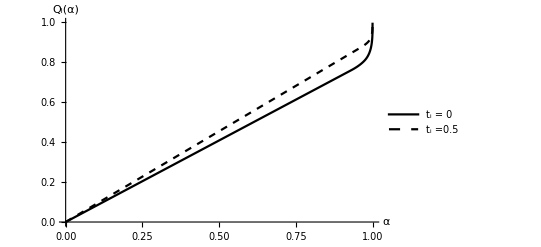

```mathematica
s11111sol05=Part[s11111sol,{Position[s11111sol,0.5][[1,1]]}][[1,2]];
s11111sol00=Part[s11111sol,{Position[s11111sol,0.0][[1,1]]}][[1,2]];
wj=1; σ=3.8; k=4; τi=τj=1.27; Ni=Nj=100; tj=0.1;
figureS9=Plot[{Piecewise[{{seg1Li[α,σ,k,0]/.s11111sol00,0≤α<α1i[ϕii,ϕij,σ, k, 0]/.s11111sol00},{seg2Li[α,ϕii,ϕij,σ, k, 0]/.s11111sol00,(α1i[ϕii,ϕij,σ, k, 0]/.s11111sol00)≤α<α2i[ϕii,ϕij,σ, k, 0]/.s11111sol00},{seg3Li[α,ϕii,ϕij,σ, k, 0]/.s11111sol00,(α2i[ϕii,ϕij,σ, k, 0]/.s11111sol00)≤α<1}}],Piecewise[{{seg1Lj[α,σ,k,0.5]/.s11111sol05,0≤α<α1j[ϕjj,ϕji,σ, k, 0.5]/.s11111sol05},{seg2Lj[α,ϕjj,ϕji,σ, k, 0.5]/.s11111sol05,(α1j[ϕjj,ϕji,σ, k, 0.5]/.s11111sol05)≤α<α2j[ϕjj,ϕji,σ, k, 0.5]/.s11111sol05},{seg3Lj[α,ϕjj,ϕji,σ, k, 0.5]/.s11111sol05,(α2j[ϕjj,ϕji,σ, k, 0.5]/.s11111sol05)≤α<1}}]
},{α,0,1}, 
PlotStyle->{{Black},{Dashed, Black}}, 
PlotLegends->Placed[LineLegend[{"t_i = 0","t_i =0.5"},LegendFunction->Panel,LegendMargins->1],{0.3,0.75}],
AxesLabel->{"α","Q_i(α)"},
AxesStyle->Directive[ Black],
AxesOrigin->{0,0},
PlotRange->Full]
Export["UnilateralTax_Figure_S9.pdf",figureS9];
```

### Figure S.10 : Social welfare function based on the Gini coefficient across scenarios

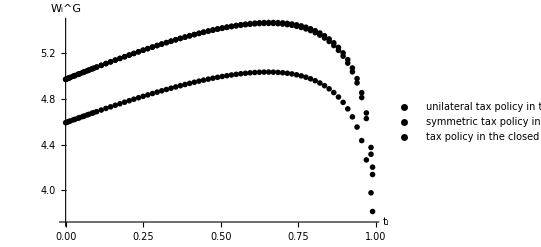

```mathematica
figureS10=ListPlot[{s11111welGi,s21111welGi,s12111welGi}
, PlotLegends->Placed[PointLegend[{"unilateral tax policy in the open economy","symmetric tax policy in the open economy", "tax policy in the closed economy"}
,LegendFunction->Panel,LegendMargins->1],{0.55,0.3}]
,AxesLabel->{"t_i","W_i^G"},AxesStyle->Directive[ Black]
,PlotMarkers->{"OpenMarkers",Tiny}
, MaxPlotPoints->75
,PlotStyle->Black
, PlotRange->Full]
Export["UnilateralTax_Figure_S10.pdf",figureS10];
```

### Table S.8 : Optimal tax rates (t_i^opt) for different parameter choices across scenarios

```mathematica
Grid[s11111topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s11211topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s11121topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s21111topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s21211topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s21121topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s12111topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s12211topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
Grid[s12121topti,Dividers->{2->True,False},FrameStyle->Directive[Dashing[2],Thickness[1]]]
```

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.05
t_i^opt|θ=0.25 | 0.45
t_i^opt|θ=0.5 | 0.54
t_i^opt|θ=1.0 | 0.595
t_i^opt|θ=1.5 | 0.62
t_i^opt|θ=2.0 | 0.63
t_i^opt|θ→∞ | 0.665
t_i^opt|Sen | 0.66

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.005
t_i^opt|θ=0.25 | 0.07
t_i^opt|θ=0.5 | 0.11
t_i^opt|θ=1.0 | 0.165
t_i^opt|θ=1.5 | 0.2
t_i^opt|θ=2.0 | 0.22
t_i^opt|θ→∞ | 0.33
t_i^opt|Sen | 0.315

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.
t_i^opt|θ=0.25 | 0.035
t_i^opt|θ=0.5 | 0.06
t_i^opt|θ=1.0 | 0.1
t_i^opt|θ=1.5 | 0.12
t_i^opt|θ=2.0 | 0.135
t_i^opt|θ→∞ | 0.23
t_i^opt|Sen | 0.2

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.05
t_i^opt|θ=0.25 | 0.44
t_i^opt|θ=0.5 | 0.53
t_i^opt|θ=1.0 | 0.59
t_i^opt|θ=1.5 | 0.61
t_i^opt|θ=2.0 | 0.62
t_i^opt|θ→∞ | 0.655
t_i^opt|Sen | 0.655

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.005
t_i^opt|θ=0.25 | 0.07
t_i^opt|θ=0.5 | 0.11
t_i^opt|θ=1.0 | 0.165
t_i^opt|θ=1.5 | 0.2
t_i^opt|θ=2.0 | 0.22
t_i^opt|θ→∞ | 0.33
t_i^opt|Sen | 0.31

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.
t_i^opt|θ=0.25 | 0.035
t_i^opt|θ=0.5 | 0.06
t_i^opt|θ=1.0 | 0.095
t_i^opt|θ=1.5 | 0.12
t_i^opt|θ=2.0 | 0.135
t_i^opt|θ→∞ | 0.225
t_i^opt|Sen | 0.2

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.04
t_i^opt|θ=0.25 | 0.405
t_i^opt|θ=0.5 | 0.5
t_i^opt|θ=1.0 | 0.565
t_i^opt|θ=1.5 | 0.59
t_i^opt|θ=2.0 | 0.605
t_i^opt|θ→∞ | 0.655
t_i^opt|Sen | 0.65

t_i^opt|θ=0 | 0.
t_i^opt|θ=0.01 | 0.005
t_i^opt|θ=0.25 | 0.055
t_i^opt|θ=0.5 | 0.095
t_i^opt|θ=1.0 | 0.145
t_i^opt|θ=1.5 | 0.18
t_i^opt|θ=2.0 | 0.2
t_i^opt|θ→∞ | 0.33
t_i^opt|Sen | 0.305

t_i^opt|θ=0 | s12121welAθ00i⟦{{{}}⟦1,1⟧}⟧⟦1,1⟧
t_i^opt|θ=0.01 | s12121welAθ001i⟦{{{}}⟦1,1⟧}⟧⟦1,1⟧
t_i^opt|θ=0.25 | s12121welAθ025i⟦{{{}}⟦1,1⟧}⟧⟦1,1⟧
t_i^opt|θ=0.5 | s12121welAθ05i⟦{{{}}⟦1,1⟧}⟧⟦1,1⟧
t_i^opt|θ=1.0 | s12121welAθ10i⟦{{{}}⟦1,1⟧}⟧⟦1,1⟧
t_i^opt|θ=1.5 | s12121welAθ15i⟦{{{}}⟦1,1⟧}⟧⟦1,1⟧
t_i^opt|θ=2.0 | s12121welAθ20i⟦{{{}}⟦1,1⟧}⟧⟦1,1⟧
t_i^opt|θ→∞ | s12121minIncreali⟦{{{}}⟦1,1⟧}⟧⟦1,1⟧
t_i^opt|Sen | s12121welGi⟦{{{}}⟦1,1⟧}⟧⟦1,1⟧